# A mathematical model for universal semantics (Text mining in Finnish)

### Weinan E and Yajun Zhou

## Introduction

Accompanying the topic extraction and word translation sections in [1], this Mathematica Notebook file is optimized for v11.0, and it will also run on v10.3 and v10.4. Earlier versions of Mathematica do not contain certain text analysis functionalities required for this program.

Unless explicitly stated otherwise, all the routines (word clustering, word cloud plotting and question answering) below are specifically designed for the current work [1], instead of being imported elsewhere.

[1] W. E and Y. Zhou, “A mathematical model for universal semantics,” 2020, arXiv:1907.12293v6 [cs.CL].

## Preparations

Text corpora mentioned below need to be stored in the following directory (or anywhere else that you redesignate)

```mathematica
SetDirectory["D:\\Documents"]
```

D:\Documents

This Mathematica Notebook file MUST BE executed AFTER all the cells in English.nb are evaluated.

### Pride and Prejudice

The full text for a Finnish translation of Jane Austen’s Pride and Prejudice is freely available from http://www.gutenberg.org/cache/epub/45186/pg45186.txt

After manual cleansing, we save the text as Ylpeys_ja _ennakkoluulo.txt,  which begins with

1 LUKU.


Yleisesti on myönnetty todeksi, että hyvissä varoissa oleva naimaton
mies tarvitsee välttämättömästi rinnalleen vaimon.

Kuinka vähän sellaisen miehen omia tunteita ja mielipiteitä
tunnetaan

and ends with

än halpasäätyinen vaimo kykeni käyttäytymään ison herraskartanon
emäntänä. Hän suostui todella käymään tervehtimässä heitä, välittämättä
yhtään Pemberleyn ylväitä metsiä kohdanneesta häväistyksestä.

The current Mathematica Notebook demonstrates the analysis of Pride and Prejudice. For the analysis of other texts in our current work, one needs to download text corpora and modify the codes slightly.

### Jane Eyre

The full text  for a Finnish translation of Charlotte Brontë’s Jane Eyre is freely available from http://www.gutenberg.org/cache/epub/47275/pg47275.txt

After manual cleansing, the text begins with

Ensimäinen luku.


Sinä päivänä oli mahdotonta lähteä kävelylle. Aamulla olimme
tosin tunnin verran kuljeskelleet lehdettömässä puistossa, mutta
päivällisestä asti (Mrs. Reedin tapana oli syödä aikai

and ends with

estarini", sanoo hän, "on valmistanut minua tuloonsa. Joka päivä hän
ilmoittaa yhä selvemmin: 'Totisesti minä tulen pian.' Ja joka tunti
vastaan minä kiihkeämmin: 'Amen, niin tule, Herra Jeesus!'"

### Origin of Species

The full text  for a Finnish translation of Charles Darwin’s Origin of Species is freely available from http://www.gutenberg.org/cache/epub/52187/pg52187.txt

After manual cleansing, the text begins with

I LUKU.

MUUNTELU KESYTYS- JA VILJELYSTILASSA.

Muuntelevaisuuden syyt. -- Elintapojen ja eri osien käytön tai käytön
puutteen vaikutukset. -- Vuorosuhteellinen muuntelu. -- Perinnöllisyys.
-- Kesytys

and ends with

```mathematica
"an muotoon ja että kiertotähtemme kiertäessä rataansa\njärkähtämättömän painolain mukaisesti tuosta yksinkertaisesta alusta on\nkehittynyt ja edelleen kehittyy mitä kauneimpia ja ihmeellisimpiä\nmuotoja."
```

Making sure that all the cells in English.nb have been evaluated, you are ready to execute all the cells in this file.

## Finnish

Our main references and data resources for the Finnish language are listed below.

Fred Karlsson, Finnish: An Essential Grammar. Routledge, London, UK, 1999 (translated by Andrew Chesterman)

Wiktionary (English and Finnish)

Project Gutenberg

## Finnish stop words

Our basic list of stop words comes from 
http://snowball.tartarus.org/algorithms/finnish/stop.txt

```mathematica
FinnishStopWords={"olla","olen","olet","on","olemme","olette","ovat","ole","oli","olisi","olisit","olisin","olisimme","olisitte","olisivat","olit","olin","olimme","olitte","olivat","ollut","olleet"}∪{"en","et","ei","emme","ette","eivät"}∪{"minä","minun","minut","minua","minussa","minusta","minuun","minulla","minulta","minulle","sinä","sinun","sinut","sinua","sinussa","sinusta","sinuun","sinulla","sinulta","sinulle","hän","hänen","hänet","häntä","hänessä","hänestä","häneen","hänellä","häneltä","hänelle","me","meidän","meidät","meitä","meissä","meistä","meihin","meillä","meiltä","meille","te","teidän","teidät","teitä","teissä","teistä","teihin","teillä","teiltä","teille","he","heidän","heidät","heitä","heissä","heistä","heihin","heillä","heiltä","heille"}∪{"tämä","tämän","tätä","tässä","tästä","tähän","tällä","tältä","tälle","tänä","täksi","tuo","tuon","tuota","tuossa","tuosta","tuohon","tuolla","tuolta","tuolle","tuona","tuoksi","se","sen","sitä","siinä","siitä","siihen","sillä","siltä","sille","sinä","siksi","nämä","näiden","näitä","näissä","näistä","näihin","näillä","näiltä","näille","näinä","näiksi","nuo","noiden","noita","noissa","noista","noihin","noilla","noilta","noille","noina","noiksi","ne","niiden","niitä","niissä","niistä","niihin","niillä","niiltä","niille","niinä","niiksi"}∪{"kuka","kenen","kenet","ketä","kenessä","kenestä","keneen","kenellä","keneltä","kenelle","kenenä","keneksi","ketkä","keiden","ketkä","keitä","keissä","keistä","keihin","keillä","keiltä","keille","keinä","keiksi","mikä","minkä","minkä","mitä","missä","mistä","mihin","millä","miltä","mille","minä","miksi","mitkä","joka","jonka","jota","jossa","josta","johon","jolla","jolta","jolle","jona","joksi","jotka","joiden","joita","joissa","joista","joihin","joilla","joilta","joille","joina","joiksi"}∪{"että","ja","jos","koska","kuin","mutta","niin","sekä","sillä","tai","vaan","vai","vaikka"}∪{"kanssa","mukaan","noin","poikki","yli","kun","niin","nyt","itse"}∪{"milloin","silloin"}∪{"kuinka"}∪{"vielä"}∪{"vain"}∪{"jo"}∪{"sinne"}∪{"no"}∪{"älä","ällös","älköön","älkäämme","älkää","älkööt"}∪{"saakka"}∪{"jokin","jotkin","jonkin","jonnekin","jotkin","joskin","jotenkin","johonkin","joihinkin","jollekin","joillekin","joksikin","joiksikin"}∪{"sangen"}∪{"siis"}∪{"kai"}∪{"eikä"}∪{"kaikeksi","kaikella","kaikelle","kaikelta","kaiken","kaikessa","kaikesta","kaiket","kaiketta","kaikiksi","kaikilla","kaikille","kaikilta","kaikin","kaikissa","kaikista","kaikitta","kaikkea","kaikkeen","kaikkein","kaikkena","kaikki","kaikkia","kaikkialla","kaikkialle","kaikkialta","kaikkien","kaikkiin","kaikkina","kaikkine"}∪{"ensi","ennen","ennestä","ennestänsä","ennestään","ensiksi","ensin"}∪{"ilman"}∪{"toinen","toisaalla","toisaalle","toisaalta","toiseen","toiseksi","toisella","toiselle","toiselta","toisen","toisena","toisessa","toisesta","toiset","toisetta","toisia","toisien","toisiin","toisiksi","toisilla","toisille","toisilta","toisin","toisina","toisine","toisissa","toisista","toisitta","toista","toisten"}∪{"ettei","etteivät","ettemme","etten","ettet","ettette"}∪{"aina","ainainen","ainakaan","ainakin"}∪{"itse","itseä","itseen","itseksi","itsellä","itselle","itseltä","itsen","itsenä","itsessä","itsestä","itsettä","itseään","itseämme","itseäni","itseänne","itseänsä","itseäsi","itseemme","itseeni","itseenne","itseensä","itseesi","itsekseen","itseksemme","itsekseni","itseksenne","itseksensä","itseksesi","itsellään","itsellämme","itselläni","itsellänne","itsellänsä","itselläsi","itselleen","itsellemme","itselleni","itsellenne","itsellensä","itsellesi","itseltään","itseltämme","itseltäni","itseltänne","itseltänsä","itseltäsi","itsemme","itsenään","itsenämme","itsenäni","itsenänne","itsenänsä","itsenäsi","itseni","itsenne","itsensä","itsesi","itsessään","itsessämme","itsessäni","itsessänne","itsessänsä","itsessäsi","itsestään","itsestämme","itsestäni","itsestänne","itsestänsä","itsestäsi"}∪{"yhä","yhdeksi","yhdellä","yhdelle","yhdeltä","yhden","yhdessä","yhdestä","yhdesti","yhdet","yhdettä","yhtä","yhtäällä","yhtäälle","yhtäältä","yhteen","yhtenä","yksi","yksiä","yksien","yksiin","yksiksi","yksillä","yksille","yksiltä","yksin","yksinä","yksine","yksissä","yksistä","yksittä","yksittäin"}∪{"yhtään","sentään"}∪{"aivan"}∪{"paljo","paljoa","paljoihin","paljoiksi","paljoilla","paljoille","paljoilta","paljoin","paljoina","paljoineen","paljoissa","paljoista","paljoitta","paljoja","paljojen","paljoksi","paljolla","paljolle","paljolta","paljon","paljona","paljoon","paljossa","paljosta","paljot","paljotta"}∪{"enemmän","eniten"}∪{"alas","ylös","poissa","pois"}∪{"täydy","täytyä","täytyi","täytyisi","täytykö","täytyköön","täytyminen","täytymistä","täytyne","täytynee","täytynyt","täytyy"}∪{"jälleen"}∪{"voi","voida","voidaan","voidakseen","voiden","voidessa","voikaa","voikaamme","voiko","voikoon","voikoot","voima","voimaan","voimaisillaan","voimalla","voiman","voimassa","voimasta","voimaton","voimatta","voiminen","voimista","voimme","voin","voine","voinee","voineet","voinemme","voinen","voinet","voinette","voinevat","voinut","voisi","voisimme","voisin","voisit","voisitte","voisivat","voit","voitaessa","voitaisi","voitaisiin","voitako","voitakoon","voitaman","voitane","voitaneen","voitava","voitiin","voitte","voitu","voiva","voivat"}∪{"sitten","sittenkin","sittenkään"}∪{"koskaan"}∪{"koko"}∪{"edes"}∪{"vasta","vastaan"}∪{"ole","olema","olemaan","olemaisillaan","olemalla","oleman","olemassa","olemasta","olematon","olematta","oleminen","olemista","olemme","olen","olet","olette","oleva","olevaa","olevaan","olevain","olevaksi","olevalla","olevalle","olevalta","olevan","olevana","olevassa","olevasta","olevat","olevatta","olevia","olevien","oleviin","oleviksi","olevilla","oleville","olevilta","olevin","olevina","olevine","olevissa","olevista","olevitta","oli","olimme","olin","olisi","olisimme","olisin","olisit","olisitte","olisivat","olit","olitte","olivat","olkaa","olkaamme","olko","olkoon","olkoot","olla","ollaan","ollakseen","olleet","ollen","ollessa","ollut","oltaessa","oltaisi","oltaisiin","oltako","oltakoon","oltaman","oltane","oltaneen","oltava","oltiin","oltu"}∪{"olevani","olevasi","olevansa"}∪{"mihin","mihinkään","mikä","mikään","miksi","miksikään","millä","millään","mille","millekään","milloin","milloinkaan","miltä","miltään","minä","minään","minkä","minkään","minne","minnekään","missä","missään","mistä","mistään","mitä","mitään","miten","mitenkään","mitkä","mitkään"}∪{"molemmaksi","molemmalla","molemmalle","molemmalta","molemman","molemmassa","molemmasta","molemmat","molemmatta","molemmiksi","molemmilla","molemmille","molemmilta","molemmin","molemmissa","molemmista","molemmitta","molempaa","molempaan","molempana","molempi","molempia","molempien","molempiin","molempina","molempine"}∪{"myöskin","myöskään"}∪{"itsekin","itsekään"}∪{"ollenkaan"}∪{"liene","lienee","lienemme","lienen","lienet","lienette","lienevät"}∪{"olematon","olematonta","olematonten","olemattomaan","olemattomaksi","olemattomalla","olemattomalle","olemattomalta","olemattoman","olemattomana","olemattomassa","olemattomasta","olemattomat","olemattomatta","olemattomia","olemattomien","olemattomiin","olemattomiksi","olemattomilla","olemattomille","olemattomilta","olemattomin","olemattomina","olemattomine","olemattomissa","olemattomista","olemattomitta","olleeksi","olleella","olleelle","olleelta","olleen","olleena","olleeseen","olleessa","olleesta","olleet","olleetta","olleiden","olleihin","olleiksi","olleilla","olleille","olleilta","ollein","olleina","olleine","olleisiin","olleissa","olleista","olleita","olleitta","olleitten","olluiksi","olluilla","olluille","olluilta","olluin","olluissa","olluista","olluitta","olluksi","ollulla","ollulle","ollulta","ollun","ollussa","ollusta","ollut","ollutta","oltu","oltua","oltuihin","oltuina","oltuine","oltuja","oltujen","oltuna","oltuun"}∪{"myös"}∪{"päin"}∪{"usein"}∪{"näiden","näihin","näiksi","näillä","näille","näiltä","näin","näinä","näine","näissä","näistä","näitä","näittä","nämä","täällä","täältä","tähän","täksi","tällä","tälle","tällöin","tältä","tämä","tämän","tänä","tänne","tässä","tästä","tätä","täten"}∪{"ihan"}∪{"enää"}∪{"sijaan"}∪{"kukaan"}∪{"mukaan"}∪{"ulos","ulkona","ulkoa"}∪{"ala","alakkain","alas","alatusten","alhaalla","alhaalle","alhaalta","ali","alitse","alla","alle","allekkain","alta"}∪{"halki","kautta","läpi","sitten","kesken"}∪{"edellä","edelle","edeltä","edes","edessä","edestä","editse","elative","esi","esiin","esillä","esille","esiltä","eteen","etenkään","etenkin"}∪{"siten"}∪{"alapuolella","yläpuolella"}∪{"aika","aivan","kovin","kyllin","liian","hiukan","melko","varsin","ehkä","jopa","juuri","kai","kenties","kyllä","mieluummin","vain"}∪{"jk","jkhun","jklla","jklle","jklta","jkn","jkssa","jksta","jkta","johon","johonkin","johonkuhun","joiden","joidenkin","joidenkuiden","joihin","joihinkin","joihinkuihin","joiksi","joiksikin","joiksikuiksi","joilla","joillain","joillakin","joillakuilla","joille","joillekin","joillekuille","joilta","joiltain","joiltakin","joiltakuilta","join","joina","joinain","joinakin","joinakuina","joine","joinekuine","joinkin","joinkuin","joissa","joissain","joissakin","joissakuissa","joista","joistain","joistakin","joistakuista","joita","joitain","joitakin","joitakuita","joitse","joitta","joittakin","joittakuitta","joitten","joittenkin","joittenkuitten","joka","jokainen","jokaiseen","jokaiseksi","jokaisella","jokaiselle","jokaiselta","jokaisen","jokaisena","jokaisessa","jokaisesta","jokaiset","jokaisetta","jokaisia","jokaisien","jokaisiin","jokaisiksi","jokaisilla","jokaisille","jokaisilta","jokaisin","jokaisina","jokaisine","jokaisissa","jokaisista","jokaisitta","jokaista","jokaisten","jokin","joksi","joksikin","joksikuksi","joku","jolla","jollain","jollakin","jollakulla","jolle","jollekin","jollekulle","jolloin","jolta","joltain","joltakin","joltakulta","jona","jonain","jonakin","jonakuna","jonka","jonkin","jonkun","jonne","jonnekin","jos","joskin","joskus","jossa","jossain","jossakin","jossakussa","josta","jostain","jostakin","jostakusta","jota","jotain","jotakin","jotakuta","joten","jotenkin","jotenkuten","jotka","jotkin","jotkut","jotta","jottakin","jottakutta"}∪{"erääksi","eräällä","eräälle","eräältä","erään","eräänä","erääseen","eräässä","eräästä","eräät","eräättä","eräiden","eräihin","eräiksi","eräillä","eräille","eräiltä","eräin","eräinä","eräine","eräisiin","eräissä","eräistä","eräitä","eräittä","eräitten","eräs","erästä"}∪{"kohti","vasten","paitsi","pitkin","päin"}∪{"moneen","moneksi","monella","monelle","monelta","monen","monena","monessa","monesta","monesti","monet","monetta","moni","monia","moniaalla","moniaalle","moniaalta","monien","moniin","moniksi","monilla","monille","monilta","monin","monina","monine","monissa","monista","monitta","monna","monta"}∪{"muutama","muutamaa","muutamaan","muutamain","muutamaksi","muutamalla","muutamalle","muutamalta","muutaman","muutamana","muutamassa","muutamasta","muutamat","muutamatta","muutamia","muutamien","muutamiin","muutamiksi","muutamilla","muutamille","muutamilta","muutamin","muutamina","muutamineen","muutamissa","muutamista","muutamitta"}∪{"muiden","muihin","muiksi","muilla","muille","muilta","muin","muina","muine","muissa","muista","muita","muitta","muitten","muu","muualla","muualle","muualta","muuhun","muuksi","muulla","muulle","muulloin","muulta","muun","muuna","muussa","muusta","muut","muuta","muuten","muutta"}∪{"usea","useaa","useaan","useain","useaksi","usealla","usealle","usealta","useammaksi","useammalla","useammalle","useammalta","useamman","useammassa","useammasta","useammat","useammatta","useammiksi","useammilla","useammille","useammilta","useammin","useammissa","useammista","useammitta","useampaa","useampaan","useampain","useampana","useampi","useampia","useampien","useampiin","useampina","useampine","usean","useana","useassa","useasta","useat","useata","useatta","useiden","useihin","useiksi","useilla","useille","useilta","useimmaksi","useimmalla","useimmalle","useimmalta","useimman","useimmassa","useimmasta","useimmat","useimmatta","useimmiksi","useimmilla","useimmille","useimmilta","useimmin","useimmissa","useimmista","useimmitta","useimpaan","useimpain","useimpana","useimpia","useimpien","useimpiin","useimpina","useimpine","usein","useina","useine","useinta","useinten","useisiin","useissa","useista","useita","useitta","useitten"}∪{"keskeä","keskellä","keskelle","keskeltä","kesken","keskenään","keski","keskitse"}∪{"lähekkäin","lähellä","lähelle","läheltä","lähes","lähetysten","lähi","lähitse","läsnä"}∪{"kuhunkin","kuidenkin","kuihinkin","kuiksikin","kuillakin","kuillekin","kuiltakin","kuinakin","kuinkin","kuissakin","kuistakin","kuitakin","kuitenkin","kuittakin","kuittenkin","kukin","kuksikin","kullakin","kullekin","kulloinkin","kultakin","kunakin","kunkin","kunnekin","kussakin","kustakin","kutakin","kutkin","kuttakin"}∪{"kummaksikin","kummallakin","kummallekin","kummaltakin","kummankin","kummassakin","kummastakin","kummatkin","kummattakin","kummiksikin","kummillakin","kummillekin","kummiltakin","kumminkin","kummissakin","kummistakin","kummittakin","kumpaakin","kumpaankin","kumpanakin","kumpiakin","kumpienkin","kumpiinkin","kumpikin","kumpinakin","kumpinekin"}∪{"kummaksi","kummalla","kummalle","kummalta","kumman","kummassa","kummasta","kummat","kummatta","kummiksi","kummilla","kummille","kummilta","kummin","kummissa","kummista","kummitta","kumpaa","kumpaan","kumpain","kumpana","kumpi","kumpia","kumpien","kumpiin","kumpina","kumpine"}∪{"jommaksikummaksi","jommallakummalla","jommallekummalle","jommaltakummalta","jommankumman","jommassakummassa","jommastakummasta","jommatkummat","jommattakummatta","jommiksikummiksi","jommillakummilla","jommillekummille","jommiltakummilta","jomminkummin","jommissakummissa","jommistakummista","jommittakummitta","jompaakumpaa","jompaankumpaan","jompanakumpana","jompiakumpia","jompiinkumpiin","jompikumpi","jompinakumpina","jompinekumpine"}∪{"minkälainen","minkälaiseen","minkälaiseksi","minkälaisella","minkälaiselle","minkälaiselta","minkälaisen","minkälaisena","minkälaisessa","minkälaisesta","minkälaiset","minkälaisetta","minkälaisia","minkälaisien","minkälaisiin","minkälaisiksi","minkälaisilla","minkälaisille","minkälaisilta","minkälaisin","minkälaisina","minkälaisineen","minkälaisissa","minkälaisista","minkälaisitta","minkälaista","minkälaisten"}∪{"millainen","millaiseen","millaiseksi","millaisella","millaiselle","millaiselta","millaisen","millaisena","millaisessa","millaisesta","millaiset","millaisetta","millaisia","millaisien","millaisiin","millaisiksi","millaisilla","millaisille","millaisilta","millaisin","millaisina","millaisineenn","millaisissa","millaisista","millaisitta","millaista","millaisten"}∪{"tällainen","tällaiseen","tällaiseksi","tällaisella","tällaiselle","tällaiselta","tällaisen","tällaisena","tällaisessa","tällaisesta","tällaiset","tällaisetta","tällaisia","tällaisien","tällaisiin","tällaisiksi","tällaisilla","tällaisille","tällaisilta","tällaisin","tällaisina","tällaisineen","tällaisissa","tällaisista","tällaisitta","tällaista","tällaisten"}∪{"tuollainen","tuollaiseen","tuollaiseksi","tuollaisella","tuollaiselle","tuollaiselta","tuollaisen","tuollaisena","tuollaisessa","tuollaisesta","tuollaiset","tuollaisetta","tuollaisia","tuollaisien","tuollaisiin","tuollaisiksi","tuollaisilla","tuollaisille","tuollaisilta","tuollaisin","tuollaisina","tuollaisineen","tuollaisissa","tuollaisista","tuollaisitta","tuollaista","tuollaisten"}∪{"sellainen","sellaiseen","sellaiseksi","sellaisella","sellaiselle","sellaiselta","sellaisen","sellaisena","sellaisessa","sellaisesta","sellaiset","sellaisetta","sellaisia","sellaisien","sellaisiin","sellaisiksi","sellaisilla","sellaisille","sellaisilta","sellaisin","sellaisina","sellaisineen","sellaisissa","sellaisista","sellaisitta","sellaista","sellaisten"}∪{"semmoinen","semmoiseen","semmoiseksi","semmoisella","semmoiselle","semmoiselta","semmoisen","semmoisena","semmoisessa","semmoisesta","semmoiset","semmoisetta","semmoisia","semmoisien","semmoisiin","semmoisiksi","semmoisilla","semmoisille","semmoisilta","semmoisin","semmoisina","semmoisine","semmoisissa","semmoisista","semmoisitta","semmoista","semmoisten"}∪{"alitse","ansiosta","eduksi","halki","johdosta","jäljessä","jälkeen"}∪{"keskuudeksi","keskuudella","keskuudelle","keskuudelta","keskuuden","keskuudessa","keskuudesta","keskuudet","keskuudetta","keskuuksia","keskuuksien","keskuuksiin","keskuuksiksi","keskuuksilla","keskuuksille","keskuuksilta","keskuuksin","keskuuksina","keskuuksineen","keskuuksissa","keskuuksista","keskuuksitta","keskuus","keskuuteen","keskuutena","keskuutta"}∪{"kohdaksi","kohdalla","kohdalle","kohdalta","kohdan","kohdassa","kohdasta","kohdat","kohdatta","kohdiksi","kohdilla","kohdille","kohdilta","kohdin","kohdissa","kohdista","kohditta","kohta","kohtaa","kohtaan","kohtain","kohtana","kohtia","kohtien","kohtiin","kohtina","kohtineen"}∪{"luo","luota","luona","luokse"}∪{"lävitse","mukana","ohi","ohitse","perässä","poikki"}∪{"sisä","sisään","sisäkkäin","sisällä","sisälle","sisältä","sisässä","sisästä","sisätysten"}∪{"taa","taakse","taannoin","taas","taitse","taka","takaa","takaisin","takana"}∪{"takia","tähden","vuoksi","yli","ylitse"}∪{"viereen","vierekkäin","vierellä","vierelle","viereltä","vieren","vieressä","vierestä","vieret","vieretysten","vieri","vieriä","vierien","vieriin","vierillä","vierille","vieriltä","vierissä","vieristä","vieritse","viertä"}∪{"ympäri","ympäriinsä","ympärillä","ympärille","ympäriltä","ympäritse"}∪{"asti","jollei","jollen","jollet","jolle","ikään","eli","ellei","kunnes","kuten","mikäli","muttei","mutten","muttet","mutte","pian"}∪{"sellaisenaan","oikein","todella","erittäin","hyvin","oitis"}∪{"saa","saada","saadaan","saadakseen","saaden","saadessa","saakaa","saakaamme","saako","saakoon","saakoot","saama","saamaan","saamaisillaan","saamalla","saaman","saamassa","saamasta","saamaton","saamatta","saaminen","saamista","saamme","saan","saane","saanee","saaneet","saanemme","saanen","saanet","saanette","saanevat","saanut","saat","saataessa","saataisi","saataisiin","saatako","saatakoon","saataman","saatane","saataneen","saatava","saatiin","saatte","saatu","saava","saavat","sai","saimme","sain","saisi","saisimme","saisin","saisit","saisitte","saisivat","sait","saitte","saivat"}∪{"tuskin","ennenkuin","niinkuin"}∪{"tee","teemme","teen","teet","teette","tehdä","tehdään","tehdäkseen","tehden","tehdessä","tehkää","tehkäämme","tehkö","tehköön","tehkööt","tehne","tehnee","tehneet","tehnemme","tehnen","tehnet","tehnette","tehnevät","tehnyt","tehtäessä","tehtäisi","tehtäisiin","tehtäkö","tehtäköön","tehtämän","tehtäne","tehtäneen","tehtävä","tehtiin","tehty","teimme","tein","teit","teitte","tekee","tekemä","tekemään","tekemäisillään","tekemällä","tekemän","tekemässä","tekemästä","tekemätön","tekemättä","tekeminen","tekemistä","tekevä","tekevät","teki","tekisi","tekisimme","tekisin","tekisit","tekisitte","tekisivät","tekivät"}∪{"entä"}∪{"sama","samaa","samaan","samaksi","samalla","samalle","samalta","saman","samana","samassa","samasta","samat","samaten","samatta"}∪{"kykene","kykenee","kykenemä","kykenemään","kykenemäisillään","kykenemällä","kykenemän","kykenemässä","kykenemästä","kykenemätön","kykenemättä","kykeneminen","kykenemistä","kykenemme","kykenen","kykenet","kykenette","kykenevä","kykenevät","kykeni","kykenimme","kykenin","kykenisi","kykenisimme","kykenisin","kykenisit","kykenisitte","kykenisivät","kykenit","kykenitte","kykenivät"}∪{"kykenemätön","kykenemätöntä","kykenemätönten","kykenemättömään","kykenemättömäksi","kykenemättömällä","kykenemättömälle","kykenemättömältä","kykenemättömän","kykenemättömänä","kykenemättömässä","kykenemättömästä","kykenemättömät","kykenemättömättä","kykenemättömiä","kykenemättömien","kykenemättömiin","kykenemättömiksi","kykenemättömillä","kykenemättömille","kykenemättömiltä","kykenemättömin","kykenemättöminä","kykenemättömine","kykenemättömissä","kykenemättömistä","kykenemättömittä","kykenevä","kykenevää","kykenevään","kykeneväin","kykeneväksi","kykenevällä","kykenevälle","kykenevältä","kykenevän","kykenevänä","kykenevässä","kykenevästä","kykenevät","kykenevättä","kykeneviä","kykenevien","kykeneviin","kykeneviksi","kykenevillä","kykeneville","kykeneviltä","kykenevin","kykenevinä","kykenevine","kykenevissä","kykenevistä","kykenevittä"}∪{"pysty","pystyä","pystyäkseen","pystyen","pystyessä","pystyi","pystyimme","pystyin","pystyisi","pystyisimme","pystyisin","pystyisit","pystyisitte","pystyisivät","pystyit","pystyitte","pystyivät","pystykää","pystykäämme","pystykö","pystyköön","pystykööt","pystymä","pystymään","pystymäisillään","pystymällä","pystymän","pystymässä","pystymästä","pystymätön","pystymättä","pystyminen","pystymistä","pystymme","pystyn","pystyne","pystynee","pystyneet","pystynemme","pystynen","pystynet","pystynette","pystynevät","pystynyt","pystyt","pystytä","pystytään","pystyttäessä","pystyttäisi","pystyttäisiin","pystyttäkö","pystyttäköön","pystyttämän","pystyttäne","pystyttäneen","pystyttävä","pystytte","pystyttiin","pystytty","pystyvä","pystyvät","pystyy"}∪{"pystyneeksi","pystyneellä","pystyneelle","pystyneeltä","pystyneen","pystyneenä","pystyneeseen","pystyneessä","pystyneestä","pystyneet","pystyneettä","pystyneiden","pystyneihin","pystyneiksi","pystyneillä","pystyneille","pystyneiltä","pystynein","pystyneinä","pystyneine","pystyneisiin","pystyneissä","pystyneistä","pystyneitä","pystyneittä","pystyneitten","pystynyt","pystynyttä"}∪{"pelkäksi","pelkällä","pelkälle","pelkältä","pelkän","pelkässä","pelkästä","pelkät","pelkättä","pelkiksi","pelkillä","pelkille","pelkiltä","pelkin","pelkissä","pelkistä","pelkittä","pelkkä","pelkkää","pelkkään","pelkkäin","pelkkänä","pelkkiä","pelkkien","pelkkiin","pelkkinä","pelkkine"}∪{"olemaa","olemain","olemana","olemat","olemia","olemien","olemiin","olemiksi","olemilla","olemille","olemilta","olemin","olemina","olemineen","olemissa","olemitta"}∪{"ne","niiden","niihin","niiksi","niillä","niille","niiltä","niin","niinä","niine","niissä","niistä","niitä","niittä","niitten","se","sen","siellä","sieltä","siihen","siinä","siis","siitä","siksi","sillä","sille","silloin","siltä","sinä","sinne","sitä","siten"}∪{"tahansa"}∪{"moinen","moiseen","moiseksi","moisella","moiselle","moiselta","moisen","moisena","moisessa","moisesta","moiset","moisetta","moisia","moisien","moisiin","moisiksi","moisilla","moisille","moisilta","moisin","moisina","moisine","moisissa","moisista","moisitta","moista","moisten"}∪{"toinen","toisaalla","toisaalle","toisaalta","toiseen","toiseksi","toisella","toiselle","toiselta","toisen","toisena","toisessa","toisesta","toiset","toisetta","toisia","toisien","toisiin","toisiksi","toisilla","toisille","toisilta","toisin","toisina","toisine","toisissa","toisista","toisitta","toista","toisten"}∪{"rinnalla"}∪{"sama","samaa","samaan","samaksi","samalla","samalle","samalta","saman","samana","samassa","samasta","samat","samaten","samatta","samoihin","samoiksi","samoilla","samoille","samoilta","samoin","samoina","samoine","samoissa","samoista","samoitta","samoja","samojen"}∪{"myötä","lain","lainkaan","vallan","vastedes","vastikään","senvuoksi","heti","ylen","tahi"}∪{"vaikkei","vaikken","vaikket","vaikkemme","vaikkette","vaikkeivät"}∪{"eteensä","eteemme"}∪{"oma","omaa","omaan","omain","omaksi","omalla","omalle","omalta","oman","omana","omassa","omasta","omat","omatta","omia","omien","omiin","omiksi","omilla","omille","omilta","omin","omina","omine","omissa","omista","omitta"}∪{"ainoa","ainoaa","ainoaan","ainoain","ainoaksi","ainoalla","ainoalle","ainoalta","ainoan","ainoana","ainoassa","ainoasta","ainoastaan","ainoat","ainoata","ainoatta","ainoiden","ainoihin","ainoiksi","ainoilla","ainoille","ainoilta","ainoin","ainoina","ainoine","ainoisiin","ainoissa","ainoista","ainoita","ainoitta","ainoitten","ainuiden","ainuihin","ainuiksi","ainuilla","ainuille","ainuilta","ainuin","ainuina","ainuineen","ainuisiin","ainuissa","ainuista","ainuita","ainuitta","ainuitten","ainut","ainutta","ainuuksi","ainuulla","ainuulle","ainuulta","ainuun","ainuuna","ainuuseen","ainuussa","ainuusta","ainuut","ainuutta"}∪{"kerran","joukossa","joukosta","joukoon","väliin","välillä","välissä","välistä"}∪{"toisensa","toistensa","toisiensa","toisiansa","toisiaan","toisissansa","toisissaan","toisistansa","toisistaan","toisiinsa","toisillansa","toisillaan","toisiltansa","toisiltaan","toisillensa","toisilleen","toisinansa","toisinaan","toisiksensa","toisikseen","toisinsa","toisittansa","toisittaan","toisinensa","toisineen"}∪{"uudestaan","uudelleen"};
```

```mathematica
FinnishStopRoots=DeleteCases[FinnishStopWords2=DeleteCases[FinnishStopWords1=DeleteCases[FinnishStopWords,Alternatives@@Select[FinnishStopWords,((StringMatchQ[#,___~~"kin"|"ka"|"kä"|"ko"|"kö"|"han"|"hän"|"pa"|"pä"|"kaan"|"kään"])&&({StringReplace[#,"kin"|"ka"|"kä"|"ko"|"kö"|"han"|"hän"|"pa"|"pä"|"kaan"|"kään"~~WordBoundary:>""]}∩FinnishStopWords!={}))&]],Alternatives@@Select[FinnishStopWords1,((StringMatchQ[#,___~~""|"kse"~~"ni"|"an"|"en"|"mme"|"nne"|"nsa"|"nsä"|"tte"|"vat"|"vät"])&&({StringReplace[#,""|"kse"~~"ni"|"an"|"en"|"mme"|"nne"|"nsa"|"nsä"|"tte"|"vat"|"vät"~~WordBoundary:>""]}∩FinnishStopWords1!={}))&]],Alternatives@@Select[FinnishStopWords2,((StringMatchQ[#,___~~"ksi"|"ssa"|"ssä"|"sta"|"stä"|"lle"|"lta"|"ltä"|"lla"|"llä"|"tta"|"ttä"])&&({StringReplace[#,"ksi"|"ssa"|"ssä"|"sta"|"stä"|"lle"|"lta"|"ltä"|"lla"|"llä"|"tta"|"ttä"~~WordBoundary:>""]}∩FinnishStopWords2!={}))&]]
```

{aika,aina,ainainen,ainoa,ainoaa,ainoain,ainoan,ainoana,ainoat,ainoata,ainoiden,ainoihin,ainoiksi,ainoilla,ainoille,ainoilta,ainoin,ainoina,ainoine,ainoisiin,ainoissa,ainoista,ainoita,ainoitta,ainoitten,ainuiden,ainuihin,ainuiksi,ainuilla,ainuille,ainuilta,ainuin,ainuina,ainuineen,ainuisiin,ainuissa,ainuista,ainuita,ainuitta,ainuitten,ainut,ainutta,ainuuksi,ainuulla,ainuulle,ainuulta,ainuun,ainuuna,ainuuseen,ainuussa,ainuusta,ainuut,ainuutta,aivan,ala,älä,alakkain,alapuolella,alas,alatusten,alhaalla,alhaalle,alhaalta,ali,alitse,älkää,älköön,älkööt,alla,alle,allekkain,ällös,alta,ansiosta,asti,edellä,edelle,edeltä,edes,edessä,edestä,editse,eduksi,ehkä,ei,elative,eli,ellei,emme,en,enää,enemmän,eniten,ennen,ennenkuin,ennestä,ennestään,ensi,ensin,entä,erääksi,eräällä,eräälle,eräältä,erään,eräänä,erääseen,eräässä,eräästä,eräät,eräättä,eräiden,eräihin,eräiksi,eräillä,eräille,eräiltä,eräin,eräinä,eräine,eräisiin,eräissä,eräistä,eräitä,eräittä,eräitten,eräs,erästä,erittäin,esi,esiin,et,eteemme,eteen,eteensä,etenkään,etenkin,että,ette,ettei,etten,ettet,halki,hän,häneen,hänellä,hänelle,häneltä,hänessä,hänestä,hänet,häntä,he,heidän,heidät,heihin,heillä,heille,heiltä,heissä,heistä,heitä,heti,hiukan,hyvin,ihan,ikään,ilman,itse,itseä,itseään,itseäsi,itseemme,itseeni,itseenne,itseensä,itseesi,itseksesi,itsellään,itselläsi,itsellesi,itseltään,itseltäsi,itsen,itsenä,itsenään,itsenäsi,itsesi,itsessään,itsessäsi,itsestään,itsestäsi,ja,jäljessä,jälkeen,jälleen,jk,jkhun,jkn,jkta,jo,johdosta,johon,johonkuhun,joiden,joidenkuiden,joihin,joihinkuihin,joiksi,joiksikuiksi,joilla,joillain,joillakuilla,joille,joillekuille,joilta,joiltain,joiltakuilta,join,joina,joinain,joinakuina,joine,joinekuine,joinkuin,joissa,joissain,joissakuissa,joista,joistain,joistakuista,joita,joitain,joitakuita,joitse,joitta,joittakuitta,joitten,joittenkuitten,jokainen,jokaiseen,jokaiseksi,jokaisella,jokaiselle,jokaiselta,jokaisen,jokaisena,jokaisessa,jokaisesta,jokaiset,jokaisetta,jokaisia,jokaisien,jokaisiin,jokaisiksi,jokaisilla,jokaisille,jokaisilta,jokaisin,jokaisina,jokaisine,jokaisissa,jokaisista,jokaisitta,jokaista,jokaisten,joksikuksi,joku,jollain,jollakulla,jollei,jollekulle,jollen,jollet,jolloin,joltain,joltakulta,jommaksikummaksi,jommallakummalla,jommallekummalle,jommaltakummalta,jommankumman,jommassakummassa,jommastakummasta,jommatkummat,jommattakummatta,jommiksikummiksi,jommillakummilla,jommillekummille,jommiltakummilta,jomminkummin,jommissakummissa,jommistakummista,jommittakummitta,jompaakumpaa,jompaankumpaan,jompanakumpana,jompiakumpia,jompiinkumpiin,jompikumpi,jompinakumpina,jompinekumpine,jona,jonain,jonakuna,jonka,jonkin,jonkun,jos,joskus,jossain,jossakussa,jostain,jostakusta,jota,jotain,jotakuta,joten,jotenkuten,jotka,jotkin,jotkut,jottakutta,joukoon,joukossa,joukosta,juuri,kai,kaikeksi,kaikella,kaikelle,kaikelta,kaiken,kaikessa,kaikesta,kaiket,kaiketta,kaikiksi,kaikilla,kaikille,kaikilta,kaikissa,kaikista,kaikitta,kaikkea,kaikkeen,kaikkein,kaikkena,kaikki,kaikkia,kaikkiin,kaikkina,kaikkine,kanssa,kautta,keiden,keihin,keiksi,keillä,keille,keiltä,keinä,keissä,keistä,keitä,keneen,keneksi,kenellä,kenelle,keneltä,kenen,kenenä,kenessä,kenestä,kenet,kenties,kerran,keskeä,keskellä,keskelle,keskeltä,kesken,keskenään,keski,keskitse,keskuudeksi,keskuudella,keskuudelle,keskuudelta,keskuuden,keskuudessa,keskuudesta,keskuudet,keskuudetta,keskuuksia,keskuuksien,keskuuksiin,keskuuksiksi,keskuuksilla,keskuuksille,keskuuksilta,keskuuksin,keskuuksina,keskuuksineen,keskuuksissa,keskuuksista,keskuuksitta,keskuus,keskuuteen,keskuutena,keskuutta,ketä,ketkä,kohdaksi,kohdalla,kohdalle,kohdalta,kohdan,kohdassa,kohdasta,kohdat,kohdatta,kohdiksi,kohdilla,kohdille,kohdilta,kohdin,kohdissa,kohdista,kohditta,kohta,kohtaa,kohtain,kohtana,kohti,kohtia,kohtiin,kohtina,kohtineen,koko,koska,kovin,kuhunkin,kuidenkin,kuihinkin,kuiksikin,kuillakin,kuillekin,kuiltakin,kuin,kuinakin,kuissakin,kuistakin,kuitakin,kuitenkin,kuittakin,kuittenkin,kuka,kukin,kuksikin,kullakin,kullekin,kulloinkin,kultakin,kummaksi,kummalla,kummalle,kummalta,kumman,kummassa,kummasta,kummat,kummatta,kummiksi,kummilla,kummille,kummilta,kummin,kummissa,kummista,kummitta,kumpaa,kumpaan,kumpain,kumpana,kumpi,kumpia,kumpiin,kumpina,kumpine,kun,kunakin,kunnekin,kunnes,kussakin,kustakin,kutakin,kuten,kutkin,kuttakin,kykene,kykenee,kykenemä,kykenemään,kykenemäisillään,kykenemän,kykenemätön,kykenemätöntä,kykenemätönten,kykenemättömään,kykenemättömäksi,kykenemättömällä,kykenemättömälle,kykenemättömältä,kykenemättömän,kykenemättömänä,kykenemättömässä,kykenemättömästä,kykenemättömät,kykenemättömättä,kykenemättömiä,kykenemättömien,kykenemättömiin,kykenemättömiksi,kykenemättömillä,kykenemättömille,kykenemättömiltä,kykenemättömin,kykenemättöminä,kykenemättömine,kykenemättömissä,kykenemättömistä,kykenemättömittä,kykeneminen,kykenemistä,kykenen,kykenet,kykenevä,kykenevää,kykenevään,kykeneväin,kykenevän,kykenevänä,kykeneviä,kykenevien,kykeneviin,kykeneviksi,kykenevillä,kykeneville,kykeneviltä,kykenevin,kykenevinä,kykenevine,kykenevissä,kykenevistä,kykenevittä,kykeni,kykenin,kykenisi,kykenisin,kykenisit,kykenit,kyllä,kyllin,lähekkäin,lähellä,lähelle,läheltä,lähes,lähetysten,lähi,lähitse,lain,läpi,läsnä,lävitse,liene,lienee,lienen,lienet,liian,luo,luokse,luona,luota,me,meidän,meidät,meihin,meillä,meille,meiltä,meissä,meistä,meitä,melko,mieluummin,mihin,mikä,mikään,mikäli,miksi,millä,millään,millainen,millaiseen,millaiseksi,millaisella,millaiselle,millaiselta,millaisen,millaisena,millaisessa,millaisesta,millaiset,millaisetta,millaisia,millaisien,millaisiin,millaisiksi,millaisilla,millaisille,millaisilta,millaisin,millaisina,millaisineenn,millaisissa,millaisista,millaisitta,millaista,millaisten,mille,milloin,miltä,miltään,minä,minään,minkä,minkään,minkälainen,minkälaiseen,minkälaiseksi,minkälaisella,minkälaiselle,minkälaiselta,minkälaisen,minkälaisena,minkälaisessa,minkälaisesta,minkälaiset,minkälaisetta,minkälaisia,minkälaisien,minkälaisiin,minkälaisiksi,minkälaisilla,minkälaisille,minkälaisilta,minkälaisin,minkälaisina,minkälaisineen,minkälaisissa,minkälaisista,minkälaisitta,minkälaista,minkälaisten,minne,minua,minulla,minulle,minulta,minun,minussa,minusta,minut,minuun,missä,missään,mistä,mistään,mitä,mitään,miten,mitkä,mitkään,moinen,moiseen,moiseksi,moisella,moiselle,moiselta,moisen,moisena,moisessa,moisesta,moiset,moisetta,moisia,moisien,moisiin,moisiksi,moisilla,moisille,moisilta,moisin,moisina,moisine,moisissa,moisista,moisitta,moista,moisten,molemmaksi,molemmalla,molemmalle,molemmalta,molemman,molemmassa,molemmasta,molemmat,molemmatta,molemmiksi,molemmilla,molemmille,molemmilta,molemmin,molemmissa,molemmista,molemmitta,molempaa,molempaan,molempana,molempi,molempia,molempiin,molempina,molempine,moneen,moneksi,monella,monelle,monelta,monen,monena,monessa,monesta,monesti,monet,monetta,moni,monia,moniaalla,moniaalle,moniaalta,moniin,monin,monina,monine,monna,monta,muiden,muihin,muiksi,muilla,muille,muilta,muin,muina,muine,muissa,muista,muita,muitta,muitten,mukaan,mukana,mutta,mutte,muttei,mutten,muttet,muu,muualla,muualle,muualta,muuhun,muulloin,muun,muuna,muut,muuta,muutama,muutamaa,muutamain,muutaman,muutamana,muutamat,muutamia,muutamien,muutamiin,muutamiksi,muutamilla,muutamille,muutamilta,muutamin,muutamina,muutamineen,muutamissa,muutamista,muutamitta,myös,myötä,näiden,näihin,näiksi,näillä,näille,näiltä,näin,näinä,näine,näissä,näistä,näitä,näittä,nämä,ne,niiden,niihin,niiksi,niillä,niille,niiltä,niin,niinä,niine,niinkuin,niissä,niistä,niitä,niittä,niitten,no,noiden,noihin,noiksi,noilla,noille,noilta,noin,noina,noissa,noista,noita,nuo,nyt,ohi,ohitse,oikein,oitis,ole,olema,olemaa,olemain,olemaisillaan,oleman,olemana,olemat,olematon,olematonta,olematonten,olemattomaan,olemattomaksi,olemattomalla,olemattomalle,olemattomalta,olemattoman,olemattomana,olemattomassa,olemattomasta,olemattomat,olemattomatta,olemattomia,olemattomien,olemattomiin,olemattomiksi,olemattomilla,olemattomille,olemattomilta,olemattomin,olemattomina,olemattomine,olemattomissa,olemattomista,olemattomitta,olemia,olemien,olemiin,olemiksi,olemilla,olemille,olemilta,olemin,olemina,olemineen,olemissa,olemista,olemitta,olen,olet,oleva,olevaa,olevain,olevan,olevana,olevasi,olevia,olevien,oleviin,oleviksi,olevilla,oleville,olevilta,olevin,olevina,olevine,olevissa,olevista,olevitta,oli,olin,olisi,olisin,olisit,olit,olkaa,olko,olkoon,olkoot,olla,olleeksi,olleella,olleelle,olleelta,olleen,olleena,olleeseen,olleessa,olleesta,olleet,olleetta,olleiden,olleihin,olleiksi,olleilla,olleille,olleilta,ollein,olleina,olleine,olleisiin,olleissa,olleista,olleita,olleitta,olleitten,ollen,ollessa,olluiksi,olluilla,olluille,olluilta,olluin,olluissa,olluista,olluitta,olluksi,ollulla,ollulle,ollulta,ollun,ollussa,ollusta,ollut,ollutta,oltaessa,oltaisi,oltaisiin,oltako,oltakoon,oltaman,oltane,oltava,oltiin,oltu,oltua,oltuihin,oltuina,oltuine,oltuja,oltujen,oltuna,oltuun,oma,omaa,omain,oman,omana,omat,omia,omien,omiin,omiksi,omilla,omille,omilta,omin,omina,omine,omissa,omista,omitta,on,ovat,päin,paitsi,paljo,paljoa,paljoihin,paljoiksi,paljoilla,paljoille,paljoilta,paljoin,paljoina,paljoineen,paljoissa,paljoista,paljoitta,paljoja,paljojen,paljon,paljona,paljoon,paljot,pelkäksi,pelkällä,pelkälle,pelkältä,pelkän,pelkässä,pelkästä,pelkät,pelkättä,pelkiksi,pelkillä,pelkille,pelkiltä,pelkin,pelkissä,pelkistä,pelkittä,pelkkä,pelkkää,pelkkään,pelkkäin,pelkkänä,pelkkiä,pelkkien,pelkkiin,pelkkinä,pelkkine,perässä,pian,pitkin,poikki,pois,poissa,pysty,pystyä,pystyessä,pystyi,pystyin,pystyisi,pystyisin,pystyisit,pystyit,pystykää,pystyköön,pystykööt,pystymä,pystymään,pystymäisillään,pystymän,pystymätön,pystyminen,pystymistä,pystyn,pystyne,pystynee,pystyneenä,pystyneeseen,pystyneet,pystyneiden,pystyneihin,pystyneiksi,pystyneillä,pystyneille,pystyneiltä,pystynein,pystyneinä,pystyneine,pystyneisiin,pystyneissä,pystyneistä,pystyneitä,pystyneittä,pystyneitten,pystynet,pystynyt,pystynyttä,pystyt,pystytä,pystytään,pystyttäessä,pystyttäisi,pystyttäisiin,pystyttäkö,pystyttäköön,pystyttämän,pystyttäne,pystyttävä,pystyttiin,pystytty,pystyvä,pystyy,rinnalla,saa,saada,saaden,saadessa,saakaa,saakka,saakoon,saakoot,saama,saamaisillaan,saaman,saamaton,saaminen,saamista,saan,saane,saanee,saaneet,saanet,saanut,saat,saataessa,saataisi,saataisiin,saatako,saatakoon,saataman,saatane,saatava,saatiin,saatu,saava,sai,sain,saisi,saisin,saisit,sait,sama,samaa,saman,samana,samat,samoihin,samoiksi,samoilla,samoille,samoilta,samoin,samoina,samoine,samoissa,samoista,samoitta,samoja,samojen,sangen,se,sellainen,sellaiseen,sellaiseksi,sellaisella,sellaiselle,sellaiselta,sellaisen,sellaisena,sellaisessa,sellaisesta,sellaiset,sellaisetta,sellaisia,sellaisien,sellaisiin,sellaisiksi,sellaisilla,sellaisille,sellaisilta,sellaisin,sellaisina,sellaisineen,sellaisissa,sellaisista,sellaisitta,sellaista,sellaisten,semmoinen,semmoiseen,semmoiseksi,semmoisella,semmoiselle,semmoiselta,semmoisen,semmoisena,semmoisessa,semmoisesta,semmoiset,semmoisetta,semmoisia,semmoisien,semmoisiin,semmoisiksi,semmoisilla,semmoisille,semmoisilta,semmoisin,semmoisina,semmoisine,semmoisissa,semmoisista,semmoisitta,semmoista,semmoisten,sen,sentään,senvuoksi,siellä,sieltä,siihen,siinä,siis,siitä,sijaan,siksi,sillä,sille,silloin,siltä,sinä,sinne,sinua,sinulla,sinulle,sinulta,sinun,sinussa,sinusta,sinut,sinuun,sisä,sisään,sisäkkäin,sisätysten,sitä,siten,sitten,taa,taakse,täällä,täältä,taannoin,taas,tähän,tahansa,tähden,tahi,tai,taitse,taka,takaa,takaisin,takana,takia,täksi,tällä,tällainen,tällaiseen,tällaiseksi,tällaisella,tällaiselle,tällaiselta,tällaisen,tällaisena,tällaisessa,tällaisesta,tällaiset,tällaisetta,tällaisia,tällaisien,tällaisiin,tällaisiksi,tällaisilla,tällaisille,tällaisilta,tällaisin,tällaisina,tällaisineen,tällaisissa,tällaisista,tällaisitta,tällaista,tällaisten,tälle,tällöin,tältä,tämä,tämän,tänä,tänne,tässä,tästä,tätä,täten,täydy,täytyä,täytyi,täytyisi,täytykö,täytyköön,täytyminen,täytymistä,täytyne,täytynee,täytynyt,täytyy,te,tee,teet,tehdä,tehdään,tehden,tehdessä,tehkää,tehkö,tehköön,tehkööt,tehne,tehnee,tehneet,tehnen,tehnet,tehnyt,tehtäessä,tehtäisi,tehtäisiin,tehtäkö,tehtäköön,tehtämän,tehtäne,tehtävä,tehtiin,tehty,teidän,teidät,teihin,teillä,teille,teiltä,teimme,tein,teissä,teistä,teit,teitä,teitte,tekee,tekemä,tekemään,tekemäisillään,tekemän,tekemätön,tekeminen,tekemistä,tekevä,tekevät,teki,tekisi,tekisin,tekisit,todella,toinen,toisaalla,toisaalle,toisaalta,toiseen,toiseksi,toisella,toiselle,toiselta,toisen,toisena,toisensa,toisessa,toisesta,toiset,toisetta,toisia,toisien,toisiensa,toisiin,toisiinsa,toisikseen,toisiksensa,toisiksi,toisilla,toisille,toisilta,toisin,toisina,toisine,toisinsa,toisissa,toisista,toisitta,toista,toisten,toistensa,tuo,tuohon,tuollainen,tuollaiseen,tuollaiseksi,tuollaisella,tuollaiselle,tuollaiselta,tuollaisen,tuollaisena,tuollaisessa,tuollaisesta,tuollaiset,tuollaisetta,tuollaisia,tuollaisien,tuollaisiin,tuollaisiksi,tuollaisilla,tuollaisille,tuollaisilta,tuollaisin,tuollaisina,tuollaisineen,tuollaisissa,tuollaisista,tuollaisitta,tuollaista,tuollaisten,tuon,tuona,tuota,tuskin,ulkoa,ulkona,ulos,usea,useaa,useain,useammaksi,useammalla,useammalle,useammalta,useamman,useammassa,useammasta,useammat,useammatta,useammiksi,useammilla,useammille,useammilta,useammin,useammissa,useammista,useammitta,useampaa,useampaan,useampain,useampana,useampi,useampia,useampiin,useampina,useampine,usean,useana,useat,useata,useiden,useihin,useiksi,useilla,useille,useilta,useimmaksi,useimmalla,useimmalle,useimmalta,useimman,useimmassa,useimmasta,useimmat,useimmatta,useimmiksi,useimmilla,useimmille,useimmilta,useimmin,useimmissa,useimmista,useimmitta,useimpaan,useimpain,useimpana,useimpia,useimpien,useimpiin,useimpina,useimpine,usein,useina,useine,useinta,useinten,useisiin,useissa,useista,useita,useitta,useitten,uudelleen,uudestaan,vaan,vai,vaikka,vaikkei,vaikkemme,vaikken,vaikket,vaikkette,vain,väliin,välillä,välissä,välistä,vallan,varsin,vasta,vastedes,vasten,vastikään,vielä,viereen,vierekkäin,vierellä,vierelle,viereltä,vieren,vieressä,vierestä,vieret,vieretysten,vieri,vieriä,vieriin,vieritse,viertä,voi,voida,voiden,voidessa,voikaa,voikoon,voikoot,voima,voimaisillaan,voiman,voimaton,voiminen,voimista,voin,voine,voinee,voineet,voinet,voinut,voisi,voisin,voisit,voit,voitaessa,voitaisi,voitaisiin,voitako,voitakoon,voitaman,voitane,voitava,voitiin,voitu,voiva,vuoksi,yhä,yhdeksi,yhdellä,yhdelle,yhdeltä,yhden,yhdessä,yhdestä,yhdesti,yhdet,yhdettä,yhtä,yhtäällä,yhtäälle,yhtäältä,yhtään,yhteen,yhtenä,yksi,yksiä,yksiin,yksin,yksinä,yksine,yksittäin,yläpuolella,ylen,yli,ylitse,ylös,ympäri,ympäriinsä,ympäritse}

```mathematica
Length[FinnishStopWords//Union]
```

2073

```mathematica
Length[FinnishStopRoots//Union]
```

1659

## Finnish sample words (nominals)

There are 78 inflection classes in the Finnish language, according to the classification scheme of KOTUS (https://en.wiktionary.org/wiki/Appendix:Finnish_nominal_inflection and https://en.wiktionary.org/wiki/Appendix:Finnish_conjugation). Among these classes, 51 belong to nominal declensions (nouns, adjectives and numerals) while the rest belong to verb conjugations. We pick one representative word from each inflection class, with or without gradation (consonant alternation in the stem).

```mathematica
KOTUS♯1♯light={#,1}&/@{"valo","valoa","valoihin","valoiksi","valoilla","valoille","valoilta","valoin","valoina","valoineen","valoissa","valoista","valoitta","valoja","valojen","valoksi","valolla","valolle","valolta","valon","valona","valoon","valossa","valosta","valot","valotta"};
```

```mathematica
KOTUS♯2♯service={#,2}&/@{"palvelu","palvelua","palveluiden","palveluihin","palveluiksi","palveluilla","palveluille","palveluilta","palveluin","palveluina","palveluineen","palveluissa","palveluista","palveluita","palveluitta","palveluitten","palveluja","palvelujen","palveluksi","palvelulla","palvelulle","palvelulta","palvelun","palveluna","palvelussa","palvelusta","palvelut","palvelutta","palveluun"};
```

```mathematica
KOTUS♯3♯government={#,3}&/@{"valtio","valtioiden","valtioihin","valtioiksi","valtioilla","valtioille","valtioilta","valtioin","valtioina","valtioineen","valtioissa","valtioista","valtioita","valtioitta","valtioitten","valtioksi","valtiolla","valtiolle","valtiolta","valtion","valtiona","valtioon","valtiossa","valtiosta","valtiot","valtiota","valtiotta"};
```

```mathematica
KOTUS♯4♯box={#,4}&/@{"laatikko","laatikkoa","laatikkoihin","laatikkoina","laatikkoineen","laatikkoja","laatikkojen","laatikkona","laatikkoon","laatikoiden","laatikoihin","laatikoiksi","laatikoilla","laatikoille","laatikoilta","laatikoin","laatikoissa","laatikoista","laatikoita","laatikoitta","laatikoitten","laatikoksi","laatikolla","laatikolle","laatikolta","laatikon","laatikossa","laatikosta","laatikot","laatikotta"};
```

```mathematica
KOTUS♯5♯cross={#,5}&/@{"risteihin","risteiksi","risteillä","risteille","risteiltä","ristein","risteinä","risteineen","risteissä","risteistä","risteittä","ristejä","risti","ristiä","ristien","ristiin","ristiksi","ristillä","ristille","ristiltä","ristin","ristinä","ristissä","rististä","ristit","ristittä"};
```

```mathematica
KOTUS♯6♯paper={#,6}&/@{"papereiden","papereihin","papereiksi","papereilla","papereille","papereilta","paperein","papereina","papereineen","papereissa","papereista","papereita","papereitta","papereitten","papereja","paperi","paperia","paperien","paperiin","paperiksi","paperilla","paperille","paperilta","paperin","paperina","paperissa","paperista","paperit","paperitta"};
```

```mathematica
KOTUS♯7♯door={#,7}&/@{"ovea","oveen","oveksi","ovella","ovelle","ovelta","oven","ovena","ovessa","ovesta","ovet","ovetta","ovi","ovia","ovien","oviin","oviksi","ovilla","oville","ovilta","ovin","ovina","ovineen","ovissa","ovista","ovitta"};
```

```mathematica
KOTUS♯8♯teddybear={#,8}&/@{"nalle","nallea","nalleen","nalleihin","nalleiksi","nalleilla","nalleille","nalleilta","nallein","nalleina","nalleineen","nallein","nalleissa","nalleista","nalleitta","nalleja","nallejen","nalleksi","nallella","nallelle","nallelta","nallen","nallena","nallessa","nallesta","nallet","nalletta"};
```

```mathematica
KOTUS♯9♯fish={#,9}&/@{"kala","kalaa","kalaan","kalain","kalaksi","kalalla","kalalle","kalalta","kalan","kalana","kalassa","kalasta","kalat","kalatta","kaloihin","kaloiksi","kaloilla","kaloille","kaloilta","kaloin","kaloina","kaloineen","kaloissa","kaloista","kaloitta","kaloja","kalojen"};
```

```mathematica
KOTUS♯10♯dog={#,10}&/@{"koira","koiraa","koiraan","koirain","koiraksi","koiralla","koiralle","koiralta","koiran","koirana","koirassa","koirasta","koirat","koiratta","koiria","koirien","koiriin","koiriksi","koirilla","koirille","koirilta","koirin","koirina","koirineen","koirissa","koirista","koiritta"};
```

```mathematica
KOTUS♯11♯apple={#,11}&/@{"omena","omenaa","omenaan","omenain","omenaksi","omenalla","omenalle","omenalta","omenan","omenana","omenassa","omenasta","omenat","omenatta","omenia","omenien","omeniin","omeniksi","omenilla","omenille","omenilta","omenin","omenina","omenineen","omenissa","omenista","omenitta","omenoiden","omenoihin","omenoiksi","omenoilla","omenoille","omenoilta","omenoin","omenoina","omenoineen","omenoissa","omenoista","omenoita","omenoitta","omenoitten","omenoja","omenojen"};
```

```mathematica
KOTUS♯12♯traveller={#,12}&/@{"kulkija","kulkijaa","kulkijaan","kulkijain","kulkijaksi","kulkijalla","kulkijalle","kulkijalta","kulkijan","kulkijana","kulkijassa","kulkijasta","kulkijat","kulkijatta","kulkijoiden","kulkijoihin","kulkijoiksi","kulkijoilla","kulkijoille","kulkijoilta","kulkijoin","kulkijoina","kulkijoineen","kulkijoissa","kulkijoista","kulkijoita","kulkijoitta","kulkijoitten"};
```

```mathematica
KOTUS♯13♯fishtrap={#,13}&/@{"katiska","katiskaa","katiskaan","katiskain","katiskaksi","katiskalla","katiskalle","katiskalta","katiskan","katiskana","katiskassa","katiskasta","katiskat","katiskatta","katiskoiden","katiskoihin","katiskoiksi","katiskoilla","katiskoille","katiskoilta","katiskoin","katiskoina","katiskoineen","katiskoissa","katiskoista","katiskoita","katiskoitta","katiskoitten","katiskoja","katiskojen"};
```

```mathematica
KOTUS♯14♯slender={#,14}&/@{"solakaksi","solakalla","solakalle","solakalta","solakan","solakassa","solakasta","solakat","solakatta","solakka","solakkaa","solakkaan","solakkain","solakkana","solakkoihin","solakkoina","solakkoineen","solakkoja","solakkojen","solakoiden","solakoihin","solakoiksi","solakoilla","solakoille","solakoilta","solakoin","solakoissa","solakoista","solakoita","solakoitta","solakoitten"};
```

```mathematica
KOTUS♯15♯tall={#,15}&/@{"korkea","korkeaa","korkeaan","korkeain","korkeaksi","korkealla","korkealle","korkealta","korkean","korkeana","korkeassa","korkeasta","korkeat","korkeata","korkeatta","korkeiden","korkeihin","korkeiksi","korkeilla","korkeille","korkeilta","korkein","korkeina","korkeine","korkeisiin","korkeissa","korkeista","korkeita","korkeitta","korkeitten"};
```

```mathematica
KOTUS♯16♯senior={#,16}&/@{"vanhemmaksi","vanhemmalla","vanhemmalle","vanhemmalta","vanhemman","vanhemmassa","vanhemmasta","vanhemmat","vanhemmatta","vanhemmiksi","vanhemmilla","vanhemmille","vanhemmilta","vanhemmin","vanhemmissa","vanhemmista","vanhemmitta","vanhempaa","vanhempaan","vanhempain","vanhempana","vanhempi","vanhempia","vanhempien","vanhempiin","vanhempina","vanhempine"};
```

```mathematica
KOTUS♯17♯free={#,17}&/@{"vapaa","vapaaksi","vapaalla","vapaalle","vapaalta","vapaan","vapaana","vapaaseen","vapaassa","vapaasta","vapaat","vapaata","vapaatta","vapaiden","vapaihin","vapaiksi","vapailla","vapaille","vapailta","vapain","vapaina","vapaine","vapaisiin","vapaissa","vapaista","vapaita","vapaitta","vapaitten"};
```

```mathematica
KOTUS♯18♯earth={#,18}&/@{"maa","maahan","maaksi","maalla","maalle","maalta","maan","maana","maassa","maasta","maat","maata","maatta","maiden","maihin","maiksi","mailla","maille","mailta","main","maina","maineen","maissa","maista","maita","maitta","maitten"};
```

```mathematica
KOTUS♯19♯swamp={#,19}&/@{"soiden","soihin","soiksi","soilla","soille","soilta","soin","soina","soineen","soissa","soista","soita","soitta","soitten","suo","suohon","suoksi","suolla","suolle","suolta","suon","suona","suossa","suosta","suot","suota","suotta"};
```

```mathematica
KOTUS♯20♯fillet={#,20}&/@{"filee","fileehen","fileeksi","fileellä","fileelle","fileeltä","fileen","fileenä","fileeseen","fileessä","fileestä","fileet","fileetä","fileettä","fileiden","fileihin","fileiksi","fileillä","fileille","fileiltä","filein","fileinä","fileineen","fileisiin","fileissä","fileistä","fileitä","fileittä","fileitten"};
```

```mathematica
KOTUS♯21♯pinkwine={#,21}&/@{"rosé","roséhen","roséiden","roséihin","roséiksi","roséilla","roséille","roséilta","roséin","roséina","roséineen","roséissa","roséista","roséita","roséitta","roséitten","roséksi","rosélla","rosélle","rosélta","rosén","roséna","roséssa","rosésta","rosét","roséta","rosétta"};
```

```mathematica
KOTUS♯22♯parfait={#,22}&/@{"parfait","parfait'hen","parfait'iden","parfait'ihin","parfait'iksi","parfait'illa","parfait'ille","parfait'ilta","parfait'in","parfait'ina","parfait'ineen","parfait'issa","parfait'ista","parfait'ita","parfait'itta","parfait'itten","parfait'ksi","parfait'lla","parfait'lle","parfait'lta","parfait'n","parfait'na","parfait'ssa","parfait'sta","parfait't","parfait'ta","parfait'tta"};
```

```mathematica
KOTUS♯23♯brick={#,23}&/@{"tiileen","tiileksi","tiilellä","tiilelle","tiileltä","tiilen","tiilenä","tiilessä","tiilestä","tiilet","tiilettä","tiili","tiiliä","tiilien","tiiliin","tiiliksi","tiilillä","tiilille","tiililtä","tiilin","tiilinä","tiilineen","tiilissä","tiilistä","tiilittä","tiiltä"};
```

```mathematica
KOTUS♯24♯dream={#,24}&/@{"uneen","uneksi","unella","unelle","unelta","unen","unena","unessa","unesta","unet","unetta","uni","unia","unien","uniin","uniksi","unilla","unille","unilta","unin","unina","unineen","unissa","unista","unitta","unta","unten"};
```

```mathematica
KOTUS♯25♯chore={#,25}&/@{"toimea","toimeen","toimeksi","toimella","toimelle","toimelta","toimen","toimena","toimessa","toimesta","toimet","toimetta","toimi","toimia","toimien","toimiin","toimiksi","toimilla","toimille","toimilta","toimin","toimina","toimineen","toimissa","toimista","toimitta","tointa","tointen"};
```

```mathematica
KOTUS♯26♯small={#,26}&/@{"pieneen","pieneksi","pienellä","pienelle","pieneltä","pienen","pienenä","pienessä","pienestä","pienet","pienettä","pieni","pieniä","pienien","pieniin","pieniksi","pienillä","pienille","pieniltä","pienin","pieninä","pienine","pienissä","pienistä","pienittä","pientä","pienten"};
```

```mathematica
KOTUS♯27♯arm={#,27}&/@{"kädeksi","kädellä","kädelle","kädeltä","käden","kädessä","kädestä","kädet","kädettä","käsi","käsiä","käsien","käsiin","käsiksi","käsillä","käsille","käsiltä","käsin","käsinä","käsineen","käsissä","käsistä","käsittä","käteen","kätenä","kättä","kätten"};
```

```mathematica
KOTUS♯28♯fingernail={#,28}&/@{"kynneksi","kynnellä","kynnelle","kynneltä","kynnen","kynnessä","kynnestä","kynnet","kynnettä","kynsi","kynsiä","kynsien","kynsiin","kynsiksi","kynsillä","kynsille","kynsiltä","kynsin","kynsinä","kynsineen","kynsissä","kynsistä","kynsittä","kynteen","kyntenä","kynttä","kyntten"};
```

```mathematica
KOTUS♯29♯child={#,29}&/@{"lapseen","lapseksi","lapsella","lapselle","lapselta","lapsen","lapsena","lapsessa","lapsesta","lapset","lapsetta","lapsi","lapsia","lapsien","lapsiin","lapsiksi","lapsilla","lapsille","lapsilta","lapsin","lapsina","lapsineen","lapsissa","lapsista","lapsitta"};
```

```mathematica
KOTUS♯30♯knife={#,30}&/@{"veistä","veisten","veitseen","veitseksi","veitsellä","veitselle","veitseltä","veitsen","veitsenä","veitsessä","veitsestä","veitset","veitsettä","veitsi","veitsiä","veitsien","veitsiin","veitsiksi","veitsillä","veitsille","veitsiltä","veitsin","veitsinä","veitsineen","veitsissä","veitsistä","veitsittä"};
```

```mathematica
KOTUS♯31♯two={#,31}&/@{"kahdeksi","kahdella","kahdelle","kahdelta","kahden","kahdessa","kahdesta","kahdesti","kahdet","kahdetta","kahta","kahtaalla","kahtaalle","kahtaalta","kahteen","kahtena","kahtia","kaksi","kaksia","kaksien","kaksiin","kaksiksi","kaksilla","kaksille","kaksilta","kaksin","kaksina","kaksine","kaksissa","kaksista","kaksitta","kaksittain"};
```

```mathematica
KOTUS♯32♯sister={#,32}&/@{"sisar","sisareen","sisareksi","sisarella","sisarelle","sisarelta","sisaren","sisarena","sisaressa","sisaresta","sisaret","sisaretta","sisaria","sisarien","sisariin","sisariksi","sisarilla","sisarille","sisarilta","sisarin","sisarina","sisarineen","sisarissa","sisarista","sisaritta","sisarta","sisarten"};
```

```mathematica
KOTUS♯33♯switch={#,33}&/@{"kytkimeen","kytkimeksi","kytkimellä","kytkimelle","kytkimeltä","kytkimen","kytkimenä","kytkimessä","kytkimestä","kytkimet","kytkimettä","kytkimiä","kytkimien","kytkimiin","kytkimiksi","kytkimillä","kytkimille","kytkimiltä","kytkimin","kytkiminä","kytkimineen","kytkimissä","kytkimistä","kytkimittä","kytkin","kytkintä","kytkinten"};
```

```mathematica
KOTUS♯34♯unhappy={#,34}&/@{"onneton","onnetonta","onnetonten","onnettomaan","onnettomaksi","onnettomalla","onnettomalle","onnettomalta","onnettoman","onnettomana","onnettomassa","onnettomasta","onnettomat","onnettomatta","onnettomia","onnettomien","onnettomiin","onnettomiksi","onnettomilla","onnettomille","onnettomilta","onnettomin","onnettomina","onnettomine","onnettomissa","onnettomista","onnettomitta"};
```

```mathematica
KOTUS♯35♯warm={#,35}&/@{"lämmin","lämmintä","lämpimään","lämpimäin","lämpimäksi","lämpimällä","lämpimälle","lämpimältä","lämpimän","lämpimänä","lämpimässä","lämpimästä","lämpimät","lämpimättä","lämpimiä","lämpimien","lämpimiin","lämpimiksi","lämpimillä","lämpimille","lämpimiltä","lämpimin","lämpiminä","lämpimine","lämpimissä","lämpimistä","lämpimittä"};
```

```mathematica
KOTUS♯36♯innermost={#,36}&/@{"sisimmäksi","sisimmällä","sisimmälle","sisimmältä","sisimmän","sisimmässä","sisimmästä","sisimmät","sisimmättä","sisimmiksi","sisimmillä","sisimmille","sisimmiltä","sisimmin","sisimmissä","sisimmistä","sisimmittä","sisimpään","sisimpäin","sisimpänä","sisimpiä","sisimpien","sisimpiin","sisimpinä","sisimpine","sisin","sisintä","sisinten"};
```

```mathematica
KOTUS♯37♯left={#,37}&/@{"vasemmaksi","vasemmalla","vasemmalle","vasemmalta","vasemman","vasemmassa","vasemmasta","vasemmat","vasemmatta","vasemmiksi","vasemmilla","vasemmille","vasemmilta","vasemmin","vasemmissa","vasemmista","vasemmitta","vasempaa","vasempaan","vasempain","vasempana","vasempia","vasempien","vasempiin","vasempina","vasempine","vasen","vasenta","vasenten"};
```

```mathematica
KOTUS♯38♯woman={#,38}&/@{"nainen","naiseen","naiseksi","naisella","naiselle","naiselta","naisen","naisena","naisessa","naisesta","naiset","naisetta","naisia","naisien","naisiin","naisiksi","naisilla","naisille","naisilta","naisin","naisina","naisineen","naisissa","naisista","naisitta","naista","naisten"};
```

```mathematica
KOTUS♯39♯answer={#,39}&/@{"vastaukseen","vastaukseksi","vastauksella","vastaukselle","vastaukselta","vastauksen","vastauksena","vastauksessa","vastauksesta","vastaukset","vastauksetta","vastauksia","vastauksien","vastauksiin","vastauksiksi","vastauksilla","vastauksille","vastauksilta","vastauksin","vastauksina","vastauksineen","vastauksissa","vastauksista","vastauksitta","vastaus","vastausta","vastausten"};
```

```mathematica
KOTUS♯40♯expensiveness={#,40}&/@{"kalleudeksi","kalleudella","kalleudelle","kalleudelta","kalleuden","kalleudessa","kalleudesta","kalleudet","kalleudetta","kalleuksia","kalleuksien","kalleuksiin","kalleuksiksi","kalleuksilla","kalleuksille","kalleuksilta","kalleuksin","kalleuksina","kalleuksineen","kalleuksissa","kalleuksista","kalleuksitta","kalleus","kalleuteen","kalleutena","kalleutta"};
```

```mathematica
KOTUS♯41♯unfamiliar={#,41}&/@{"vieraaksi","vieraalla","vieraalle","vieraalta","vieraan","vieraana","vieraaseen","vieraassa","vieraasta","vieraat","vieraatta","vieraiden","vieraihin","vieraiksi","vierailla","vieraille","vierailta","vierain","vieraina","vieraine","vieraisiin","vieraissa","vieraista","vieraita","vieraitta","vieraitten","vieras","vierasta"};
```

```mathematica
KOTUS♯42♯man={#,42}&/@{"mieheen","mieheksi","miehellä","miehelle","mieheltä","miehen","miehenä","miehessä","miehestä","miehet","miehettä","miehiä","miehien","miehiin","miehiksi","miehillä","miehille","miehiltä","miehin","miehinä","miehineen","miehissä","miehistä","miehittä","mies","miestä","miesten"};
```

```mathematica
KOTUS♯43♯thin={#,43}&/@{"ohueen","ohueksi","ohuella","ohuelle","ohuelta","ohuen","ohuena","ohuessa","ohuesta","ohuet","ohuetta","ohuiden","ohuihin","ohuiksi","ohuilla","ohuille","ohuilta","ohuin","ohuina","ohuine","ohuisiin","ohuissa","ohuista","ohuita","ohuitta","ohuitten","ohut","ohutta"};
```

```mathematica
KOTUS♯44♯spring={#,44}&/@{"kevääksi","keväällä","keväälle","keväältä","kevään","keväänä","kevääseen","keväässä","keväästä","keväät","keväättä","keväiden","keväihin","keväiksi","keväillä","keväille","keväiltä","keväin","keväinä","keväineen","keväisiin","keväissä","keväistä","keväitä","keväittä","keväitten","kevät","kevättä"};
```

```mathematica
KOTUS♯45♯eighth={#,45}&/@{"kahdeksanneksi","kahdeksannella","kahdeksannelle","kahdeksannelta","kahdeksannen","kahdeksannessa","kahdeksannesta","kahdeksannet","kahdeksannetta","kahdeksansia","kahdeksansien","kahdeksansiin","kahdeksansiksi","kahdeksansilla","kahdeksansille","kahdeksansilta","kahdeksansin","kahdeksansina","kahdeksansineen","kahdeksansissa","kahdeksansista","kahdeksansitta","kahdeksanteen","kahdeksantena","kahdeksas","kahdeksatta"};
```

```mathematica
KOTUS♯46♯thousand={#,46}&/@{"tuhanneksi","tuhannella","tuhannelle","tuhannelta","tuhannen","tuhannessa","tuhannesta","tuhannet","tuhannetta","tuhansia","tuhansien","tuhansiin","tuhansiksi","tuhansilla","tuhansille","tuhansilta","tuhansin","tuhansina","tuhansine","tuhansissa","tuhansista","tuhansitta","tuhanteen","tuhanten","tuhantena","tuhat","tuhatta"};
```

```mathematica
KOTUS♯47♯dead={#,47}&/@{"kuolleeksi","kuolleella","kuolleelle","kuolleelta","kuolleen","kuolleena","kuolleeseen","kuolleessa","kuolleesta","kuolleet","kuolleetta","kuolleiden","kuolleihin","kuolleiksi","kuolleilla","kuolleille","kuolleilta","kuollein","kuolleina","kuolleine","kuolleisiin","kuolleissa","kuolleista","kuolleita","kuolleitta","kuolleitten","kuollut","kuollutta"};
```

```mathematica
KOTUS♯48♯skirt={#,48}&/@{"hame","hameeksi","hameella","hameelle","hameelta","hameen","hameena","hameeseen","hameessa","hameesta","hameet","hameetta","hameiden","hameihin","hameiksi","hameilla","hameille","hameilta","hamein","hameina","hameineen","hameisiin","hameissa","hameista","hameita","hameitta","hameitten","hametta"};
```

```mathematica
KOTUS♯49♯step={#,49}&/@{"askel","askele","askeleeksi","askeleella","askeleelle","askeleelta","askeleen","askeleena","askeleeseen","askeleessa","askeleesta","askeleet","askeleetta","askeleiden","askeleiksi","askeleilla","askeleille","askeleilta","askelein","askeleina","askeleineen","askeleisiin","askeleissa","askeleista","askeleita","askeleitta","askeleitten","askeleksi","askelella","askelelle","askelelta","askelen","askelena","askelessa","askelesta","askelet","askeletta","askelia","askelien","askeliin","askeliksi","askelilla","askelille","askelilta","askelin","askelina","askelineen","askelissa","askelista","askelitta","askelta","askelten"};
```

```mathematica
KOTUS♯50♯grandmother={#,50}&/@{"isoäideiksi","isoäideillä","isoäideille","isoäideiltä","isoäidein","isoäideissä","isoäideistä","isoäideittä","isoäidiksi","isoäidillä","isoäidille","isoäidiltä","isoäidin","isoäidissä","isoäidistä","isoäidit","isoäidittä","isoäiteihin","isoäiteinä","isoäiteineen","isoäitejä","isoäiti","isoäitiä","isoäitien","isoäitiin","isoäitinä"};
```

```mathematica
KOTUS♯51♯newlywedcouple={#,51}&/@{"nuoreenpariin","nuoreksipariksi","nuorellaparilla","nuorelleparille","nuoreltaparilta","nuorenaparina","nuorenparin","nuoressaparissa","nuorestaparista","nuoretparit","nuorettaparitta","nuoriapareja","nuorienparien","nuoriinpareihin","nuoriksipareiksi","nuorillapareilla","nuorillepareille","nuoriltapareilta","nuorinapareina","nuorinepareineen","nuorinparein","nuoripari","nuorissapareissa","nuoristapareista","nuorittapareitta","nuortaparia","nuortenparien"};
```

```mathematica
FinnishSampleNominals=KOTUS♯1♯light∪KOTUS♯2♯service∪KOTUS♯3♯government∪KOTUS♯4♯box∪KOTUS♯5♯cross∪KOTUS♯6♯paper∪KOTUS♯7♯door∪KOTUS♯8♯teddybear∪KOTUS♯9♯fish∪KOTUS♯10♯dog∪KOTUS♯11♯apple∪KOTUS♯12♯traveller∪KOTUS♯13♯fishtrap∪KOTUS♯14♯slender∪KOTUS♯15♯tall∪KOTUS♯16♯senior∪KOTUS♯17♯free∪KOTUS♯18♯earth∪KOTUS♯19♯swamp∪KOTUS♯20♯fillet∪KOTUS♯21♯pinkwine∪KOTUS♯22♯parfait∪KOTUS♯23♯brick∪KOTUS♯24♯dream∪KOTUS♯25♯chore∪KOTUS♯26♯small∪KOTUS♯27♯arm∪KOTUS♯28♯fingernail∪KOTUS♯29♯child∪KOTUS♯30♯knife∪KOTUS♯31♯two∪KOTUS♯32♯sister∪KOTUS♯33♯switch∪KOTUS♯34♯unhappy∪KOTUS♯35♯warm∪KOTUS♯36♯innermost∪KOTUS♯37♯left∪KOTUS♯38♯woman∪KOTUS♯39♯answer∪KOTUS♯40♯expensiveness∪KOTUS♯41♯unfamiliar∪KOTUS♯42♯man∪KOTUS♯43♯thin∪KOTUS♯44♯spring∪KOTUS♯45♯eighth∪KOTUS♯46♯thousand∪KOTUS♯47♯dead∪KOTUS♯48♯skirt∪KOTUS♯49♯step∪KOTUS♯50♯grandmother∪KOTUS♯51♯newlywedcouple;
```

## Finnish sample words (verbs)

```mathematica
KOTUS♯52♯tell={#,52}&/@{"sano","sanoa","sanoakseen","sanoen","sanoessa","sanoi","sanoimme","sanoin","sanoisi","sanoisimme","sanoisin","sanoisit","sanoisitte","sanoisivat","sanoit","sanoitte","sanoivat","sanokaa","sanokaamme","sanoko","sanokoon","sanokoot","sanoma","sanomaan","sanomaisillaan","sanomalla","sanoman","sanomassa","sanomasta","sanomaton","sanomatta","sanominen","sanomista","sanomme","sanon","sanone","sanonee","sanoneet","sanonemme","sanonen","sanonet","sanonette","sanonevat","sanonut","sanoo","sanot","sanota","sanotaan","sanottaessa","sanottaisi","sanottaisiin","sanottako","sanottakoon","sanottaman","sanottane","sanottaneen","sanottava","sanotte","sanottiin","sanottu","sanova","sanovat"};
```

```mathematica
KOTUS♯53♯remember={#,53}&/@{"muista","muistaa","muistaakseen","muistaen","muistaessa","muistaisi","muistaisimme","muistaisin","muistaisit","muistaisitte","muistaisivat","muistakaa","muistakaamme","muistako","muistakoon","muistakoot","muistama","muistamaan","muistamaisillaan","muistamalla","muistaman","muistamassa","muistamasta","muistamaton","muistamatta","muistaminen","muistamista","muistamme","muistan","muistane","muistanee","muistaneet","muistanemme","muistanen","muistanet","muistanette","muistanevat","muistanut","muistat","muistatte","muistava","muistavat","muisteta","muistetaan","muistettaessa","muistettaisi","muistettaisiin","muistettako","muistettakoon","muistettaman","muistettane","muistettaneen","muistettava","muistettiin","muistettu","muisti","muistimme","muistin","muistit","muistitte","muistivat"};
```

```mathematica
KOTUS♯54♯shout={#,54}&/@{"huuda","huudamme","huudan","huudat","huudatte","huudeta","huudetaan","huudettaessa","huudettaisi","huudettaisiin","huudettako","huudettakoon","huudettaman","huudettane","huudettaneen","huudettava","huudettiin","huudettu","huusi","huusimme","huusin","huusit","huusitte","huusivat","huutaa","huutaakseen","huutaen","huutaessa","huutaisi","huutaisimme","huutaisin","huutaisit","huutaisitte","huutaisivat","huutakaa","huutakaamme","huutako","huutakoon","huutakoot","huutama","huutamaan","huutamaisillaan","huutamalla","huutaman","huutamassa","huutamasta","huutamaton","huutamatta","huutaminen","huutamista","huutane","huutanee","huutaneet","huutanemme","huutanen","huutanet","huutanette","huutanevat","huutanut","huutava","huutavat"};
```

```mathematica
KOTUS♯55♯row={#,55}&/@{"souda","soudamme","soudan","soudat","soudatte","soudeta","soudetaan","soudettaessa","soudettaisi","soudettaisiin","soudettako","soudettakoon","soudettaman","soudettane","soudettaneen","soudettava","soudettiin","soudettu","soudimme","soudin","soudit","souditte","sousi","sousimme","sousin","sousit","sousitte","sousivat","soutaa","soutaakseen","soutaen","soutaessa","soutaisi","soutaisimme","soutaisin","soutaisit","soutaisitte","soutaisivat","soutakaa","soutakaamme","soutako","soutakoon","soutakoot","soutama","soutamaan","soutamaisillaan","soutamalla","soutaman","soutamassa","soutamasta","soutamaton","soutamatta","soutaminen","soutamista","soutane","soutanee","soutaneet","soutanemme","soutanen","soutanet","soutanette","soutanevat","soutanut","soutava","soutavat","souti","soutivat"};
```

```mathematica
KOTUS♯56♯dig={#,56}&/@{"kaiva","kaivaa","kaivaisi","kaivaisimme","kaivaisin","kaivaisit","kaivaisitte","kaivaisivat","kaivakaa","kaivakaamme","kaivako","kaivakoon","kaivakoot","kaivamme","kaivan","kaivaneet","kaivanut","kaivat","kaivatte","kaivavat","kaiveta","kaivetaan","kaivettaisi","kaivettaisiin","kaivettako","kaivettakoon","kaivettiin","kaivettu","kaivoi","kaivoimme","kaivoin","kaivoit","kaivoitte","kaivoivat"};
```

```mathematica
KOTUS♯57♯surround= {#, 57} & /@{"saarra","saarramme","saarran","saarrat","saarratte","saarreta","saarretaan","saarrettaessa","saarrettaisi","saarrettaisiin","saarrettako","saarrettakoon","saarrettaman","saarrettane","saarrettaneen","saarrettava","saarrettiin","saarrettu","saarroimme","saarroin","saarroit","saarroitte","saarsi","saarsimme","saarsin","saarsit","saarsitte","saarsivat","saartaa","saartaakseen","saartaen","saartaessa","saartaisi","saartaisimme","saartaisin","saartaisit","saartaisitte","saartaisivat","saartakaa","saartakaamme","saartako","saartakoon","saartakoot","saartama","saartamaan","saartamaisillaan","saartamalla","saartaman","saartamassa","saartamasta","saartamaton","saartamatta","saartaminen","saartamista","saartane","saartanee","saartaneet","saartanemme","saartanen","saartanet","saartanette","saartanevat","saartanut","saartava","saartavat","saartoi","saartoivat"};
```

```mathematica
KOTUS♯58♯drop = {#, 58} & /@{"laske","laskea","laskeakseen","laskee","laskekaa","laskekaamme","laskeko","laskekoon","laskekoot","laskema","laskemaan","laskemaisillaan","laskemalla","laskeman","laskemassa","laskemasta","laskematon","laskematta","laskeminen","laskemista","laskemme","lasken","laskene","laskenee","laskeneet","laskenemme","laskenen","laskenet","laskenette","laskenevat","laskenut","lasket","lasketa","lasketaan","laskettaessa","laskettaisi","laskettaisiin","laskettako","laskettakoon","laskettaman","laskettane","laskettaneen","laskettava","laskette","laskettiin","laskettu","laskeva","laskevat","laski","laskien","laskiessa","laskimme","laskin","laskisi","laskisimme","laskisin","laskisit","laskisitte","laskisivat","laskit","laskitte","laskivat"};
```

```mathematica
KOTUS♯59♯feel = {#, 59} & /@{"tunne","tunnemme","tunnen","tunnet","tunneta","tunnetaan","tunnettaessa","tunnettaisi","tunnettaisiin","tunnettako","tunnettakoon","tunnettaman","tunnettane","tunnettaneen","tunnettava","tunnette","tunnettiin","tunnettu","tunsi","tunsimme","tunsin","tunsit","tunsitte","tunsivat","tuntea","tunteakseen","tuntee","tuntekaa","tuntekaamme","tunteko","tuntekoon","tuntekoot","tuntema","tuntemaan","tuntemaisillaan","tuntemalla","tunteman","tuntemassa","tuntemasta","tuntematon","tuntematta","tunteminen","tuntemista","tuntene","tuntenee","tunteneet","tuntenemme","tuntenen","tuntenet","tuntenette","tuntenevat","tuntenut","tunteva","tuntevat","tuntien","tuntiessa","tuntisi","tuntisimme","tuntisin","tuntisit","tuntisitte","tuntisivat"};
```

```mathematica
KOTUS♯60♯leave = {#,60} & /@{"lähde","lähdemme","lähden","lähdet","lähdetä","lähdetään","lähdettäessä","lähdettäisi","lähdettäisiin","lähdettäkö","lähdettäköön","lähdettämän","lähdettäne","lähdettäneen","lähdettävä","lähdette","lähdettiin","lähdetty","lähdimme","lähdin","lähdit","lähditte","lähteä","lähteäkseen","lähtee","lähtekää","lähtekäämme","lähtekö","lähteköön","lähtekööt","lähtemä","lähtemään","lähtemäisillään","lähtemällä","lähtemän","lähtemässä","lähtemästä","lähtemätön","lähtemättä","lähteminen","lähtemistä","lähtene","lähtenee","lähteneet","lähtenemme","lähtenen","lähtenet","lähtenette","lähtenevät","lähtenyt","lähtevä","lähtevät","lähti","lähtien","lähtiessä","lähtisi","lähtisimme","lähtisin","lähtisit","lähtisitte","lähtisivät","lähtivät"};
```

```mathematica
KOTUS♯61♯allow = {#,61} & /@{"salli","sallia","salliakseen","sallien","salliessa","sallii","sallikaa","sallikaamme","salliko","sallikoon","sallikoot","sallima","sallimaan","sallimaisillaan","sallimalla","salliman","sallimassa","sallimasta","sallimaton","sallimatta","salliminen","sallimista","sallimme","sallin","salline","sallinee","sallineet","sallinemme","sallinen","sallinet","sallinette","sallinevat","sallinut","sallisi","sallisimme","sallisin","sallisit","sallisitte","sallisivat","sallit","sallita","sallitaan","sallittaessa","sallittaisi","sallittaisiin","sallittako","sallittakoon","sallittaman","sallittane","sallittaneen","sallittava","sallitte","sallittiin","sallittu","salliva","sallivat"};
```

```mathematica
KOTUS♯62♯can = {#,62} & /@{"voi","voida","voidaan","voidakseen","voiden","voidessa","voikaa","voikaamme","voiko","voikoon","voikoot","voima","voimaan","voimaisillaan","voimalla","voiman","voimassa","voimasta","voimaton","voimatta","voiminen","voimista","voimme","voin","voine","voinee","voineet","voinemme","voinen","voinet","voinette","voinevat","voinut","voisi","voisimme","voisin","voisit","voisitte","voisivat","voit","voitaessa","voitaisi","voitaisiin","voitako","voitakoon","voitaman","voitane","voitaneen","voitava","voitiin","voitte","voitu","voiva","voivat"};
```

```mathematica
KOTUS♯63♯receive={#,63} & /@{"saa","saada","saadaan","saadakseen","saaden","saadessa","saakaa","saakaamme","saako","saakoon","saakoot","saama","saamaan","saamaisillaan","saamalla","saaman","saamassa","saamasta","saamaton","saamatta","saaminen","saamista","saamme","saan","saane","saanee","saaneet","saanemme","saanen","saanet","saanette","saanevat","saanut","saat","saataessa","saataisi","saataisiin","saatako","saatakoon","saataman","saatane","saataneen","saatava","saatiin","saatte","saatu","saava","saavat"};
```

```mathematica
KOTUS♯64♯drink = {#,64} & /@{"juo","juoda","juodaan","juodakseen","juoden","juodessa","juokaa","juokaamme","juoko","juokoon","juokoot","juoma","juomaan","juomaisillaan","juomalla","juoman","juomassa","juomasta","juomaton","juomatta","juominen","juomista","juomme","juon","juone","juonee","juoneet","juonemme","juonen","juonet","juonette","juonevat","juonut","juot","juotaessa","juotaisi","juotaisiin","juotako","juotakoon","juotaman","juotane","juotaneen","juotava","juotiin","juotte","juotu","juova","juovat"};
```

```mathematica
KOTUS♯65♯go = {#,65} & /@{"kävi","kävimme","kävin","kävisi","kävisimme","kävisin","kävisit","kävisitte","kävisivät","kävit","kävitte","kävivät","käy","käydä","käydään","käydäkseen","käyden","käydessä","käykää","käykäämme","käykö","käyköön","käykööt","käymä","käymään","käymäisillään","käymällä","käymän","käymässä","käymästä","käymätön","käymättä","käyminen","käymistä","käymme","käyn","käyne","käynee","käyneet","käynemme","käynen","käynet","käynette","käynevät","käynyt","käyt","käytäessä","käytäisi","käytäisiin","käytäkö","käytäköön","käytämän","käytäne","käytäneen","käytävä","käytiin","käytte","käyty","käyvä","käyvät"};
```

```mathematica
KOTUS♯66♯encourage={#,66}&/@{"rohkaise","rohkaisee","rohkaisema","rohkaisemaan","rohkaisemaisillaan","rohkaisemalla","rohkaiseman","rohkaisemassa","rohkaisemasta","rohkaisematon","rohkaisematta","rohkaiseminen","rohkaisemista","rohkaisemme","rohkaisen","rohkaiset","rohkaisette","rohkaiseva","rohkaisevat","rohkaisi","rohkaisimme","rohkaisin","rohkaisisi","rohkaisisimme","rohkaisisin","rohkaisisit","rohkaisisitte","rohkaisisivat","rohkaisit","rohkaisitte","rohkaisivat","rohkaiskaa","rohkaiskaamme","rohkaisko","rohkaiskoon","rohkaiskoot","rohkaisse","rohkaissee","rohkaisseet","rohkaissemme","rohkaissen","rohkaisset","rohkaissette","rohkaissevat","rohkaissut","rohkaista","rohkaistaan","rohkaistaessa","rohkaistaisi","rohkaistaisiin","rohkaistako","rohkaistakoon","rohkaistakseen","rohkaistaman","rohkaistane","rohkaistaneen","rohkaistava","rohkaisten","rohkaistessa","rohkaistiin","rohkaistu"};
```

```mathematica
KOTUS♯67♯come = {#, 67} & /@{"tule","tulee","tulema","tulemaan","tulemaisillaan","tulemalla","tuleman","tulemassa","tulemasta","tulematon","tulematta","tuleminen","tulemista","tulemme","tulen","tulet","tulette","tuleva","tulevat","tuli","tulimme","tulin","tulisi","tulisimme","tulisin","tulisit","tulisitte","tulisivat","tulit","tulitte","tulivat","tulkaa","tulkaamme","tulko","tulkoon","tulkoot","tulla","tullaan","tullakseen","tulle","tullee","tulleet","tullemme","tullen","tullessa","tullet","tullette","tullevat","tullut","tultaessa","tultaisi","tultaisiin","tultako","tultakoon","tultaman","tultane","tultaneen","tultava","tultiin","tultu"};
```

```mathematica
KOTUS♯68♯smoke = {#, 68} & /@{"tupakoi","tupakoida","tupakoidaan","tupakoidakseen","tupakoiden","tupakoidessa","tupakoikaa","tupakoikaamme","tupakoiko","tupakoikoon","tupakoikoot","tupakoima","tupakoimaan","tupakoimaisillaan","tupakoimalla","tupakoiman","tupakoimassa","tupakoimasta","tupakoimaton","tupakoimatta","tupakoiminen","tupakoimista","tupakoimme","tupakoin","tupakoine","tupakoinee","tupakoineet","tupakoinemme","tupakoinen","tupakoinet","tupakoinette","tupakoinevat","tupakoinut","tupakoisi","tupakoisimme","tupakoisin","tupakoisit","tupakoisitte","tupakoisivat","tupakoit","tupakoitaessa","tupakoitaisi","tupakoitaisiin","tupakoitako","tupakoitakoon","tupakoitaman","tupakoitane","tupakoitaneen","tupakoitava","tupakoitiin","tupakoitse","tupakoitsee","tupakoitsema","tupakoitsemaan","tupakoitsemaisillaan","tupakoitsemalla","tupakoitseman","tupakoitsemassa","tupakoitsemasta","tupakoitsematon","tupakoitsematta","tupakoitseminen","tupakoitsemista","tupakoitsemme","tupakoitsen","tupakoitset","tupakoitsette","tupakoitseva","tupakoitsevat","tupakoitsi","tupakoitsimme","tupakoitsin","tupakoitsisi","tupakoitsisimme","tupakoitsisin","tupakoitsisit","tupakoitsisitte","tupakoitsisivat","tupakoitsit","tupakoitsitte","tupakoitsivat","tupakoitte","tupakoitu","tupakoiva","tupakoivat"};
```

```mathematica
KOTUS♯69♯choose = {#, 69} & /@{"valinne","valinnee","valinneet","valinnemme","valinnen","valinnet","valinnette","valinnevat","valinnut","valita","valitaan","valitakseen","valiten","valitessa","valitkaa","valitkaamme","valitko","valitkoon","valitkoot","valitse","valitsee","valitsema","valitsemaan","valitsemaisillaan","valitsemalla","valitseman","valitsemassa","valitsemasta","valitsematon","valitsematta","valitseminen","valitsemista","valitsemme","valitsen","valitset","valitsette","valitseva","valitsevat","valitsi","valitsimme","valitsin","valitsisi","valitsisimme","valitsisin","valitsisit","valitsisitte","valitsisivat","valitsit","valitsitte","valitsivat","valittaessa","valittaisi","valittaisiin","valittako","valittakoon","valittaman","valittane","valittaneen","valittava","valittiin","valittu"};
```

```mathematica
KOTUS♯70♯run = {#,70} & /@{"juokse","juoksee","juoksema","juoksemaan","juoksemaisillaan","juoksemalla","juokseman","juoksemassa","juoksemasta","juoksematon","juoksematta","juokseminen","juoksemista","juoksemme","juoksen","juokset","juoksette","juokseva","juoksevat","juoksi","juoksimme","juoksin","juoksisi","juoksisimme","juoksisin","juoksisit","juoksisitte","juoksisivat","juoksit","juoksitte","juoksivat","juoskaa","juoskaamme","juosko","juoskoon","juoskoot","juosse","juossee","juosseet","juossemme","juossen","juosset","juossette","juossevat","juossut","juosta","juostaan","juostaessa","juostaisi","juostaisiin","juostako","juostakoon","juostakseen","juostaman","juostane","juostaneen","juostava","juosten","juostessa","juostiin","juostu"};
```

```mathematica
KOTUS♯71♯see = {#,71} & /@{"näe","näemme","näen","näet","näette","nähdä","nähdään","nähdäkseen","nähden","nähdessä","nähkää","nähkäämme","nähkö","nähköön","nähkööt","nähne","nähnee","nähneet","nähnemme","nähnen","nähnet","nähnette","nähnevät","nähnyt","nähtäessä","nähtäisi","nähtäisiin","nähtäkö","nähtäköön","nähtämän","nähtäne","nähtäneen","nähtävä","nähtiin","nähty","näimme","näin","näit","näitte","näkee","näkemä","näkemään","näkemäisillään","näkemällä","näkemän","näkemässä","näkemästä","näkemätön","näkemättä","näkeminen","näkemistä","näkevä","näkevät","näki","näkisi","näkisimme","näkisin","näkisit","näkisitte","näkisivät","näkivät"};
```

```mathematica
KOTUS♯72♯age = {#,72} & /@{"vanhene","vanhenee","vanhenema","vanhenemaan","vanhenemaisillaan","vanhenemalla","vanheneman","vanhenemassa","vanhenemasta","vanhenematon","vanhenematta","vanheneminen","vanhenemista","vanhenemme","vanhenen","vanhenet","vanhenette","vanheneva","vanhenevat","vanheni","vanhenimme","vanhenin","vanhenisi","vanhenisimme","vanhenisin","vanhenisit","vanhenisitte","vanhenisivat","vanhenit","vanhenitte","vanhenivat","vanhenne","vanhennee","vanhenneet","vanhennemme","vanhennen","vanhennet","vanhennette","vanhennevat","vanhennut","vanheta","vanhetaan","vanhetakseen","vanheten","vanhetessa","vanhetkaa","vanhetkaamme","vanhetko","vanhetkoon","vanhetkoot","vanhettaessa","vanhettaisi","vanhettaisiin","vanhettako","vanhettakoon","vanhettaman","vanhettane","vanhettaneen","vanhettava","vanhettiin","vanhettu"};
```

```mathematica
KOTUS♯73♯conceal = {#,73} & /@{"salaa","salaama","salaamaan","salaamaisillaan","salaamalla","salaaman","salaamassa","salaamasta","salaamaton","salaamatta","salaaminen","salaamista","salaamme","salaan","salaat","salaatte","salaava","salaavat","salaisi","salaisimme","salaisin","salaisit","salaisitte","salaisivat","salanne","salannee","salanneet","salannemme","salannen","salannet","salannette","salannevat","salannut","salasi","salasimme","salasin","salasit","salasitte","salasivat","salata","salataan","salatakseen","salaten","salatessa","salatkaa","salatkaamme","salatko","salatkoon","salatkoot","salattaessa","salattaisi","salattaisiin","salattako","salattakoon","salattaman","salattane","salattaneen","salattava","salattiin","salattu"};
```

```mathematica
KOTUS♯74♯cut = {#,74} & /@{"katkea","katkeaa","katkeaisi","katkeaisimme","katkeaisin","katkeaisit","katkeaisitte","katkeaisivat","katkeama","katkeamaan","katkeamaisillaan","katkeamalla","katkeaman","katkeamassa","katkeamasta","katkeamaton","katkeamatta","katkeaminen","katkeamista","katkeamme","katkean","katkeat","katkeatte","katkeava","katkeavat","katkeisi","katkeisimme","katkeisin","katkeisit","katkeisitte","katkeisivat","katkenne","katkennee","katkenneet","katkennemme","katkennen","katkennet","katkennette","katkennevat","katkennut","katkesi","katkesimme","katkesin","katkesit","katkesitte","katkesivat","katketa","katketaan","katketakseen","katketen","katketessa","katketkaa","katketkaamme","katketko","katketkoon","katketkoot","katkettaessa","katkettaisi","katkettaisiin","katkettako","katkettakoon","katkettaman","katkettane","katkettaneen","katkettava","katkettiin","katkettu"};
```

```mathematica
KOTUS♯75♯escape = {#,75} & /@{"selviä","selviää","selviäisi","selviäisimme","selviäisin","selviäisit","selviäisitte","selviäisivät","selviämä","selviämään","selviämäisillään","selviämällä","selviämän","selviämässä","selviämästä","selviämätön","selviämättä","selviäminen","selviämistä","selviämme","selviän","selviät","selviätte","selviävä","selviävät","selvinne","selvinnee","selvinneet","selvinnemme","selvinnen","selvinnet","selvinnette","selvinnevät","selvinnyt","selvisi","selvisimme","selvisin","selvisit","selvisitte","selvisivät","selvitä","selvitään","selvitäkseen","selviten","selvitessä","selvitkää","selvitkäämme","selvitkö","selvitköön","selvitkööt","selvittäessä","selvittäisi","selvittäisiin","selvittäkö","selvittäköön","selvittämän","selvittäne","selvittäneen","selvittävä","selvittiin","selvitty"};
```

```mathematica
KOTUS♯76♯master={#,76}&/@{"taida","taidamme","taidan","taidat","taidatte","taideta","taidetaan","taidettaessa","taidettaisi","taidettaisiin","taidettako","taidettakoon","taidettaman","taidettane","taidettaneen","taidettava","taidettiin","taidettu","tainne","tainnee","tainneet","tainnemme","tainnen","tainnet","tainnette","tainnevat","tainnut","taisi","taisimme","taisin","taisit","taisitte","taisivat","taitaa","taitaakseen","taitaen","taitaessa","taitaisi","taitaisimme","taitaisin","taitaisit","taitaisitte","taitaisivat","taitakaa","taitakaamme","taitako","taitakoon","taitakoot","taitama","taitamaan","taitamaisillaan","taitamalla","taitaman","taitamassa","taitamasta","taitamaton","taitamatta","taitaminen","taitamista","taitane","taitanee","taitaneet","taitanemme","taitanen","taitanet","taitanette","taitanevat","taitanut","taitava","taitavat"};
```

```mathematica
KOTUS♯77♯boom = {#, 77} & /@{"kumajaa","kumaji","kumajaisi"};
```

```mathematica
KOTUS♯78♯echo = {#, 78} & /@{"kaikaa","kaikaavat","kaikaisi","kaikaisivat"};
```

```mathematica
FinnishSampleVerbs=KOTUS♯52♯tell∪KOTUS♯53♯remember∪KOTUS♯54♯shout∪KOTUS♯55♯row∪KOTUS♯56♯dig∪KOTUS♯57♯surround∪KOTUS♯58♯drop∪KOTUS♯59♯feel∪KOTUS♯60♯leave∪KOTUS♯61♯allow∪KOTUS♯62♯can∪KOTUS♯63♯receive∪KOTUS♯64♯drink∪KOTUS♯65♯go∪KOTUS♯66♯encourage∪KOTUS♯67♯come∪KOTUS♯68♯smoke∪KOTUS♯69♯choose∪KOTUS♯70♯run∪KOTUS♯71♯see∪KOTUS♯72♯age∪KOTUS♯73♯conceal∪KOTUS♯74♯cut∪KOTUS♯75♯escape∪KOTUS♯76♯master∪KOTUS♯77♯boom∪KOTUS♯78♯echo ;
```

## Approximate clustering of Finnish words

The clustering routine is described below. Up to some modifications, our method is modeled after the Porter stemming algorithm for Finnish (http://snowball.tartarus.org/algorithms/finnish/stemmer.html), devised by Martin F. Porter. Our modifications of the Porter stemming algorithm aim at two goals: to fully take care of verb conjugations and to fully accommodate to consonant/vowel alternations in declensions.

### Effective spelling and essential root

Unlike German, diacritical marks in Finnish can affect the meaning of a word immensely. For example, we have rohkaista (“to encourage”) vs. röhkäistä (“to grunt”).

```mathematica
FinnishEffVowels="a"|"e"|"i"|"o"|"u"|"y"|"ä"|"ö";
```

```mathematica
FinnishEffConsonants=Except[FinnishEffVowels];
```

```mathematica
FinnishResVowels="a"|"e"|"i"|"o"|"u"|"ä"|"ö";
```

```mathematica
FinnishLongVowels="aa"|"ee"|"ii"|"oo"|"uu"|"ää"|"öö";
```

```mathematica
FinnishFirstProtectedRange[word_]:=Last[Last[Join[StringPosition[word,WordBoundary~~Except[FinnishEffVowels]...~~FinnishEffVowels..~~Except[FinnishEffVowels]]],{StringLength[word],StringLength[word]}]]
```

```mathematica
FinnishFirstProtectedRange[#]&/@{"beau","beauty","beautiful","beautifully"}
```

{4,5,5,5}

```mathematica
MarkR1Finnish[word_]:=StringInsert[word,"|",FinnishFirstProtectedRange[word]+1]
```

```mathematica
MarkR1Finnish[#]&/@{"beau","beauty","beautiful","beautifully"}
```

{beau|,beaut|y,beaut|iful,beaut|ifully}

```mathematica
FinnishSecondProtectedRange[word_]:=(Last[Last[Join[StringPosition[word,"|"~~Except[FinnishEffVowels]...~~FinnishEffVowels..~~Except[FinnishEffVowels]]],{StringLength[word],StringLength[word]}]])
```

```mathematica
FinnishSecondProtectedRange[MarkR1Finnish[#]]&/@{"beau","beauty","beautiful","beautifully"}
```

{5,7,8,8}

```mathematica
MarkR2Finnish[word_]:=StringInsert[word,"#",FinnishSecondProtectedRange[word]+1]
```

```mathematica
MarkR2Finnish[MarkR1Finnish[#]]&/@{"beau","beauty","beautiful","beautifully"}
```

{beau|#,beaut|y#,beaut|if#ul,beaut|if#ully}

```mathematica
FinnishEffSpell[w_]:=(prep=StringReplace[StringReplace[StringReplace[StringReplace[ToLowerCase[StringReplace[StringReplace[w,{"♯"~~___:>"","ksest"~~"a"|"ä"~~WordBoundary:>"s"}],WordBoundary~~"uudelleen":>"ρϵ"]],{WordBoundary~~(c:(WordCharacter)..)~~"m"~~"a"|"ä"~~"t"|"tt"~~"o"|"ö"~~"m"|"n"~~""|"t"|"a"|"aa"|"i"|"ä"|"ää"~~""|"iin"|"n"|"en"|"ksi"|"lt"|"ll"|"ss"|"st"|"t"|"tt"~~""|"a"|"e"|"ä"~~WordBoundary:>"τντ-"<>c,(c1:WordCharacter)~~"eeseen"~~___~~WordBoundary:>c1<>"e",(c2:WordCharacter)~~"sest"~~"a"|"ä"~~___~~WordBoundary:>c2<>"nen",(c3:WordCharacter)~~"m"~~"a"|"ä"~~"isill"~~___:>c3,"nt"~~"o"|"ö"~~"i"|"j"~~""|"hi"~~""|"n"~~""|"a"|"en"|"ä":>"nta"}],{WordBoundary~~"uu"~~"de"|"si"~~"m"~~"m"|"p"~~___:>"uusi",WordBoundary~~"uusitte"~~WordBoundary:>"uusi",WordBoundary~~"miss"~~WordBoundary:>"neiti","ihmi":>"inhimi","tall":>"taλll",WordBoundary~~"john":>"γiωνn",WordBoundary~~"ihme"~~___:>"ωoνδρe","henkilö":>"πeρσö",WordBoundary~~"musta"~~"sukk"|"ank":>"jaλωσ",WordBoundary~~"pool":>"πωoλl",WordBoundary~~"vuonna"~~WordBoundary:>"jahρ","vuode"~~"n"|"t"|"ssa"|"lla"|"lle"|"lta"|"ksi"|"sta"~~WordBoundary:>"jahρ","val"~~"l"|"t"~~(v0:("a"|"o")):>"γawlt"<>v0,WordBoundary~~"valli":>"δoμνi","kats"~~___:>"katσ","töi":>"työ",WordBoundary~~"pilot":>"πiλoτ",WordBoundary~~"kylj":>"kyλj",WordBoundary~~"help":>"ηeλp","amerika":>"aμϵρiκa",WordBoundary~~"yh"~~"d"|"t":>"yks",WordBoundary~~"kuol":>"δiϵl",WordBoundary~~"tarkoi":>"μeανi",WordBoundary~~"tarkoi":>"μeανi",WordBoundary~~"tullut"~~___:>"tuli",WordBoundary~~"kaika"~~"a"|"isi"~~___:>"ϵχo",WordBoundary~~"kai"~~""|"k"~~"u"~~___:>"ϵχo",WordBoundary~~"tuntisi":>"tunteasi",WordBoundary~~"kä"~~"d"|"t"~~"e":>"käsi","koir":>"dog",WordBoundary~~"kalle":>"expnse","kalli":>"expnsi","päiv":>"πäiv","sisaru":>"σiβλu","tuntei"~~"s"|"t"~~___:>"tuntea","tunnust":>"confeß","tun"~~"n"|"t"~~"o":>"tuntea",WordBoundary~~"etei"~~"n"|"s":>"αiλs",WordBoundary~~"ou"~~"d"|"t"~~"o":>"ωeirδo",WordBoundary~~"selv":>"celar",WordBoundary~~"sito":>"biνdo",WordBoundary~~"sulo":>"ξaρμo",WordBoundary~~"sul"~~"a"|"e"|"i":>"μeλτa","läpikotaisin":>"θurγ","maine":>"fame","syntyperä":>"syntyenperä","puista":>"ξaκa","ka"~~"d"|"t"~~"o":>"λoσso","summa":>"σuμma","puolust":>"defens",WordBoundary~~"velj"|"sisar"~~"en"~~"tyt"~~___:>"νiece",WordBoundary~~"velj"|"sisar"~~"en"~~"po"~~"i"|"j"~~___:>"νefω",WordBoundary~~"usko":>"φaθo","luopu":>"luovu","kasvo":>"φaso","puh"~~"e"|"u"~~___:>"λoγγ","käyt"~~"te"|"iin"~~WordBoundary:>"käy","käyttäy"~~"d"|"t"~~___~~WordBoundary:>"baχs","aikoi"~~WordBoundary:>"aio",WordBoundary~~"avioliit"~~""|"t":>"μarρ",WordBoundary~~"nai"~~""|"si"|"va"~~""|"n"|"t"~~""|"ut"|"e"~~""|"e"|"mme"|"tte"|"vat"|"et"~~WordBoundary:>"μarρ",WordBoundary~~"naimis":>"μarρ","isänne":>"isä","kirjasto":>"λiβρo","seuralai"~~"n"|"s":>"σoclais",WordBoundary~~"vilp"~~""|"p":>"fardp","silm":>"ϵyϵ","vaikut"~~""|"t"~~___:>"infλ",WordBoundary~~"taho":>"auθo","tult":>"tul","vuo"~~"si"|"teen"|"tena"|"tt":>"jahρi","puolu":>"defu","käyt"~~""|"t"~~"i"|"e"|"ö"~~""|"j":>"uσä","viha":>"aνγρa"}],{WordBoundary~~"pitu":>"λoνγu","vih"~~""|"k"~~"i":>"μarρi","tun"~~"n"|"t"~~"u"|"ei"|"en"|"ev"~~""|"u":>"tuntea","parv":>"guρp","varh":>"ϵarλh","käytöks":>"baχs","käytös"~~""|"ten"~~WordBoundary:>"baχs",WordBoundary~~(p0:(""|"lähi"))~~"omai"~~"n"|"s":>p0<>"ρelτβa","seurustel":>"σocl","onnist":>"σukc","laakso":>"ωaληo",WordBoundary~~"avio":>"μarρo",WordBoundary~~"turh":>"νiλh","luk"~~"k"|""~~"o":>"λoκo","luki"~~"ts"|"tt"|"t"|"nn":>"λoκ",WordBoundary~~"luist":>"σiλδ","ylell":>"luxll","vel"~~""|"k"~~"a"|"o":>"δeβτa","kohtalo":>"φaτo",WordBoundary~~"tyt"~~""|"t"~~"ö":>"γiρλö",WordBoundary~~"tyt"~~""|"t"~~"är":>"δoχτr",WordBoundary~~"nai"~~"t"|"m"|"k"|"d":>"μarρ","talou":>"ϵeκωu","läh"~~"d"|"t":>"λeαb",WordBoundary~~"aut"~~""|"t":>"aput",WordBoundary~~"avit"~~""|"t":>"aput",WordBoundary~~"avu":>"apu",WordBoundary~~"tilan"~~"n"|"t":>"σiτyn","nei"~~"d"|"t"~~"o":>"μaιδo","käyttä":>"uσä","käytä"~~""|"mme"|"tte"~~WordBoundary:>"uσä","luv"~~"a"|"i":>"lupa","luku":>"τaζπu","luvu":>"τaζπu",WordBoundary~~(p:(""|"oiko"))~~"lu"~~"e"|"i":>p<>"luki",WordBoundary~~"eilis"~~""|"t":>"eilin",WordBoundary~~"eilen"~~WordBoundary:>"eilinen",WordBoundary~~"vapi":>"vavi",WordBoundary~~"pien":>"σaμlλ",WordBoundary~~"oiv"~~"a"|"i":>"φiνa","ko"~~"d"|"t"~~"e"|"i":>"κoti","to"~~"si"|"de":>"totta",WordBoundary~~"jou"~~"d"|"t"~~"u":>"γeτu","alu":>"alku",WordBoundary~~"pisi"~~"n"|"nt"|"mm"|"mp":>"λoνγ",WordBoundary~~"pi"~~"d"|"t"~~"em"~~"m"|"p":>"λoνγ",WordBoundary~~"pitk"~~(v8:("ä"|"i")):>"λoνγ"<>v8,WordBoundary~~"perust":>"βaζ",WordBoundary~~"ost":>"βuη",WordBoundary~~"tee":>"ξai","varu"~~"s"|"ks"|"st"~~___~~WordBoundary:>"κiβmt","varm":>"κuσρ","asu":>"δeρσu",WordBoundary~~"asem":>"σoτωem",WordBoundary~~"tänään":>"τoδηan","huone":>"ζiμe",WordBoundary~~"juo"~~"ss"|"ks"|"sk":>"juost",WordBoundary~~"lan"~~"g"|"k"~~"o":>"λaνγo",WordBoundary~~"heng":>"henk",WordBoundary~~"kes"~~"ä"|"i":>"ϵeτϵa","suvai"~~"t"|"tt"|"ts"|"n"|"nn":>"τoλρat","tuha"~~"t"|"tt"|"n"|"nn"|"nt":>"θat",WordBoundary~~"loist":>"σiηiν",WordBoundary~~"tapa":>"tava",(v2:("s"|FinnishEffVowels))~~"tapa":>v2<>"tava","puisto":>"πaρκo",WordBoundary~~"mary":>"μaρy","tahd":>"taht",WordBoundary~~"mielipah":>"ρyγuτ","matk":>"teρiπ",WordBoundary~~"katker":>"βitτer",WordBoundary~~"veli":>"veljen","veli"~~WordBoundary:>"veljen",WordBoundary~~"kitty":>"κiττy",WordBoundary~~"nainen"~~WordBoundary:>"naisen",WordBoundary~~"sa"~~"d"|"t"~~"a"|"e"|"oi":>"ρaινa","ahdist":>"aγiσt",WordBoundary~~"kaun"~~"a"|"oi"|"oj":>"χaτa","kahv":>"kofφ",WordBoundary~~"kakist":>"κof",WordBoundary~~"harv":>"ρar",WordBoundary~~"har"~~"r"|"t":>"δowt",WordBoundary~~"harm":>"hram",WordBoundary~~"sääst":>"σavat",WordBoundary~~"säily":>"räμνy",WordBoundary~~"selk":>"sel","kirjoit":>"ωiρt","kirjall":>"ωiρtall","kirjav":>"κoλρav",WordBoundary~~"ylist":>"πuρazs",WordBoundary~~"tädi":>"täti",WordBoundary~~"eno"~~___~~WordBoundary:>"νoκλo","sal"~~"e"|"i"|"ei"|"eja":>"ζaαλi",WordBoundary~~"lom":>"ηoλδ",WordBoundary~~"tapp":>"κiλ","kaunis"~~WordBoundary:>"kaunii",WordBoundary~~"naam":>"faσam",WordBoundary~~"muts"|"äipp"|"äip"|"äisk"|"mamm":>"äit",WordBoundary~~"seitsem":>"7em",WordBoundary~~"sie"~~"d"|"t":>"σotd",WordBoundary~~"siev"~~"ä"|"i":>"πeρττi",WordBoundary~~"muist":>"μeνμt",WordBoundary~~"maal"~~v:FinnishEffVowels:>"αaμλl"<>v,WordBoundary~~"mail"~~"e"|"i"|"ei"|"eja":>"μaιλi",WordBoundary~~"maini"~~"t"|"tt"|"ts"|"n"|"nn":>"μeντζion",WordBoundary~~"iho":>"σyκνo",WordBoundary~~"ihm":>"ηuμm","puh"~~"d"|"t":>"κeλaνd",WordBoundary~~"päivälli":>"δiνeρlli",WordBoundary~~"illalli":>"σuπeρlli","aik"~~"a"|"aa"|"ojen"|"oi"~~""|"in"|"n"|"na"|"neen"~~WordBoundary:>"aja",WordBoundary~~"aiko":>"aio",WordBoundary~~"aie"~~""|"tta"~~WordBoundary:>"aike",WordBoundary~~"huomen"~~"na"|"issa"~~WordBoundary:>"τoμρoω","isän"~~"n"|"t":>"χoστon",WordBoundary~~"tulk"~~v5:Except["a"|"o"]:>"τuλκk"<>v5,WordBoundary~~"kuul":>"κuul",WordBoundary~~"kuun"~~"n"|"t"~~"el":>"κuul",WordBoundary~~"leskirouv"~~___~~WordBoundary:>"leski","tunti"~~"n"|"s":>"τuntis"}],{WordBoundary~~"siro":>"σiro",WordBoundary~~"herä":>"ωakä",WordBoundary~~"hert":>"σewt",WordBoundary~~"herist":>"ξak","miel":>"μiel",WordBoundary~~"is"~~"i"|"ä":>"faija",WordBoundary~~"huom":>"σim","toi"~~"m"|"nt":>"ηoβ",WordBoundary~~"tuom"~~""|"ar"~~"i":>"δoμi",WordBoundary~~"toiv":>"χoπ",WordBoundary~~"sisko"~~___:>"sisar","tunti"~~WordBoundary:>"τunti","tunnis"~~"s"|"t"~~"a":>"τunti","tuntei"~~"hin"|"na"|"neen":>"τunti","tun"~~"n"|"t"~~"ej"|"i"~~(c:Except["e"|"s"]):>"τunti"<>c,"tunne"~~"i"|"r":>"τunti","ej"~~"a"|"ä"~~WordBoundary:>"e",WordBoundary~~"jano":>"γiano",WordBoundary~~"hyv"|"paras"|"parh"|"parah":>"parempi",(h:(LetterCharacter..))~~"z"~~WordCharacter...~~WordBoundary:>h<>"z",WordBoundary~~"vaj":>"waj",WordBoundary~~"kirje":>"girje",WordBoundary~~"sellai"~~(c0:"s"|"n"):>"zenlai"<>c0,WordBoundary~~"kuum":>"guum",WordBoundary~~"inh":>"inzh",WordBoundary~~"ystäv"~~""|"yst"|"yks"~~""|"i":>"ystew",WordBoundary~~"ilo":>"ilzo","lm":>"λμ","mies"~~WordBoundary:>"mieh","et"~~WordBoundary:>"etkin",WordBoundary~~"hra"~~WordBoundary:>"herra",WordBoundary~~"rva"~~WordBoundary:>"rouva",WordBoundary~~"nti"~~WordBoundary:>"neiti",(v:FinnishEffVowels)~~"'"|"’":>v<>"Q",(c:FinnishEffConsonants)~~"'"|"’"~~___~~WordBoundary:>c,"lleen"~~WordBoundary:>"ll","isk"~~"aa"|"ää"~~WordBoundary:>"isk",WordBoundary~~"juo"~~"k"|"s"~~FinnishEffConsonants:>"qojo","hdeks":>"hdex","é":>"e","si"|""~~"tte"~~WordBoundary:>"",(c:"s"|"l")~~"k"~~"o"|"ö"~~WordBoundary:>c,(v:"u"|"y")~~"s"|"ksin"|"tta"|"ttä"~~WordBoundary:>v<>"d",WordBoundary~~(v:("öi"~~FinnishEffConsonants)|"yö"):>"q"<>v,WordBoundary~~"sall":>"sallq"}];prep0=If[StringMatchQ[prep,FinnishEffConsonants..~~FinnishEffVowels~~FinnishEffVowels~~___],StringReplace[prep,h:(WordBoundary~~FinnishEffConsonants..~~FinnishEffVowels~~FinnishEffVowels):>StringReplace[h,{v:FinnishLongVowels:>StringDrop[v,1]<>"iji","ie":>"eije","uo":>"oijo","yö":>"öijö",v1:FinnishEffVowels~~"i":>v1<>"ij"<>v1<>"i"}]],prep];prep1=MarkR1Finnish[prep0];prep2=MarkR2Finnish[StringReplace[prep1,{(h:("n"|"t"|"a"|"e"|"i"|"o"|"u"|"y"|"ä"|"ö"~~""|"|"))~~(("kin"|"kaan"|"kään"|"ko"|"kö"|"han"|"hän"|"pa"|"pä")..)~~WordBoundary:>h,""|"s"~~("iessa"|"iessä"|"kaa"|"kää"|"kaamme"|"käämme"|"koon"|"köön"|"koot"|"kööt"|"minen"|"nee"|"net"|"neet"|"nut"|"nyt"|"simme"|"sin"|"sit"|"ttaman"|"ttiin"|"ttaessa"|"ttane"|"ttaneen"|"ttu"|"ttäne"|"ttäneen"|"ttäessä"|"ttäisi"|"ttämän"|"tty"|"va"|"vä"|"vat"|"vät")~~WordBoundary:>"",(h1:("|"~~WordCharacter...))~~"luont"~~"e"|"a"~~LetterCharacter...~~WordBoundary:>h1,(h2:("|"~~WordCharacter...))~~"suh"~~"d"|"t"~~LetterCharacter...~~WordBoundary:>h2,(h3:("|"~~WordCharacter...))~~"l"|"v"~~"a"|"ä"~~"i"~~"n"|"s"~~LetterCharacter...~~WordBoundary:>h3,(h4:("|"~~WordCharacter...))~~"lli"~~"n"|"s"~~LetterCharacter...~~WordBoundary:>h4,(h5:("|"~~WordCharacter...))~~"t"~~"a"|"ä"~~"r"~~LetterCharacter...~~WordBoundary:>h5,(h6:("|"~~WordCharacter...))~~"hk"~~LetterCharacter...~~WordBoundary:>h6}]];StringReplace[StringReplace[StringReplace[StringReplace[StringReplace[prep2,{(h:("#"~~WordCharacter...))~~"sti"~~WordBoundary:>h,"l#l"|"l#t"|"k#s"|"s#s"|"s#t"~~___:>"",(h1:("#"~~WordCharacter...))~~"ll"|"lt"|"ks"|"ss"|"st"~~___~~WordBoundary:>h1}],"#":>""],{"|it"~~WordBoundary:>"i",(h0:("|"~~WordCharacter...~~FinnishEffConsonants))~~"it"~~WordBoundary:>h0<>"i",(h:("|"~~LetterCharacter...))~~"nsa"|"nsä"|"mme"|"nne"~~WordBoundary:>h,(h1:("|"~~WordCharacter...~~Except["k"]))~~"si"~~WordBoundary:>h1,(h2:("|"~~WordCharacter...~~"kse"|""))~~"ni"~~WordBoundary:>StringReplace[h2,"kse"~~WordBoundary:>"ksi"],(h3:(("|"~~WordCharacter...~~Alternatives@@{"ta","ssa","sta","lla","lta","na"})|Alternatives@@ {"t|a", "s|sa", "s|ta", "l|la", "l|ta", "n|a"}))~~"an"~~WordBoundary:>h3,(h4:(("|"~~WordCharacter...~~Alternatives@@ {"tä","ssä","stä","llä","ltä","nä"})|Alternatives@@ { "t|ä", "s|sä", "s|tä", "l|lä", "l|tä", "n|ä"}))~~"än"~~WordBoundary:>h4,(h5:(("|"~~WordCharacter...~~Alternatives@@ {"lle", "ine"})|Alternatives@@{"l|le", "in|e"}))~~"en"~~WordBoundary:>h5}],"|":>""],{"nt"~~"a"|"ä"~~WordBoundary:>"nt","mm"~~(v:("a"|"i"|"ä")):>"M"<>v,"x"~~"a"|"ä"~~"s"~~WordBoundary:>"x",WordBoundary~~"kahdexi"~~WordBoundary:>"kaksi",WordBoundary~~"sisar":>"σiσαρ",WordBoundary~~"maij":>"ϵaρθ","τντ-käy":>"τντ-kkäy","τντ-j"~~v:(FinnishEffVowels..):>"τντ-Z"<>v}])
```

```mathematica
UndoubleLastConsonantFinnish[word_]:=StringReplace[word,x_~~x_~~(v:(FinnishEffVowels...))~~WordBoundary:>If[MatchQ[x,FinnishEffVowels],x~~x,x]<>v]
```

```mathematica
FinnishEssRootPreBlot[word_]:=(tag=MarkR1Finnish[word];prep3=StringReplace[tag,{(h0:("|"~~WordCharacter...))~~x_~~"h"~~x_~~"n"~~WordBoundary:>h0<>If[MatchQ[x,Except["u",FinnishResVowels]],x<>"*",x<>"h"<>x<>"n"],(h1:("|"~~WordCharacter...~~FinnishResVowels~~"i"))~~"siin"|"den"|"tten"~~WordBoundary:>h1<>"*",(h2:("|"~~WordCharacter...~~FinnishLongVowels|"ak"|"äk"))~~"seen"~~WordBoundary:>StringReplace[h2,"ak"|"äk"~~WordBoundary:>""]<>"*",(h3:("|"~~WordCharacter...~~FinnishEffConsonants~~FinnishEffVowels)|(FinnishEffConsonants~~"|"~~FinnishEffVowels))~~""|"ej"~~"a"|"ä"~~WordBoundary:>h3<>"*",(h4:("|"~~WordCharacter...~~FinnishEffVowels))~~"tta"|"ttä"~~WordBoundary:>h4<>"*",(h5:("|"~~WordCharacter...))~~"ine"|"ksi"|"lla"|"llä"|"lta"|"ltä"|"na"|"nä"|"ssa"|"ssä"|"sta"|"stä"~~WordBoundary:>h5<>"*",(h6:("|"~~WordCharacter...))~~"n"~~WordBoundary:>StringReplace[h6,(v:"ie"|"aa"|"ee"|"ii"|"oo"|"uu"|"ää"|"öö")~~WordBoundary:>StringDrop[v,-1]]<>"*"}];prep4=StringReplace[p=MarkR2Finnish[StringReplace[prep3,(h:("|"~~WordCharacter...))~~"ma"|"mä"|"maisi"|"mäisi"|"mato"|"mätö"|"mi"|"ne"|"ta"|"tä"|"ttai"|"ttäi"~~WordBoundary:>h<>"*"]];If[MatchQ[p,___~~"*"],p,p<>"~"],{(h0:("#"~~WordCharacter...))~~"impi"|"impa"|"impä"|"iMi"|"iMa"|"iMä"~~WordBoundary:>h0,(h1:("#"~~WordCharacter...))~~(t:"mpi"|"mpa"|"mpä"|"Mi"|"Ma"|"Mä")~~WordBoundary:>If[StringMatchQ[h1,___~~"po"],h1<>t,h1]}];prep5=StringReplace[StringReplace[StringReplace[prep4,{(h0:("|"~~(WordCharacter|"#")...))~~"i"|"j"~~"*":>h0<>"*",(h1:("|"~~(WordCharacter|"#")...~~FinnishEffVowels)|(FinnishEffVowels~~("#"|"|")..))~~"t"~~""|"#"~~"~":>h1<>"τ"}],{h2:("#"~~WordCharacter...~~"Ma")~~"τ":>If[MatchQ[h2,___~~"poMa"],h2,StringReplace[h2,"i"|""~~"Ma"~~WordBoundary:>""]]}],"τ"|"*"|"#"|"~":>""];prep6=StringReplace[StringReplace[StringReplace[StringReplace[StringReplace[prep5,(h:("|"~~WordCharacter...))~~lv:FinnishLongVowels~~WordBoundary:>h<>StringDrop[lv,1]],(h:("|"~~WordCharacter...~~FinnishEffConsonants))~~"a"|"ä"|"e"|"i"~~WordBoundary:>h],(h:("|"~~WordCharacter...))~~(t:"oj"|"uj")~~WordBoundary:>h<>StringDrop[t,-1]],{(h:("|"~~WordCharacter...))~~"jo"~~WordBoundary:>h<>"j",(h1:("|"~~WordCharacter...))~~"st"|"ts"~~WordBoundary:>h1,(h2:("|"~~WordCharacter...))~~"ks"~~WordBoundary:>h2<>"d",(h3:("|"~~WordCharacter...))~~"i"~~"l"..~~WordCharacter...~~WordBoundary:>h3,(h4:("|"~~WordCharacter...~~FinnishEffConsonants))~~"it"~~WordBoundary:>h4<>"i"}],"|":>""];StringReplace[StringReplace[StringReplace[prep6,{"nk":>"κ","ng":>"γ",WordBoundary~~"tula"~~""|"e"|"i"~~WordBoundary:>"tul",WordBoundary~~"tul"~~"i"|"u"~~WordBoundary:>"tul",WordBoundary~~"qoj"~~"o"|"O"~~___:>"qoj",WordBoundary~~"kah"~~""|"d"|"dest"|"t"~~WordBoundary:>"kaks","oi"~~WordBoundary:>"","ti"~~WordBoundary:>"t",WordBoundary~~"kä"~~"y"|"v"~~___~~WordBoundary:>"käy",WordBoundary~~"nä"~~"e"|"emm"|"en"|"et"|"h"|"ht"|"hty"|"hkö"|"ijä"|"ijäi"|"ke"|"ki"~~WordBoundary:>"nähd",WordBoundary~~"tun"~~""|"n"|"s"~~WordBoundary:>"tunt",WordBoundary~~"vase"~~""|"nt"~~WordBoundary:>"vaseM"}],x_~~x_:>ToUpperCase[x]],{c:WordCharacter~~"U"|"Y"~~""|"d"|"s"|"t"~~WordBoundary:>c,WordBoundary~~"U"~~"d"|"t":>"Usi",WordBoundary~~"Us"~~WordBoundary:>"Usi"}])
```

### Sorting and clustering

```mathematica
ExtractFinnishRootSuffixNW[a_,b_]:=(NW=SequenceAlignment[a,b];NW0=NW;SuffixNW=Last[NW];If[!MatchQ[SuffixNW,_List],SuffixNW={"",""},NW=Drop[NW0,-1]];rootNW=StringJoin[Riffle[Cases[NW0,_String],"#"]];NW=If[prep0=Cases[NW,_List];prep0≠{},First[prep0],{""}];)
```

```mathematica
ExtractFinnishRootSuffixSW[a_,b_]:=(SW=SequenceAlignment[a,b,Method->"Local"];SW0=SW;SuffixSW=Last[SW];If[!MatchQ[SuffixSW,_List],SuffixSW={"",""},SW=Drop[SW0,-1]];rootSW=StringJoin[Riffle[Cases[SW0,_String],"#"]];SW=If[prep0=Cases[SW,_List];prep0≠{},First[prep0],{""}];)
```

```mathematica
SimpleHeredityTestFinnish[a_,b_]:=StringContainsQ[ToLowerCase[a],FinnishEffVowels]&&(aL=StringLength[a];bL=StringLength[b];(a==b)||(StringReplace[a,("e"|"i"|"d"|"n"|"t"|"v")..~~WordBoundary:>""]==StringReplace[b,("e"|"i"|"d"|"n"|"t"|"v")..~~WordBoundary:>""])||((bL>aL≥bL/2)&&((a==StringTake[b,aL])&&MatchQ[StringTake[b,{aL+1}],FinnishEffVowels])))
```

```mathematica
FinnishConsonantGradations={"",""}|{"M","mp"}|{"K","k"}|{"P","p"}|{"T","t"}|{"N","nt"}|{"N","n"}|{"L","lt"}|{"R","rt"}|{"R","r"}|{"k",""}|{"p","v"}|{"t","d"}|{"S","s"}|{"S","st"}|{"s","d"}|{"s","t"}|{"t","s"}|{"T","s"}|{"κ","γ"}|{"k","j"}|{"k","v"}|{"k","Q"}|{"mp","nt"}|{"L","l"};
```

```mathematica
AdmissibleFinnishSuffixMismatch[root_,Suffix_,Alternation_]:=Or@@{And@@{((StringMatchQ[Suffix_⟦1⟧,""|"h"|FinnishEffVowels..]&&StringMatchQ[Suffix_⟦2⟧,""|"h"|FinnishEffVowels..])),((Alternation=={""})&&StringContainsQ[ToLowerCase[root],FinnishEffVowels])||MatchQ[Alternation,FinnishConsonantGradations]||MatchQ[Reverse[Alternation],FinnishConsonantGradations]},((MatchQ[StringReplace[Suffix,"h"|"s"|FinnishEffVowels..~~WordBoundary:>""],FinnishConsonantGradations|{"a","o"}|{"m","nt"}|{"n","t"}]||MatchQ[Reverse[StringReplace[Suffix,"h"|FinnishEffVowels..~~WordBoundary:>""]],FinnishConsonantGradations])&&(Alternation=={""}))}
```

```mathematica
FinnishHeredityTest[a_,b_]:=SimpleHeredityTestFinnish[a,b]||(ExtractFinnishRootSuffixNW[a,b];((StringLength[rootNW]+Min[StringLength/@NW]+Min[StringLength/@SuffixNW]≥Max[aL,bL]/2)&&(AdmissibleFinnishSuffixMismatch[rootNW,SuffixNW,NW])&&(FirstLetter[a]==FirstLetter[b])))||(ExtractFinnishRootSuffixSW[a,b];((StringLength[rootSW]+Min[StringLength/@SW]+Min[StringLength/@SuffixSW]≥Max[aL,bL]/2)&&(AdmissibleFinnishSuffixMismatch[rootSW,SuffixSW,SW])&&(FirstLetter[a]==FirstLetter[b])))
```

```mathematica
ApproxClusterFinnishFreqList[wfl_]:=(TaggedList=Split[SortBy[{#,prep=FinnishEffSpell[#_⟦1⟧],UndoubleLastConsonantFinnish[prep]}&/@wfl,{#_⟦3⟧,#_⟦2⟧}&],(FinnishHeredityTest[#1_⟦2⟧,#2_⟦2⟧]||FinnishHeredityTest[#2_⟦2⟧,#1_⟦2⟧])&];Transpose[Flatten[#_⟦1⟧&/@#,1]]&/@Split[SortBy[{#_⟦1⟧&/@#,#_⟦1,2⟧,preblot=FinnishEssRootPreBlot[#_⟦1,2⟧],UndoubleLastConsonantFinnish[StringReplace[preblot,{(x:CharacterRange["A","Z"]|"Ä"|"Ö"):>ToLowerCase[x<>x],"o"~~WordBoundary:>"a"}]]}&/@TaggedList,{#_⟦4⟧,#_⟦3⟧,#_⟦2⟧}&],(FinnishHeredityTest[#1_⟦3⟧,#2_⟦3⟧]||FinnishHeredityTest[#1_⟦2⟧,#2_⟦2⟧])&])
```

```mathematica
StringMinus[a_,b_]:=StringDrop[b,StringLength[a]];
```

```mathematica
FindFinnishCompounds[KeyRoots_]:=DeleteMissing[If[(StringLength[#_⟦3⟧]≥2)&&StringContainsQ[#_⟦3⟧,FinnishEffVowels],t=Flatten[StringCases[KeyRoots,WordBoundary~~#_⟦3⟧|StringReplace[#_⟦3⟧,{WordBoundary~~"e"|"i"~~"ksi":>"",WordBoundary~~"e"~~"L"|"lt"|"S"|"T"|"n"~~"a"|"ä"|"e":>"",WordBoundary~~"i"~~"n"|"S"|"T"~~"a"|"ä"|"e":>"",WordBoundary~~"ie"|"I"|"i"~~"n":>"",WordBoundary~~"i"|"ta"|"tä"|"et"|"ten"|"en"|"En":>""}]~~WordBoundary]];If[(Union[t]≠{})&&(Union[t]≠{""}),{#_⟦1⟧,#_⟦2⟧,Union[t]},Missing[]],Missing[]]&/@Flatten[Transpose[{#_⟦2⟧,Table[#_⟦1⟧,Length[#_⟦2⟧]],StringMinus[#_⟦1⟧,#_⟦2⟧]}]&/@DeleteCases[{#,Flatten[StringCases[KeyRoots,WordBoundary~~#~~___]]}&/@KeyRoots,{_,{}}],1]]
```

```mathematica
ApproxClusterFinnishFreqListAssocCompounds[wfl_]:=(TaggedList=Split[SortBy[{#,prep=FinnishEffSpell[#_⟦1⟧],StringReplace[prep,lv:FinnishLongVowels~~WordBoundary:>StringTake[lv,1]]}&/@wfl,{#_⟦3⟧,#_⟦2⟧}&],FinnishHeredityTest[#1_⟦2⟧,#2_⟦2⟧]&];CompoundList=Select[{{StringReplace[Union[#_⟦1⟧]_⟦1⟧,(vc:(FinnishEffVowels~~Except[FinnishEffVowels]))~~FinnishEffVowels..~~WordBoundary:>vc]},#_⟦2⟧}&/@({Union[#_⟦3⟧&/@#],Flatten[#_⟦1⟧&/@#,1]}&/@Split[SortBy[{#_⟦1⟧&/@#,#_⟦1,2⟧,preblot=FinnishEssRootPreBlot[#_⟦1,2⟧],StringReplace[preblot,lv:FinnishLongVowels~~WordBoundary:>StringTake[lv,1]]}&/@TaggedList,{#_⟦4⟧,#_⟦3⟧,#_⟦2⟧}&],(FinnishHeredityTest[#1_⟦3⟧,#2_⟦3⟧]||FinnishHeredityTest[#1_⟦2⟧,#2_⟦2⟧])&]),((Length[#_⟦1⟧]>0)&&(StringLength[#_⟦1,1⟧]>1)&&(StringCount[#_⟦1,1⟧,FinnishEffVowels,IgnoreCase->True]>0))&];KeyRoots=Select[Union[Flatten[#_⟦1⟧&/@CompoundList]],(StringLength[#]≥2)&&StringContainsQ[StringTake[#,UpTo[2]],FinnishEffVowels]&&(!StringMatchQ[#,"ant"|"ent"|"to"|"ei"|"väl"|"nut"|"nyt"|"vat"|"vät"~~___])&&(!StringMatchQ[#,"mi"|"un"|"tu"|"ko"|(Except[FinnishEffVowels]~~FinnishEffVowels~~"ij")|(FinnishEffVowels~~Except[FinnishEffVowels])|"te"])&];CompoundDecomposition=FindFinnishCompounds[KeyRoots];DissolvableCompounds={};DissolvedCompounds={};(comp=Cases[CompoundList,{{___,#_⟦1⟧,___},_}]_⟦1⟧;AppendTo[DissolvableCompounds,comp];comphead=Flatten[#_⟦1⟧&/@Cases[CompoundList,{{___,#_⟦2⟧,___},_}]];comptail=Select[Flatten[#_⟦1⟧&/@Cases[CompoundList,{{___,#_⟦3,1⟧,___},_}]],!StringMatchQ[#,"τντ"|"ton"|"tön"|"Tom"|"Töm"~~___]&];AppendTo[DissolvedCompounds,{comphead,comp_⟦2⟧}];If[Length[comptail]>0,AppendTo[DissolvedCompounds,{comptail,comp_⟦2⟧}]])&/@CompoundDecomposition;Transpose[Flatten[#_⟦2⟧&/@#,1]]&/@Split[SortBy[Complement[CompoundList∪DissolvedCompounds,DissolvableCompounds],First],#1_⟦1⟧==#2_⟦1⟧&])
```

```mathematica
AbsoluteTiming[ClearSystemCache[]; SortBy[{Short[#_⟦1⟧],{"KOTUS-"<>ToString[#_⟦1⟧],ToString[#_⟦2⟧]<>" Word(s)"}&/@Tally[#_⟦2⟧]}&/@ApproxClusterFinnishFreqList[FinnishSampleNominals],Min[ToExpression[StringCases[#_⟦1⟧&/@#_⟦2⟧,DigitCharacter..]]]&]]
```

{1.48265,{{{valo,valoksi,valolla,valolle,valolta,valossa,«15»,valon,valona,valoon,valot,valotta},{{KOTUS-1,26 Word(s)}}},{{palvelu,palveluksi,palvelulla,palvelulle,«21»,palveluilta,palveluissa,palveluista,palveluiden},{{KOTUS-2,29 Word(s)}}},{{valtio,valtioksi,valtiolla,valtiolle,valtiolta,«18»,valtioon,valtiot,valtiota,valtiotta},{{KOTUS-3,27 Word(s)}}},{{laatikkoon,laatikoihin,laatikoin,«24»,laatikkoja,laatikkojen,laatikkona},{{KOTUS-4,30 Word(s)}}},{{ristejä,risteiksi,risteillä,risteille,«18»,ristiin,ristin,ristinä,ristittä},{{KOTUS-5,26 Word(s)}}},{{papereja,papereiksi,papereilla,papereille,«21»,paperiin,paperin,paperina,paperitta},{{KOTUS-6,29 Word(s)}}},{{ovien,oviin,ovin,ovina,ovineen,ovitta,«14»,ovilla,oville,ovilta,ovissa,ovista,ovia},{{KOTUS-7,26 Word(s)}}},{{nalleen,nalle,nalleja,nalleksi,nallella,«16»,nallen,nallena,nallet,nalletta,nallejen},{{KOTUS-8,26 Word(s)}}},{{kaloiksi,kaloilla,kaloille,kaloilta,kaloissa,«18»,kaloineen,kaloitta,kaloja,kalojen},{{KOTUS-9,27 Word(s)}}},{{koirien,koiriin,koirin,koirina,koirineen,«17»,koirille,koirilta,koirissa,koirista,koiria},{{KOTUS-10,27 Word(s)}}},{{omeniksi,omenilla,omenille,omenilta,omenissa,«34»,omenoitta,omenoitten,omenoja,omenojen},{{KOTUS-11,43 Word(s)}}},{{kulkija,kulkijaksi,kulkijalla,kulkijalle,«20»,kulkijoineen,kulkijoita,kulkijoitta,kulkijoitten},{{KOTUS-12,28 Word(s)}}},{{katiskaa,katiska,katiskaksi,katiskalla,«22»,katiskoitta,katiskoitten,katiskoja,katiskojen},{{KOTUS-13,30 Word(s)}}},{{solakkaa,solakaksi,solakalla,solakalle,«23»,solakkoina,solakkoineen,solakkoja,solakkojen},{{KOTUS-14,31 Word(s)}}},{{korkea,korkeaksi,korkealla,korkealle,«22»,korkeilta,korkeissa,korkeista,korkeiden},{{KOTUS-15,30 Word(s)}}},{{vanhemmaksi,vanhemmalla,vanhemmalle,«21»,vanhempiin,vanhempina,vanhempine},{{KOTUS-16,27 Word(s)}}},{{vapaa,vapaaksi,vapaalla,vapaalle,vapaalta,«19»,vapailta,vapaissa,vapaista,vapaiden},{{KOTUS-17,28 Word(s)}}},{{maineen},{{KOTUS-18,1 Word(s)}}},{{maihin,main,maina,maita,maitta,maitten,«14»,mailla,maille,mailta,maissa,maista,maiden},{{KOTUS-18,26 Word(s)}}},{{soiksi,soilla,soille,soilta,soissa,soista,«15»,soitten,suon,suona,suot,suota,suotta},{{KOTUS-19,27 Word(s)}}},{{fileeseen,filee,fileeksi,fileellä,«21»,fileiltä,fileissä,fileistä,fileiden},{{KOTUS-20,29 Word(s)}}},{{rosé,roséksi,rosélla,rosélle,rosélta,«17»,roséille,roséilta,roséissa,roséista,roséiden},{{KOTUS-21,27 Word(s)}}},{{parfait,parfait'hen,parfait'iden,parfait'ihin,«20»,parfait't,parfait'ta,parfait'tta},{{KOTUS-22,27 Word(s)}}},{{tiileksi,tiilellä,tiilelle,tiileltä,tiilessä,«16»,tiilin,tiilinä,tiilineen,tiilittä,tiiltä},{{KOTUS-23,26 Word(s)}}},{{unien,uniin,unin,unina,unineen,unitta,uneksi,«14»,unilta,unissa,unista,unia,unta,unten},{{KOTUS-24,27 Word(s)}}},{{toimien,toimiin,toimin,toimina,toimineen,«18»,toimille,toimilta,toimissa,toimista,toimia},{{KOTUS-25,28 Word(s)}}},{{pieneksi,pienellä,pienelle,pieneltä,pienessä,«17»,pieninä,pienine,pienittä,pientä,pienten},{{KOTUS-26,27 Word(s)}}},{{käsien,käteen,käsiin,käden,käsin,käsinä,«16»,käsissä,käsistä,käsiä,kättä,kätten},{{KOTUS-27,27 Word(s)}}},{{kynsin,kynneksi,kynnellä,kynnelle,kynneltä,«18»,kynteen,kyntenä,kynttä,kyntten,kytkin},{{KOTUS-28,27 Word(s)},{KOTUS-33,1 Word(s)}}},{{lapsin,lapsesta,lapseksi,lapsella,lapselle,«15»,lapsien,lapsiin,lapsina,lapsineen,lapsitta},{{KOTUS-29,25 Word(s)}}},{{veistä,veisten,veitsi,veitsiksi,veitsillä,«17»,veitsien,veitsiin,veitsinä,veitsineen,veitsittä},{{KOTUS-30,27 Word(s)}}},{{kaksin,kahdella,kahdelle,kahdelta,kahdessa,«23»,kaksina,kaksine,kaksitta,kaksittain},{{KOTUS-31,32 Word(s)}}},{{sisar,sisareksi,sisarella,sisarelle,sisarelta,«18»,sisarineen,sisaritta,sisarta,sisarten},{{KOTUS-32,27 Word(s)}}},{{kytkimiksi,kytkimillä,kytkimille,kytkimiltä,«18»,kytkimet,kytkimettä,kytkintä,kytkinten},{{KOTUS-33,26 Word(s)}}},{{onneton,onnetonta,onnetonten,onnettomaksi,«19»,onnettomin,onnettomina,onnettomine,onnettomitta},{{KOTUS-34,27 Word(s)}}},{{lämmin,lämmintä,lämpimäksi,lämpimällä,«19»,lämpimäin,lämpimän,lämpimänä,lämpimät},{{KOTUS-35,27 Word(s)}}},{{sisin,sisintä,sisinten,sisimmäksi,«20»,sisimpien,sisimpiin,sisimpinä,sisimpine},{{KOTUS-36,28 Word(s)}}},{{vasemmaksi,vasemmalla,vasemmalle,vasemmalta,«21»,vasempien,vasempiin,vasempina,vasempine},{{KOTUS-37,29 Word(s)}}},{{naisin},{{KOTUS-38,1 Word(s)}}},{{naisiksi,naisilla,naisille,naisilta,«18»,naisiin,naisina,naisineen,naisitta},{{KOTUS-38,26 Word(s)}}},{{vastaukseen,vastaukseksi,vastauksella,vastaukselle,«19»,vastausten,vastauksesta,vastauksin,vastaus},{{KOTUS-39,27 Word(s)}}},{{kalleuksia,kalleuksien,kalleuksiin,«20»,kalleudetta,kalleuteen,kalleutena},{{KOTUS-40,26 Word(s)}}},{{vierasta,vieraaksi,vieraalla,vieraalle,vieraalta,«19»,vieraissa,vieraista,vieraiden,vieras},{{KOTUS-41,28 Word(s)}}},{{miestä,miesten,mies,mieheksi,miehellä,«17»,miehiin,miehin,miehinä,miehineen,miehittä},{{KOTUS-42,27 Word(s)}}},{{ohuihin,ohuin,ohuina,ohuine,ohuisiin,«18»,ohuille,ohuilta,ohuissa,ohuista,ohuiden},{{KOTUS-43,28 Word(s)}}},{{kevääksi,keväällä,keväälle,keväältä,keväässä,«19»,keväiltä,keväissä,keväistä,keväiden},{{KOTUS-44,28 Word(s)}}},{{kahdeksas,kahdeksanneksi,kahdeksannella,«20»,kahdeksansitta,kahdeksanteen,kahdeksantena},{{KOTUS-45,26 Word(s)}}},{{tuhansin,tuhat,tuhannetta,tuhatta,tuhanneksi,«18»,tuhansiin,tuhansina,tuhansine,tuhansitta},{{KOTUS-46,27 Word(s)}}},{{kuolleen,kuolleeseen,kuolleeksi,kuolleella,«20»,kuolleitta,kuolleitten,kuollutta,kuollut},{{KOTUS-47,28 Word(s)}}},{{hame,hameeseen,hameeksi,hameella,hameelle,«19»,hameilta,hameissa,hameista,hameiden},{{KOTUS-48,28 Word(s)}}},{{askelta,askelten,askel,askele,askeleeseen,«43»,askeleiden,askelein,askeleina,askeleineen},{{KOTUS-49,52 Word(s)}}},{{isoäideittä,isoäidiksi,isoäidillä,isoäidille,«18»,isoäitiä,isoäitien,isoäitiin,isoäitinä},{{KOTUS-50,26 Word(s)}}},{{nuoreenpariin},{{KOTUS-51,1 Word(s)}}},{{nuoreksipariksi},{{KOTUS-51,1 Word(s)}}},{{nuorellaparilla},{{KOTUS-51,1 Word(s)}}},{{nuorelleparille},{{KOTUS-51,1 Word(s)}}},{{nuoreltaparilta},{{KOTUS-51,1 Word(s)}}},{{nuorenaparina},{{KOTUS-51,1 Word(s)}}},{{nuorenparin},{{KOTUS-51,1 Word(s)}}},{{nuoretparit},{{KOTUS-51,1 Word(s)}}},{{nuorettaparitta},{{KOTUS-51,1 Word(s)}}},{{nuoriapareja},{{KOTUS-51,1 Word(s)}}},{{nuorienparien},{{KOTUS-51,1 Word(s)}}},{{nuoriinpareihin},{{KOTUS-51,1 Word(s)}}},{{nuoriksipareiksi},{{KOTUS-51,1 Word(s)}}},{{nuorinapareina},{{KOTUS-51,1 Word(s)}}},{{nuorinepareineen},{{KOTUS-51,1 Word(s)}}},{{nuorinparein},{{KOTUS-51,1 Word(s)}}},{{nuoripari},{{KOTUS-51,1 Word(s)}}},{{nuorittapareitta},{{KOTUS-51,1 Word(s)}}},{{nuortaparia},{{KOTUS-51,1 Word(s)}}},{{nuortenparien},{{KOTUS-51,1 Word(s)}}},{{nuoressaparissa,nuorestaparista},{{KOTUS-51,2 Word(s)}}},{{nuorissapareissa,nuoristapareista},{{KOTUS-51,2 Word(s)}}},{{nuorillapareilla,nuorillepareille,nuoriltapareilta},{{KOTUS-51,3 Word(s)}}}}}

```mathematica
AbsoluteTiming[ClearSystemCache[]; SortBy[{Short[#_⟦1⟧],{"KOTUS-"<>ToString[#_⟦1⟧],ToString[#_⟦2⟧]<>" Word(s)"}&/@Tally[#_⟦2⟧]}&/@ApproxClusterFinnishFreqList[FinnishSampleVerbs],Min[ToExpression[StringCases[#_⟦1⟧&/@#_⟦2⟧,DigitCharacter..]]]&]]
```

{1.458,{{{sanomaton},{{KOTUS-52,1 Word(s)}}},{{sano,sanokaa,sanokaamme,sanoko,«53»,sanottakoon,sanottava,sanottaisi,sanottaisiin},{{KOTUS-52,61 Word(s)}}},{{muistamaton},{{KOTUS-53,1 Word(s)}}},{{muista,muistakaa,muistakaamme,muistako,«52»,muistit,muistitte,muistivat,muistin},{{KOTUS-53,60 Word(s)}}},{{huutamaton},{{KOTUS-54,1 Word(s)}}},{{huutakaa,huutakaamme,huutako,huutakoon,«52»,huutanevat,huutaneet,huutanen,huutanet},{{KOTUS-54,60 Word(s)}}},{{sousitte},{{KOTUS-55,1 Word(s)}}},{{soutamaton},{{KOTUS-55,1 Word(s)}}},{{souda,soudamme,soudatte,soudan,soudat,«55»,soutanette,soutanevat,soutaneet,soutanen,soutanet},{{KOTUS-55,65 Word(s)}}},{{kaiva,kaivaisi,kaivaisimme,kaivaisin,kaivaisit,«25»,kaivoitte,kaivoivat,kaivoin,kaivoit},{{KOTUS-56,34 Word(s)}}},{{saartamaton},{{KOTUS-57,1 Word(s)}}},{{saarsi,saarsimme,saarsin,saarsit,saarsitte,«57»,saartanen,saartanet,saartoi,saartoivat},{{KOTUS-57,66 Word(s)}}},{{laskematon},{{KOTUS-58,1 Word(s)}}},{{laskiessa,laske,laskekaa,laskekaamme,laskeko,«51»,laskit,laskitte,laskivat,laskien,laskin},{{KOTUS-58,61 Word(s)}}},{{tuntematon},{{KOTUS-59,1 Word(s)}}},{{tunsimme,tunsin,tunsit,tunsitte,tunne,«51»,tuntenee,tunteneet,tuntenen,tuntenet,tuntenut},{{KOTUS-59,61 Word(s)}}},{{lähtemätön},{{KOTUS-60,1 Word(s)}}},{{lähtiessä,lähde,lähdemme,lähdettäessä,«53»,lähtisivät,lähtivät,lähtien,lähdin},{{KOTUS-60,61 Word(s)}}},{{sallimaton},{{KOTUS-61,1 Word(s)}}},{{salliessa,salli,sallikaa,sallikaamme,«47»,sallittakoon,sallittava,sallittaisi,sallittaisiin},{{KOTUS-61,55 Word(s)}}},{{voimaton},{{KOTUS-62,1 Word(s)}}},{{voi,voikaa,voikaamme,voiko,voikoon,«43»,voitaman,voitane,voitaneen,voitiin,voitu},{{KOTUS-62,53 Word(s)}}},{{saamaton},{{KOTUS-63,1 Word(s)}}},{{saataisiin,saataman,saatane,saataneen,saatiin,saatu},{{KOTUS-63,6 Word(s)}}},{{saama,saamalla,saamassa,saamasta,saamaan,«31»,saada,saadakseen,saadaan,saadessa,saaden},{{KOTUS-63,41 Word(s)}}},{{juomaton},{{KOTUS-64,1 Word(s)}}},{{juo,juokaa,juokaamme,juoko,juokoon,«37»,juotaman,juotane,juotaneen,juotiin,juotu},{{KOTUS-64,47 Word(s)}}},{{käymätön},{{KOTUS-65,1 Word(s)}}},{{kävi,kävimme,kävisi,kävisimme,kävisin,«49»,käytäne,käytäneen,käyty,käyvä,käyvät},{{KOTUS-65,59 Word(s)}}},{{rohkaisematon},{{KOTUS-66,1 Word(s)}}},{{rohkaisi,rohkaisimme,rohkaisin,«54»,rohkaisisi,rohkaisisivat,rohkaiskaa},{{KOTUS-66,60 Word(s)}}},{{tulematon},{{KOTUS-67,1 Word(s)}}},{{tulkaa,tulkaamme,tulko,tulkoon,tulkoot,«49»,tulitte,tulivat,tullut,tultiin,tulin},{{KOTUS-67,59 Word(s)}}},{{tupakoimaton,tupakoitsematon},{{KOTUS-68,2 Word(s)}}},{{tupakoi,tupakoikaa,tupakoikaamme,«77»,tupakoitaneen,tupakoitiin,tupakoitu},{{KOTUS-68,83 Word(s)}}},{{valitsematon},{{KOTUS-69,1 Word(s)}}},{{valittako,valittakoon,valittava,valittaisi,«52»,valitsisi,valitsisivat,valitessa,valiten},{{KOTUS-69,60 Word(s)}}},{{juoksematon},{{KOTUS-70,1 Word(s)}}},{{juosta,juostako,juostakoon,juostakseen,juostava,«50»,juosko,juoskoon,juoskoot,juostu,juossut},{{KOTUS-70,60 Word(s)}}},{{näkemätön},{{KOTUS-71,1 Word(s)}}},{{näe,näette,näemme,näen,näet,nähkää,«49»,näkisin,näkisit,näkisitte,näkisivät,näkivät},{{KOTUS-71,60 Word(s)}}},{{vanhenematon},{{KOTUS-72,1 Word(s)}}},{{vanhenee,vanheni,vanhenisimme,vanhenisin,«52»,vanhenematta,vanhenemista,vanhetessa,vanheten},{{KOTUS-72,60 Word(s)}}},{{salaamaton},{{KOTUS-73,1 Word(s)}}},{{salanne,salannette,salannevat,salasi,salasimme,«50»,salataan,salatakseen,salatessa,salaten},{{KOTUS-73,59 Word(s)}}},{{katkeamaton},{{KOTUS-74,1 Word(s)}}},{{katkenne,katkennette,katkennevat,katkesi,«58»,katketaan,katketakseen,katketessa,katketen},{{KOTUS-74,66 Word(s)}}},{{selviämätön},{{KOTUS-75,1 Word(s)}}},{{selvinne,selvinnette,selvinnevät,selvisi,«52»,selviämättä,selviämistä,selviän,selviät},{{KOTUS-75,60 Word(s)}}},{{taitamaton},{{KOTUS-76,1 Word(s)}}},{{tainnee,tainnut,tainnemme,tainneet,tainnen,«60»,taitanevat,taitaneet,taitanen,taitanet},{{KOTUS-76,69 Word(s)}}},{{kumajaa,kumajaisi,kumaji},{{KOTUS-77,3 Word(s)}}},{{kaikaa,kaikaavat,kaikaisi,kaikaisivat},{{KOTUS-78,4 Word(s)}}}}}

## Graphical representation of word clusters

We use the following routines to visualize the word clusters as “bar charts” commonly found in genomic research. Multiple steps are required to convert counts of related words within a cluster into positions and sizes of letter(s) in the bar charts, so as to prepare us for the graphical illustration of the entropy scores received by individual clusters.

```mathematica
FinnishSort[WordFreqList_]:=Transpose[(assoc=<|#_⟦1⟧->#_⟦2⟧&/@Transpose[WordFreqList]|>;{#,assoc[#]}&/@AlphabeticSort[Keys[assoc],"Finnish"])]
```

```mathematica
FinnishCompress[w_]:=StringReplace[w,{"ie":>"𝕀","yö":>"𝕌","uo":>"𝕆"}]
```

```mathematica
FinnishDecompress[w_]:=StringReplace[w,{"𝕀":>"ie","𝕌":>"yö","𝕆":>"uo"}]
```

```mathematica
ClusterCount={{"suo","soissa","soista"},{10,72,83}}
```

{{suo,soissa,soista},{10,72,83}}

```mathematica
PadPrefix[cl_]:=(padded=FinnishSort[Lmax=Max[StringLength/@cl_⟦1⟧];RefString=First[SortBy[cl_⟦1⟧,StringLength[#]&]];Transpose[Table[If[StringTake[StringReplace[RefString,{}],UpTo[2]]==StringTake[StringReplace[cl_⟦1,n⟧,{}],UpTo[2]],shiftL=0;shiftG=0,prep=SequenceAlignment[StringReplace[RefString,{}],StringReplace[cl_⟦1,n⟧,{}],Method->"Local"];shiftL=If[(Length[prep_⟦1⟧]>1)&&(Length[prep]>1)&&StringContainsQ[prep_⟦2⟧,FinnishEffVowels],StringLength[prep_⟦1,1⟧]-StringLength[prep_⟦1,2⟧],0];preL=If[Length[prep_⟦1⟧]>1,Total[StringLength/@prep_⟦1⟧],0];prepG=SequenceAlignment[StringReplace[RefString,{}],StringReplace[cl_⟦1,n⟧,{}]];shiftG=If[(Length[prepG_⟦1⟧]>1)&&(Length[prepG]>1)&&StringContainsQ[prepG_⟦2⟧,FinnishEffVowels],StringLength[prepG_⟦1,1⟧]-StringLength[prepG_⟦1,2⟧],0]];preG=If[Length[prepG_⟦1⟧]>1,Total[StringLength/@prepG_⟦1⟧],0];{Table[" ",{m,1,Lmax+If[preL≤preG,shiftL,shiftG]}]<>cl_⟦1,n⟧,cl_⟦2,n⟧},{n,1,Length[cl_⟦1⟧]}]]];lw=Min[StringCount[padded_⟦1⟧," "]];{StringDrop[padded_⟦1⟧,lw],padded_⟦2⟧})
```

```mathematica
EvenOut[cl_]:=(prep0=PadPrefix[cl];prep=FinnishCompress[prep0_⟦1⟧];L=Max[StringLength[prep]];{#_⟦1⟧<>StringJoin[Table[" ",{L-StringLength[#_⟦1⟧]}]],#_⟦2⟧}&/@Transpose[{prep,prep0_⟦2⟧}])
```

```mathematica
EvenOut[ClusterCount]
```

{{soissa,72},{soista,83},{s𝕆    ,10}}

```mathematica
SplitEven[ecl_]:=(L=StringLength[ecl_⟦1,1⟧];Table[{m,FinnishDecompress[StringTake[#_⟦1⟧,{m}]],#_⟦2⟧}&/@ecl,{m,1,L}]);
```

```mathematica
SplitEven[EvenOut[ClusterCount]]//Transpose//TableForm
```

1
s
72 | 2
o
72 | 3
i
72 | 4
s
72 | 5
s
72 | 6
a
72
1
s
83 | 2
o
83 | 3
i
83 | 4
s
83 | 5
t
83 | 6
a
83
1
s
10 | 2
uo
10 | 3
 
10 | 4
 
10 | 5
 
10 | 6
 
10

```mathematica
Last[SplitEven[EvenOut[ClusterCount]]]
```

{{6,a,72},{6,a,83},{6, ,10}}

```mathematica
MergeStem[spl_]:=SortBy[(prep=ConnectedComponents[Graph[Join[Table[If[(Length[Union[#_⟦2⟧&/@spl_⟦n⟧]]==1)&&(Length[Union[#_⟦2⟧&/@spl_⟦n+1⟧]]==1),spl_⟦n⟧<->spl_⟦n+1⟧,spl_⟦n⟧<->spl_⟦n⟧],{n,1,Length[spl]-1}],{Last[spl]<->Last[spl]}]]];If[Length[#]>1,{{SortBy[Transpose[#]_⟦1⟧,First]_⟦1,1⟧,StringJoin[#1_⟦2⟧&/@SortBy[Transpose[#]_⟦1⟧,First]],Total[#1_⟦3⟧&/@#_⟦1⟧]}},Flatten[#,1]]&/@prep),First]
```

```mathematica
MergeStem[SplitEven[EvenOut[ClusterCount]]]//TableForm
```

1
s
72 | 1
s
83 | 1
s
10
2
o
72 | 2
o
83 | 2
uo
10
3
i
72 | 3
i
83 | 3
 
10
4
s
72 | 4
s
83 | 4
 
10
5
s
72 | 5
t
83 | 5
 
10
6
a
72 | 6
a
83 | 6
 
10

```mathematica
ColSort[col_]:={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧}&/@Reverse[SortBy[{Flatten[Union[#_⟦1⟧]],Union[#_⟦2⟧]_⟦1⟧,Total[#_⟦3⟧],Min[#_⟦4⟧]}&/@(Transpose[#]&/@(ConnectedComponents[Graph[Join[Table[If[col_⟦k,2⟧==col_⟦k+1,2⟧,{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k+1,1⟧,col_⟦k+1,2⟧,col_⟦k+1,3⟧,k+1},{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}],{k,1,Length[col]-1}],{{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}<->{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}}]]])),Last]]
```

```mathematica
ColSort[#]&/@MergeStem[SplitEven[EvenOut[ClusterCount]]]//TableForm
```

1
s
165 |  | 
2
uo
10 | 2
o
155 | 
3
 
10 | 3
i
155 | 
4
 
10 | 4
s
155 | 
5
 
10 | 5
t
83 | 5
s
72
6
 
10 | 6
a
155 |

```mathematica
CumHeight[cl_]:=(ch=0;s={};For[n=1,n<=Length[cl],n++,{s=Join[s,{{cl_⟦n,1⟧,cl_⟦n,2⟧,cl_⟦n,3⟧,ch}}];ch=ch+cl_⟦n,3⟧}];s)
```

```mathematica
CumHeight[(ColSort[#]&/@MergeStem[SplitEven[EvenOut[ClusterCount]]])_⟦6⟧]
```

{{{6}, ,10,0},{{6},a,155,10}}

```mathematica
Word2BarChart[cl_]:=CumHeight[#]&/@(ColSort[#]&/@MergeStem[SplitEven[EvenOut[cl]]])
```

```mathematica
Word2BarChart[{{"suo","soissa","soista"},{10,72,83}}]//TableForm
```

1
s
165
0 |  | 
2
uo
10
0 | 2
o
155
10 | 
3
 
10
0 | 3
i
155
10 | 
4
 
10
0 | 4
s
155
10 | 
5
 
10
0 | 5
t
83
10 | 5
s
72
93
6
 
10
0 | 6
a
155
10 |

## Finnish text mining

### Text normalization

Due to the prevalence of apostrophe in Finnish texts, and Mathematica’s current inability to correctly import texts involving fancy apostrophes (i.e. closing single quotes) in “Text” mode, all Finnish plain texts must be imported as “HTML”, taking slightly longer processing time.

```mathematica
ExtractFinnishTextWords[ExactTitle_]:=(page=StringReplace[StringReplace[ToLowerCase[Import[ExactTitle,"HTML"]],{{" "..,"\n"..,"--","*","_","„","(",")","—","-","«","»","…"}:>" ","["~~DigitCharacter...~~"]":>"",c1:WordCharacter~~":"~~c2:LetterCharacter:>c1<>"♯"<>c2}],{{Except[WordCharacter]~~"'","'"~~Except[WordCharacter]}:>" "}];SepWords=ReadList[StringToStream[page],Word,WordSeparators->{" ","\n",",",".",";","?","!",":","\"","(",")","—","-"}];p=PositionIndex[SepWords];g=StringPosition[AdjustedPage=" "<>StringReplace[page,{{"\n",",",";",":","(",")","—","-"}:>" ",{".","?","!","\""}:>"  "}]," "..,Overlaps->False];)
```

```mathematica
gFinnish=g;
```

### Word cluster formation

During cluster formation, we ignore capitalization for approximate clustering of Finnish words.

```mathematica
WordsToClusters[SepWords_]:=(TalLCW=Select[Tally[ToLowerCase[SepWords]],((!StringMatchQ[#_⟦1⟧,Alternatives@@FinnishStopRoots~~""|"ksi"|"ssa"|"ssä"|"sta"|"stä"|"lle"|"lta"|"ltä"|"lla"|"llä"|"tta"|"ttä"~~""|"kse"~~""|"ni"|"si"|"an"|"en"|"mme"|"nne"|"nsa"|"nsä"|"tte"|"vat"|"vät"~~(""|"kin"|"ka"|"kä"|"ko"|"kö"|"han"|"hän"|"pa"|"pä"|"kaan"|"kään")..])&&(!StringMatchQ[#_⟦1⟧,"jok"|"vast"~~"'"|"’"~~___]))&];m0=TalLCW;ac=ApproxClusterFinnishFreqListAssocCompounds[DeleteCases[m0,{"-"|"'",_}]];)
```

The following routine enumerates the nearest pairs of words that start from a member in the upper stream cluster and end in a member in the lower stream cluster.

```mathematica
ShaveSeq[NonVoidSeq_,CutOffLimit_]:=(OutputSeq=NonVoidSeq;While[(OutputSeq≠{})&&(Last[OutputSeq]≥CutOffLimit),OutputSeq=Drop[OutputSeq,-1]];OutputSeq)
```

```mathematica
ShaveSeq[{3851,7265,14307},500]
```

{}

```mathematica
ShaveSeq[{3851,7265,14307},5000]
```

{3851}

```mathematica
ShaveSeq[{3851,7265,14307},8000]
```

{3851,7265}

```mathematica
FindNearestPairs[UpperStream_,LowerStream_]:=(Result={};US=UpperStream;LS=LowerStream;While[(US≠{})&&(LS≠{}),US=ShaveSeq[US,Last[LS]];If[US=={},Break[],Result=Result∪{{Last[US],Last[LS]}};LS=Drop[LS,-1]]];Result)
```

```mathematica
FindNearestPairs[{2416,6666,6814,8220,8349,9031,9464,9848,10019,10629},{3851,7265,14307}]
```

{{2416,3851},{6814,7265},{10629,14307}}

```mathematica
FindNearestPairs[{3851,7265,14307},{2416,6666,6814,8220,8349,9031,9464,9848,10019,10629}]
```

{{3851,6666},{3851,6814},{7265,8220},{7265,8349},{7265,9031},{7265,9464},{7265,9848},{7265,10019},{7265,10629}}

### Word cluster scoring

```mathematica
RecurrenceClusterScore[SepWords_,LowCountCutoff_]:=(pLC=PositionIndex[ToLowerCase[SepWords]];pCluster=<|#->Union[Flatten[pLC/@ToLowerCase[#_⟦1⟧]]]&/@(ac∪({{#_⟦1⟧},{#_⟦2⟧}}&/@Cases[Tally[StringReplace[ToLowerCase[SepWords],WordBoundary~~"i"~~WordBoundary:>"I"]],{Alternatives@@FinnishStopWords,_}]))|>;kpCluster=Keys[pCluster];vpCluster=Values[pCluster];WordClusterGap=DeleteMissing[Table[If[Length[vpCluster_⟦i⟧]>LowCountCutoff,{kpCluster_⟦i⟧,Select[Drop[g[[vpCluster_⟦i⟧,2]],1]+1-Drop[g[[vpCluster_⟦i⟧+1,1]],-1]-Max[StringLength/@kpCluster_⟦i,1⟧],#>0&]},Missing[]],{i,1,Length[pCluster]}]];LogLxy=Table[{Transpose[WordClusterGap_⟦i,1⟧],Log[Mean[WordClusterGap_⟦i,2⟧]],Mean[Log[WordClusterGap_⟦i,2⟧]],Length[WordClusterGap_⟦i,2⟧]+1,RefLogMean=Mean[WordClusterGap_⟦i,2⟧Log[WordClusterGap_⟦i,2⟧]]/Mean[WordClusterGap_⟦i,2⟧]-1,Mean[WordClusterGap_⟦i,2⟧Log[WordClusterGap_⟦i,2⟧]^2]/Mean[WordClusterGap_⟦i,2⟧]-2RefLogMean-RefLogMean^2},{i,1,Length[WordClusterGap]}];FragStat=Table[{LogLxy_⟦i,1⟧,Exp[(N[Log[Last[Last[g]]]-LogLxy_⟦i,3⟧,16])-EulerGamma],LogLxy_⟦i,4⟧,If[(LogLxy_⟦i,2⟧-EulerGamma+1/(2(LogLxy_⟦i,4⟧-1))-LogLxy_⟦i,3⟧>(2 √(π^2/6-1-1/(2(LogLxy_⟦i,4⟧-1))))/(√(LogLxy_⟦i,4⟧-1))),"R",If[(LogLxy_⟦i,2⟧-EulerGamma+1/(2(LogLxy_⟦i,4⟧-1))-LogLxy_⟦i,3⟧<-(2 √(π^2/6-1-1/(2(LogLxy_⟦i,4⟧-1))))/(√(LogLxy_⟦i,4⟧-1))),"G","B"]],N[LogLxy_⟦i,5⟧,16],N[LogLxy_⟦i,6⟧,16],N[LogLxy_⟦i,2⟧,16],N[LogLxy_⟦i,3⟧,16]},{i,1,Length[LogLxy]}];)
```

We sort clusters by descending recurrence scores, to prepare for word cloud plots, where the longest word in a cluster occupies an area that is proportional to the recurrence score of the whole cluster.

For the purpose of word cloud plotting, we leave out words with single counts in a document, as well as those words accounting for less than or equal to 5% of the total population within its cluster.

```mathematica
SortWordClusters[ScalingFactor_]:=(AllCluster=Sort[{DeleteCases[DeleteCases[#_⟦1⟧,{_,1}],{_,LessEqualThan[.05#_⟦3⟧]&}],#_⟦2⟧,#_⟦3⟧,#_⟦4⟧,#_⟦5⟧}&/@FragStat,#1[[2]]>#2[[2]]&];SizedWords=Table[Width=Max@StringLength[#_⟦1⟧&/@AllCluster_⟦n,1⟧];ScalingFactor √(AllCluster_⟦n,2⟧/Width)*{Width*0.95,1/0.9},{n,1,Length[AllCluster]}];)
```

We generate TEX codes for the word clouds. (In the TEX preamble, the following line “\newcommand{\BC}[5]{\put(#1,#2){\resizebox{#3\unitlength}{#4\unitlength}{#5}}}” is needed for plotting word barcharts.)

```mathematica
WordClusterCloudPlot:=(FindCenter[SizedWords];MinX=Min[Table[CenterList_⟦n,1⟧-SizedWords_⟦n,1⟧/2,{n,1,Length[SizedWords]}]];MinY=Min[Table[CenterList_⟦n,2⟧-SizedWords_⟦n,2⟧/2,{n,1,Length[SizedWords]}]];MaxX=Max[Table[CenterList_⟦n,1⟧+SizedWords_⟦n,1⟧/2,{n,1,Length[SizedWords]}]];MaxY=Max[Table[CenterList_⟦n,2⟧+SizedWords_⟦n,2⟧/2,{n,1,Length[SizedWords]}]];ArrangedCluster=Table[WCCounts=Transpose[SortBy[AllCluster_⟦n,1⟧,First]];{SizedWords_⟦n⟧,WCCounts_⟦1⟧,WCCounts_⟦2⟧,AllCluster_⟦n,3⟧,AllCluster_⟦n,4⟧,CenterList_⟦n⟧},{n,1,Length[AllCluster]}];Export["PackedWords.txt","\\begin{figure}\\begin{minipage}{\\textwidth}\\fontfamily{pnc}\\selectfont\\begin{spacing}{0}\\begin{picture}("<>ToString[N[Round[MaxX-MinX,10^-3]]]<>","<>ToString[N[Round[MaxY-MinY,10^-3]]]<>")("<>ToString[N[Round[MinX,10^-3]]]<>","<>ToString[N[Round[MinY,10^-3]]]<>"){
"<>StringJoin[Table["\\put("<>ToString[N[Round[ArrangedCluster_⟦k,6,1⟧-ArrangedCluster_⟦k,1,1⟧/2,10^-3]]]<>","<>ToString[N[Round[ArrangedCluster_⟦k,6,2⟧-ArrangedCluster_⟦k,1,2⟧/2,10^-3]]]<>"){\\textcolor"<>If[ArrangedCluster_⟦k,5⟧=="B","[rgb]{0.5,0.5,0.5}{{",If[ArrangedCluster_⟦k,5⟧=="R","{red}{","{green}{"]<>"\\textbf{"]<>"
\\setlength{\\unitlength}{"<>ToString[N[Round[CyrScale*ArrangedCluster_⟦k,1,2⟧,10^-3]]]<>"pt}{
"<>(BCData=Word2BarChart[{ArrangedCluster_⟦k,2⟧,ArrangedCluster_⟦k,3⟧}];H=ArrangedCluster_⟦k,4⟧;StringJoin[Table[Table[If[(BCData_⟦m,n,2⟧==" ")||(BCData_⟦m,n,3⟧/H*CyrScale*ArrangedCluster_⟦k,1,2⟧<0.15),"","\\BC"<>ToString[BCData_⟦m,n,1⟧-1]<>"{"<>ToString[N[Round[BCData_⟦m,n,4⟧/H,10^-3]]]<>"}{"<>ToString[StringLength[BCData_⟦m,n,2⟧]]<>"}{"<>ToString[N[Round[BCData_⟦m,n,3⟧/H,10^-3]]]<>"}{"<>ToUpperCase[BCData_⟦m,n,2⟧]<>"}\n"],{n,1,Length[BCData_⟦m⟧]}],{m,1,Length[BCData]}]])<>"}}}}
",{k,1,Length[ArrangedCluster]}]]<>"}\\end{picture}\\end{spacing}\\end{minipage}\\end{figure}"];)
```

### Binary transitions

```mathematica
TransitionMeasure[StartWordCluster_,EndWordCluster_,RefBaselineMean_,RefBaselineWidth_]:=(frag=Select[(g[[#_⟦2⟧,2]]+1-g[[#_⟦1⟧+1,1]])&/@FindNearestPairs[pCluster[Transpose[StartWordCluster]],pCluster[Transpose[EndWordCluster]]]-Max[StringLength/@{Transpose[StartWordCluster]_⟦1⟧,Transpose[EndWordCluster]_⟦1⟧}],#>0&];If[Length[frag]>1,WriteRecord={Length[frag],N[Mean[Log[frag]],16]};{WriteRecord_⟦1⟧,WriteRecord_⟦2⟧,(Erf[-(WriteRecord_⟦2⟧-RefBaselineMean)/(√2 √(RefBaselineWidth/WriteRecord_⟦1⟧))]+1)/2},{1,Log[Last[g]_⟦2⟧],0}])
```

```mathematica
TempRGB[t_]:={N[Round[#_⟦1⟧,10^-3]],N[Round[#_⟦2⟧,10^-3]],N[Round[#_⟦3⟧,10^-3]]}&/@(ColorData["TemperatureMap"][t]//InputForm)
```

### Recurrence distribution quartiles

```mathematica
RecurrenceStat[WordCluster_]:=(frag=Select[(g[[#_⟦2⟧,2]]+1-g[[#_⟦1⟧+1,1]])&/@FindNearestPairs[pCluster[Transpose[WordCluster]],pCluster[Transpose[WordCluster]]]-Max[StringLength/@{Transpose[WordCluster]_⟦1⟧}],#>0&];If[Length[frag]>1,Flatten[{Quartiles[frag],{Mean[Exp[Log[N[frag,16]]]],Mean[frag],Max[frag]}}],{0,0,0,0,0,0}])
```

## Pride and Prejudice

### Topic mining by approximate matching of words

A Finnish translation for Pride and Prejudice is available from Project Gutenberg (http://www.gutenberg.org/cache/epub/45186/pg45186.txt). We manually remove front and back matters from this text posted on the Project Gutenberg website.

```mathematica
AbsoluteTiming[ExtractFinnishTextWords["Ylpeys_ja_ennakkoluulo.txt"];WordsToClusters[SepWords];RecurrenceClusterScore[SepWords,20];]
```

{48.3944,Null}

```mathematica
CandWordList=Reverse[SortBy[DeleteCases[LogLxy,{{{Alternatives@@FinnishStopWords,_}},_,_,_,_,_}],{#_⟦4⟧,#_⟦1,1,1⟧}&]];
```

```mathematica
StemExtract[L_]:=(stem="";list=L;While[(Min[StringLength/@list]>0)&&(Length[Union[StringTake[#,1]&/@list]]==1),{stem=stem<>StringTake[list_⟦1⟧,1],list=StringDrop[#,1]&/@list}];list=#<>If[StringMatchQ[#,stem],"∅",""]&/@L;{stem,StringDrop[#,StringLength[stem]]&/@list})
```

```mathematica
CensorCluster[cl_]:=SortBy[(ordrd=Reverse[SortBy[cl,Last]];TruncPos1=FirstPosition[#==1&/@(#_⟦2⟧&/@ordrd),True];TruncPos=FirstPosition[#<0.05&/@((#_⟦2⟧&/@ordrd)/Accumulate[#_⟦2⟧&/@ordrd]),True];Take[ordrd,Min[DeleteMissing[{TruncPos,TruncPos1}]-1,Length[ordrd]]]),First];
```

```mathematica
ScoredCluster={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧,Total[#_⟦3⟧],#_⟦5⟧}&/@Reverse[SortBy[(prep=Transpose[CensorCluster[#_⟦1⟧]];{#_⟦2⟧,prep_⟦1⟧,prep_⟦2⟧,#_⟦3⟧,#_⟦4⟧})&/@DeleteCases[FragStat,{{{Alternatives@@FinnishStopWords,_}},_,_,_,_,_,_,_}],{#_⟦4⟧,#_⟦2⟧}&]];
```

```mathematica
Export["FinnishPatterns.txt","\\begin{minipage}{\\textwidth}\n\\noindent\\fontfamily{pnc}\\selectfont\\begin{spacing}{0}\\fontencoding{T1}
"<>StringJoin[Table["\\textcolor"<>If[ScoredCluster_⟦k,5⟧=="B","[rgb]{0.5,0.5,0.5}{{",If[ScoredCluster_⟦k,5⟧=="R","{red}{","{green}{"]<>"\\textbf{"]<>"\\setlength{\\unitlength}{"<>ToString[N[Round[0.29 √ScoredCluster_⟦k,1⟧,10^-4]]]<>"pt}"<>(BCData=Word2BarChart[{ScoredCluster_⟦k,2⟧,ScoredCluster_⟦k,3⟧}];H=ScoredCluster_⟦k,4⟧;"\\begin{picture}("<>ToString[Total[Max/@StringLength/@(Transpose[#]_⟦2⟧&/@BCData)]]<>","<>ToString[1]<>")\n"<>StringJoin[hpos=0;Table[hinc=Max[StringLength/@Transpose[BCData_⟦m⟧]_⟦2⟧];hpos=hpos+hinc;Table[If[(BCData_⟦m,n,2⟧==" ")||(BCData_⟦m,n,3⟧/H*0.29 √ScoredCluster_⟦k,1⟧<0.15),"","\\BC{"<>ToString[hpos-hinc]<>"}{"<>ToString[N[Round[BCData_⟦m,n,4⟧/H,10^-3]]]<>"}{"<>(ToString[hinc])<>"}{"<>(temp=ToUpperCase[BCData_⟦m,n,2⟧];ToString[N[Round[BCData_⟦m,n,3⟧/H*If[temp1=temp;RemoveDiacritics[temp1]==temp1,1,1.3],10^-3]]])<>"}{"<>(If[StringDelete[temp,CharacterRange["A","Z"]|"'"|"’"]=="",temp,StringReplace[StringReplace[ExportString[temp,"TeX"],___~~"\\[\\text{":>""],"}\\]"~~___:>""]])<>"}\n"],{n,1,Length[BCData_⟦m⟧]}],{m,1,Length[BCData]}]])<>"\\end{picture}}}\n",{k,1,Length[ScoredCluster]}]]<>"\\end{spacing}\\end{minipage}"]
```

FinnishPatterns.txt

### Spectral analysis of the transition matrix (non-stop patterns)

```mathematica
NonStopClusters=DeleteCases[Reverse[SortBy[FragStat,#1_⟦3⟧&]],{{___,{Alternatives@@FinnishStopWords,_},___},_,_,_,_,_,_,_}];
```

```mathematica
Length[%]
```

463

```mathematica
N0=100;
```

```mathematica
SelectedClusters=Take[NonStopClusters,N0];
```

```mathematica
NonStopClustersFinnish=NonStopClusters;
```

```mathematica
Timing[PfiNonStop=Table[Table[prepP=TransitionMeasure[SelectedClusters_⟦m,1⟧,SelectedClusters_⟦n,1⟧,SelectedClusters_⟦m,5⟧,SelectedClusters_⟦m,6⟧],{n,1,Length[SelectedClusters]}],{m,1,Length[SelectedClusters]}];]
```

{72.2031,Null}

```mathematica
Timing[Pfi=Table[v=Table[prepP=PfiNonStop_⟦m,n⟧;prepP_⟦1⟧*Exp[-prepP_⟦2⟧],{n,1,Length[SelectedClusters]}];v/Total[v],{m,1,Length[SelectedClusters]}];]
```

{0.046875,Null}

```mathematica
Timing[spec=Eigenvalues[Pfi];]
```

{1.28125,Null}

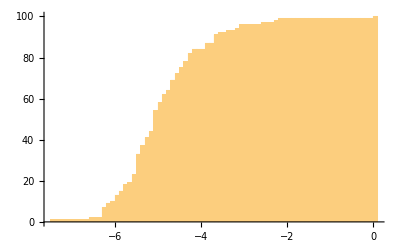

```mathematica
Histogram[Log[Abs[#]]&/@spec,{.1},"CumulativeCount"]
```

```mathematica
hlist=(specAbs=Sort[Log[Abs[#]]&/@spec];Join[{{specAbs_⟦1⟧-1,0}},Transpose[{specAbs,Table[n,{n,1,Length[specAbs]}]}],{{0,Length[specAbs]}}]);
```

```mathematica
StringJoin[Table["("<>ToString[N[hlist_⟦n,1⟧]]<>","<>ToString[hlist_⟦n,2⟧]<>")",{n,1,Length[hlist]}]]
```

(-8.49982,0)(-7.49982,1)(-6.57468,2)(-6.28342,3)(-6.28342,4)(-6.24956,5)(-6.23781,6)(-6.23781,7)(-6.17079,8)(-6.17079,9)(-6.00582,10)(-5.97637,11)(-5.95739,12)(-5.95739,13)(-5.89074,14)(-5.89074,15)(-5.79846,16)(-5.79846,17)(-5.74913,18)(-5.66313,19)(-5.58688,20)(-5.58688,21)(-5.52443,22)(-5.52443,23)(-5.47175,24)(-5.47175,25)(-5.46655,26)(-5.46655,27)(-5.46028,28)(-5.46028,29)(-5.45181,30)(-5.45181,31)(-5.42404,32)(-5.42404,33)(-5.35064,34)(-5.35064,35)(-5.3378,36)(-5.3378,37)(-5.28818,38)(-5.28818,39)(-5.28699,40)(-5.28699,41)(-5.16263,42)(-5.11905,43)(-5.11905,44)(-5.09987,45)(-5.09987,46)(-5.08381,47)(-5.08381,48)(-5.06254,49)(-5.06254,50)(-5.04676,51)(-5.04676,52)(-5.0166,53)(-5.0166,54)(-4.99715,55)(-4.99715,56)(-4.9509,57)(-4.9509,58)(-4.8452,59)(-4.8452,60)(-4.84111,61)(-4.84111,62)(-4.71034,63)(-4.71034,64)(-4.69904,65)(-4.68231,66)(-4.68231,67)(-4.61467,68)(-4.61467,69)(-4.59982,70)(-4.54088,71)(-4.54088,72)(-4.424,73)(-4.40516,74)(-4.40516,75)(-4.34072,76)(-4.34072,77)(-4.32812,78)(-4.21948,79)(-4.21948,80)(-4.21022,81)(-4.21022,82)(-4.13705,83)(-4.13705,84)(-3.89213,85)(-3.89213,86)(-3.81539,87)(-3.69615,88)(-3.69615,89)(-3.6951,90)(-3.6951,91)(-3.52704,92)(-3.33434,93)(-3.13425,94)(-3.05051,95)(-3.03428,96)(-2.57797,97)(-2.26838,98)(-2.15911,99)(0.,100)(0.,100)

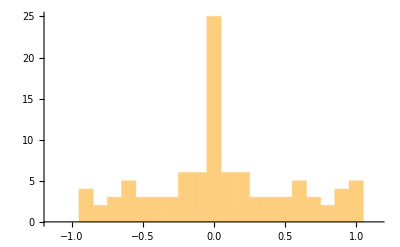

```mathematica
Histogram[Arg[#]/π&/@spec,{-1.15,1.15,.1}]
```

```mathematica
hlist=(specArg=Sort[Arg[#]/π&/@spec];Join[{{-1.15,0}},Transpose[{specArg,Table[n,{n,1,Length[specArg]}]}],{{1.05,Length[specArg]}}]);
```

```mathematica
StringJoin[Table["("<>ToString[N[hlist_⟦n,1⟧]]<>","<>ToString[hlist_⟦n,2⟧]<>")",{n,1,Length[hlist]}]]
```

(-1.15,0)(-0.922254,1)(-0.894558,2)(-0.889973,3)(-0.852779,4)(-0.803671,5)(-0.773516,6)(-0.726911,7)(-0.726047,8)(-0.673779,9)(-0.646574,10)(-0.633939,11)(-0.617409,12)(-0.607102,13)(-0.582182,14)(-0.505499,15)(-0.504322,16)(-0.478052,17)(-0.407333,18)(-0.374949,19)(-0.353254,20)(-0.328746,21)(-0.303329,22)(-0.274091,23)(-0.244027,24)(-0.231052,25)(-0.187175,26)(-0.164664,27)(-0.163434,28)(-0.150895,29)(-0.144832,30)(-0.134646,31)(-0.11801,32)(-0.0880681,33)(-0.0632854,34)(-0.0578634,35)(-0.0468788,36)(-0.0318364,37)(-0.01984,38)(-0.0127808,39)(0.,40)(0.,41)(0.,42)(0.,43)(0.,44)(0.,45)(0.,46)(0.,47)(0.,48)(0.,49)(0.,50)(0.,51)(0.,52)(0.,53)(0.,54)(0.,55)(0.,56)(0.0127808,57)(0.01984,58)(0.0318364,59)(0.0468788,60)(0.0578634,61)(0.0632854,62)(0.0880681,63)(0.11801,64)(0.134646,65)(0.144832,66)(0.150895,67)(0.163434,68)(0.164664,69)(0.187175,70)(0.231052,71)(0.244027,72)(0.274091,73)(0.303329,74)(0.328746,75)(0.353254,76)(0.374949,77)(0.407333,78)(0.478052,79)(0.504322,80)(0.505499,81)(0.582182,82)(0.607102,83)(0.617409,84)(0.633939,85)(0.646574,86)(0.673779,87)(0.726047,88)(0.726911,89)(0.773516,90)(0.803671,91)(0.852779,92)(0.889973,93)(0.894558,94)(0.922254,95)(1.,96)(1.,97)(1.,98)(1.,99)(1.,100)(1.05,100)

#### Preparations for [1, Fig. 4]

```mathematica
P=Pfi;
```

```mathematica
rP=#/Max[#]&/@Pfi;
```

```mathematica
Export["Pfi100.txt",StringRiffle[Table["\\put(0,"<>ToString[50-0.5*(i-1)]<>"){"<>StringJoin[Table[prep=ToExpression[ToString[TempRGB[rP_⟦i,j⟧]]];("\\pxl{"<>ToString[prep_⟦1⟧]<>"}{"<>ToString[prep_⟦2⟧]<>"}{"<>ToString[prep_⟦3⟧]<>"}"),{j,1,100}]]<>"}",{i,1,100}],"\n"]]
```

Pfi100.txt

```mathematica
v=Eigenvectors[Transpose[P],1];
```

```mathematica
u=Reverse[Sort[Total[Transpose[#_⟦1⟧]_⟦2⟧]&/@Take[NonStopClustersFinnish,100]]]
```

{819,737,564,522,507,441,394,368,356,324,321,313,310,289,287,286,285,276,263,250,248,237,236,233,232,226,222,219,219,213,212,208,205,204,195,195,186,185,179,175,169,166,163,161,158,147,145,143,141,136,135,133,133,133,133,131,130,130,129,127,125,125,125,124,123,117,115,113,113,108,108,106,101,100,99,98,97,96,95,95,95,94,94,93,93,93,93,91,91,91,90,89,88,86,86,86,86,85,85,85}

```mathematica
prep=N[u/Total[u]];StringJoin[Table["("<>ToString[n]<>","<>ToString[prep[[n]]]<>")",{n,1,N0}]]
```

(1,0.0431939)(2,0.0388693)(3,0.0297453)(4,0.0275302)(5,0.0267391)(6,0.0232583)(7,0.0207795)(8,0.0194083)(9,0.0187754)(10,0.0170877)(11,0.0169295)(12,0.0165076)(13,0.0163493)(14,0.0152418)(15,0.0151363)(16,0.0150836)(17,0.0150309)(18,0.0145562)(19,0.0138706)(20,0.013185)(21,0.0130795)(22,0.0124993)(23,0.0124466)(24,0.0122884)(25,0.0122356)(26,0.0119192)(27,0.0117082)(28,0.01155)(29,0.01155)(30,0.0112336)(31,0.0111808)(32,0.0109699)(33,0.0108117)(34,0.0107589)(35,0.0102843)(36,0.0102843)(37,0.00980961)(38,0.00975687)(39,0.00944043)(40,0.00922947)(41,0.00891303)(42,0.00875481)(43,0.00859659)(44,0.00849111)(45,0.00833289)(46,0.00775276)(47,0.00764728)(48,0.0075418)(49,0.00743632)(50,0.00717262)(51,0.00711988)(52,0.0070144)(53,0.0070144)(54,0.0070144)(55,0.0070144)(56,0.00690892)(57,0.00685618)(58,0.00685618)(59,0.00680344)(60,0.00669796)(61,0.00659248)(62,0.00659248)(63,0.00659248)(64,0.00653974)(65,0.006487)(66,0.00617056)(67,0.00606508)(68,0.0059596)(69,0.0059596)(70,0.0056959)(71,0.0056959)(72,0.00559042)(73,0.00532672)(74,0.00527398)(75,0.00522124)(76,0.0051685)(77,0.00511576)(78,0.00506302)(79,0.00501028)(80,0.00501028)(81,0.00501028)(82,0.00495754)(83,0.00495754)(84,0.0049048)(85,0.0049048)(86,0.0049048)(87,0.0049048)(88,0.00479932)(89,0.00479932)(90,0.00479932)(91,0.00474659)(92,0.00469385)(93,0.00464111)(94,0.00453563)(95,0.00453563)(96,0.00453563)(97,0.00453563)(98,0.00448289)(99,0.00448289)(100,0.00448289)

```mathematica
prep=N[v_⟦1⟧/Total[v_⟦1⟧]];StringJoin[Table["("<>ToString[n]<>","<>ToString[prep[[n]]]<>")",{n,1,N0}]]
```

(1,0.0436478)(2,0.0381381)(3,0.0292323)(4,0.0267428)(5,0.0262185)(6,0.0225923)(7,0.0194942)(8,0.0193118)(9,0.0186329)(10,0.0175622)(11,0.0184469)(12,0.018198)(13,0.0161305)(14,0.0155071)(15,0.0152171)(16,0.0154243)(17,0.015493)(18,0.014368)(19,0.0145542)(20,0.0127974)(21,0.0126003)(22,0.0120801)(23,0.0116307)(24,0.0119652)(25,0.0120413)(26,0.0118128)(27,0.0113375)(28,0.0118897)(29,0.0115768)(30,0.0112276)(31,0.0117948)(32,0.010837)(33,0.0109721)(34,0.0108095)(35,0.0102382)(36,0.00926583)(37,0.0102234)(38,0.00976988)(39,0.0089391)(40,0.0089825)(41,0.00875571)(42,0.00859877)(43,0.00916981)(44,0.00825353)(45,0.0092021)(46,0.00789441)(47,0.0084687)(48,0.00730555)(49,0.00747955)(50,0.0069902)(51,0.00720797)(52,0.00675654)(53,0.00688326)(54,0.00698714)(55,0.00710345)(56,0.00683773)(57,0.00678365)(58,0.007329)(59,0.00666263)(60,0.00654897)(61,0.0064671)(62,0.00636093)(63,0.00615393)(64,0.00653351)(65,0.00682843)(66,0.00648624)(67,0.00627237)(68,0.0060161)(69,0.00580035)(70,0.00556922)(71,0.00565559)(72,0.00567688)(73,0.00527083)(74,0.00515175)(75,0.00529578)(76,0.00520388)(77,0.0049135)(78,0.00503769)(79,0.00549806)(80,0.00511482)(81,0.00479642)(82,0.0051692)(83,0.00541788)(84,0.00499115)(85,0.00487932)(86,0.00498197)(87,0.00500327)(88,0.00491337)(89,0.00482511)(90,0.00468058)(91,0.00488219)(92,0.00449733)(93,0.00465429)(94,0.00443712)(95,0.00433663)(96,0.00447787)(97,0.00531816)(98,0.00431797)(99,0.00439214)(100,0.00479879)

```mathematica
1/Total[v_⟦1⟧] Sum[v_⟦1,i⟧*P_⟦i,j⟧,{i,1,N0},{j,1,N0}]
```

1.

```mathematica
StringJoin["("<>ToString[#_⟦1⟧]<>","<>ToString[AccountingForm[#_⟦2⟧]]<>")"&/@Table[M=MatrixPower[P,k];{k,1/2 Sum[Abs[1/Total[v_⟦1⟧] v_⟦1,i⟧*M_⟦i,j⟧-1/Total[v_⟦1⟧] v_⟦1,j⟧*M_⟦j,i⟧],{i,1,N0},{j,1,N0}]},{k,1,5}]]
```

(1,0.06639795644623)(2,0.00362907311593)(3,0.00033393352996)(4,0.0000345378326)(5,0.0000036886590)

### Data for topic patterns

```mathematica
TopicClusters=DeleteCases[NonStopClusters,{_,_,_,"B",_,_,_,_}];
```

```mathematica
Length[TopicClusters]
```

252

```mathematica
SelectedClusters=TopicClusters;
```

```mathematica
TopicClustersFinnish=TopicClusters;
```

```mathematica
Timing[PfiTopic=Table[Table[prepP=TransitionMeasure[SelectedClusters_⟦m,1⟧,SelectedClusters_⟦n,1⟧,SelectedClusters_⟦m,5⟧,SelectedClusters_⟦m,6⟧],{n,1,Length[SelectedClusters]}],{m,1,Length[SelectedClusters]}];]
```

{205.438,Null}

```mathematica
Timing[PfiT=Table[v=Table[prepP=PfiTopic_⟦m,n⟧;prepP_⟦1⟧*Exp[-prepP_⟦2⟧],{n,1,100}];v/Total[v],{m,1,100}];]
```

{0.046875,Null}

```mathematica
Timing[spec=Eigenvalues[PfiT];]
```

{1.3125,Null}

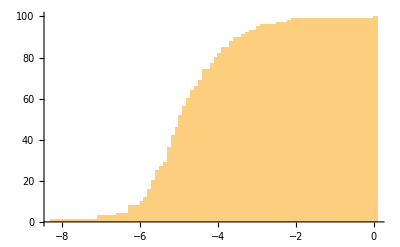

```mathematica
Histogram[Log[Abs[#]]&/@spec,{.1},"CumulativeCount"]
```

```mathematica
hlist=(specAbs=Sort[Log[Abs[#]]&/@spec];Join[{{specAbs_⟦1⟧-1,0}},Transpose[{specAbs,Table[n,{n,1,Length[specAbs]}]}],{{0.5,Length[specAbs]}}]);
```

```mathematica
StringJoin[Table["("<>ToString[N[hlist_⟦n,1⟧]]<>","<>ToString[hlist_⟦n,2⟧]<>")",{n,1,Length[hlist]}]]
```

(-9.26622,0)(-8.26622,1)(-7.02023,2)(-7.02023,3)(-6.55839,4)(-6.29289,5)(-6.251,6)(-6.251,7)(-6.20865,8)(-5.94282,9)(-5.94282,10)(-5.87532,11)(-5.87532,12)(-5.76453,13)(-5.76453,14)(-5.71285,15)(-5.71285,16)(-5.68061,17)(-5.68061,18)(-5.60007,19)(-5.60007,20)(-5.59977,21)(-5.57066,22)(-5.57066,23)(-5.54575,24)(-5.54575,25)(-5.49697,26)(-5.49697,27)(-5.38603,28)(-5.38603,29)(-5.2936,30)(-5.2936,31)(-5.28793,32)(-5.28793,33)(-5.26144,34)(-5.23195,35)(-5.23195,36)(-5.14732,37)(-5.14732,38)(-5.1149,39)(-5.1149,40)(-5.10695,41)(-5.10695,42)(-5.05028,43)(-5.05028,44)(-5.01295,45)(-5.01295,46)(-4.97251,47)(-4.97251,48)(-4.95111,49)(-4.95111,50)(-4.9333,51)(-4.9333,52)(-4.89949,53)(-4.89949,54)(-4.89916,55)(-4.89916,56)(-4.79717,57)(-4.79717,58)(-4.78584,59)(-4.78584,60)(-4.68358,61)(-4.68358,62)(-4.60484,63)(-4.60484,64)(-4.54841,65)(-4.54841,66)(-4.41627,67)(-4.40473,68)(-4.40473,69)(-4.36749,70)(-4.32798,71)(-4.32798,72)(-4.32315,73)(-4.32315,74)(-4.1938,75)(-4.18079,76)(-4.18079,77)(-4.07035,78)(-4.07035,79)(-4.05141,80)(-3.98374,81)(-3.98374,82)(-3.8685,83)(-3.8685,84)(-3.80742,85)(-3.60969,86)(-3.60671,87)(-3.60671,88)(-3.51927,89)(-3.51927,90)(-3.37186,91)(-3.22537,92)(-3.13175,93)(-2.93244,94)(-2.93244,95)(-2.85403,96)(-2.41045,97)(-2.14181,98)(-2.06435,99)(0.,100)(0.5,100)

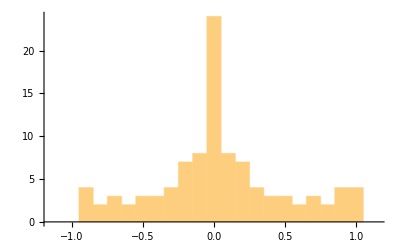

```mathematica
Histogram[Arg[#]/π&/@spec,{-1.15,1.15,.1}]
```

```mathematica
hlist=(specArg=Sort[Arg[#]/π&/@spec];Join[{{-1.15,0}},Transpose[{specArg,Table[n,{n,1,Length[specArg]}]}],{{1.5,Length[specArg]}}]);
```

```mathematica
StringJoin[Table["("<>ToString[N[hlist_⟦n,1⟧]]<>","<>ToString[hlist_⟦n,2⟧]<>")",{n,1,Length[hlist]}]]
```

(-1.15,0)(-0.943237,1)(-0.934988,2)(-0.869104,3)(-0.862347,4)(-0.776209,5)(-0.75236,6)(-0.742102,7)(-0.714718,8)(-0.699055,9)(-0.617324,10)(-0.57145,11)(-0.533631,12)(-0.532256,13)(-0.495253,14)(-0.433898,15)(-0.389484,16)(-0.360642,17)(-0.329125,18)(-0.301386,19)(-0.290262,20)(-0.275304,21)(-0.226995,22)(-0.223969,23)(-0.178443,24)(-0.178393,25)(-0.174799,26)(-0.154532,27)(-0.153741,28)(-0.124547,29)(-0.115725,30)(-0.107657,31)(-0.104084,32)(-0.0852491,33)(-0.0691199,34)(-0.0679383,35)(-0.0570473,36)(-0.046383,37)(-0.0439994,38)(-0.0396214,39)(-0.00935591,40)(0.,41)(0.,42)(0.,43)(0.,44)(0.,45)(0.,46)(0.,47)(0.,48)(0.,49)(0.,50)(0.,51)(0.,52)(0.,53)(0.,54)(0.,55)(0.,56)(0.00935591,57)(0.0396214,58)(0.0439994,59)(0.046383,60)(0.0570473,61)(0.0679383,62)(0.0691199,63)(0.0852491,64)(0.104084,65)(0.107657,66)(0.115725,67)(0.124547,68)(0.153741,69)(0.154532,70)(0.174799,71)(0.178393,72)(0.178443,73)(0.223969,74)(0.226995,75)(0.275304,76)(0.290262,77)(0.301386,78)(0.329125,79)(0.360642,80)(0.389484,81)(0.433898,82)(0.495253,83)(0.532256,84)(0.533631,85)(0.57145,86)(0.617324,87)(0.699055,88)(0.714718,89)(0.742102,90)(0.75236,91)(0.776209,92)(0.862347,93)(0.869104,94)(0.934988,95)(0.943237,96)(1.,97)(1.,98)(1.,99)(1.,100)(1.5,100)

### Preparations for [1, Fig. 5b]

```mathematica
SelectedTopics=Cases[TopicClustersFinnish,{{___,{#,_},___},___}]_⟦1⟧&/@TopicsNamesFinnish;
```

```mathematica
KinSpecSWLongTag[TopicClustersFinnish,PfiTopic,#_⟦1⟧&/@SelectedTopics]
```

Here are the lists of eigenvalues for the three selected topics:

```mathematica
FinnishKinQ0=KinQ0
```

{{0.96723722012185,0.22165672410777,0.12695005834066,0.090106066032207,0.04911534591006,0.04911534591006,0.043297945238484,0.043297945238484,0.036775692549757,0.030458465275922,0.018714515080743,0.018714515080743,0.018415866494757,0.018415866494757,0.012560544179913,0.011564433531638,0.0094501597361408,0.0069751674833815,0.0044532762588529,0.0044532762588529,0.00206510942694,0.00206510942694,0},{0.89232050756609,0.10753041850457,0.054668876763555,0.051004672134485,0.03775896860281,0.035406788123726,0.030566196125931,0.030566196125931,0.028330436838129,0.025956978606247,0.025956978606247,0.021810067181068,0.021810067181068,0.01767604397148,0.01767604397148,0.016667761747646,0.016667761747646,0.013736114092206,0.012821503854124,0.012821503854124,0.011889316966142,0.011889316966142,0.01109227012849,0.01109227012849,0.0097745829198002,0.0097745829198002,0.0081934332753858,0.0081934332753858,0.0079698972596963,0.0079698972596963,0.0068359960348615,0.0068359960348615,0.0062761746810509,0.0062761746810509,0.0060851822439449,0.0060851822439449,0.0050922468409732,0.0042509323012073,0.0042509323012073,0.0029686704488589,0.0029686704488589,0.0029539985870532,0.0029539985870532,0.000085142001922547,0},{0.79642007030382,0.10429802184007,0.10429802184007,0.064643611049429,0.046948441057535,0.046948441057535,0.037892433092715,0.037892433092715,0.032711648500065,0.026087181348153,0.02202968891922,0.02202968891922,0.021802410012509,0.016820352081775,0.016820352081775,0.015761075731388,0.015761075731388,0.013800562178716,0.013800562178716,0.010598744706667,0.0097112640587902,0.0097112640587902,0.0072613870040676,0.0072613870040676,0.007069594890628,0.007069594890628,0.0047789084577441,0.0047789084577441,0.0026389440394643,0.0026389440394643,0.0007604365166263,0.0007604365166263,0}}

```mathematica
FinnishKinQ=KinQ
```

{{0.96723722012185,0.22165672410777,0.12695005834066,0.090106066032207,0.04911534591006,0.04911534591006,0.043297945238484,0.043297945238484,0.036775692549757,0.030458465275922,0.018714515080743,0.018714515080743,0.018415866494757},{0.89232050756609,0.10753041850457,0.054668876763555,0.051004672134485,0.03775896860281,0.035406788123726,0.030566196125931,0.030566196125931,0.028330436838129,0.025956978606247,0.025956978606247,0.021810067181068,0.021810067181068,0.01767604397148,0.01767604397148,0.016667761747646,0.016667761747646,0.013736114092206,0.012821503854124,0.012821503854124,0.011889316966142,0.011889316966142},{0.79642007030382,0.10429802184007,0.10429802184007,0.064643611049429,0.046948441057535,0.046948441057535,0.037892433092715,0.037892433092715,0.032711648500065,0.026087181348153,0.02202968891922,0.02202968891922,0.021802410012509,0.016820352081775,0.016820352081775,0.015761075731388,0.015761075731388}}

```mathematica
TopicNames=TopicsNamesFinnish
```

{ylpeys,darcy,elizabeth}

```mathematica
Cl=TopicClustersFinnish;
```

```mathematica
PT=PfiTopic;
```

```mathematica
AffinitySmallWorlds=Table[PT_⟦SeekPos[TopicNames_⟦k⟧,Cl],TopicSmallWorlds_⟦k,j⟧,3⟧,{k,1,Length[TopicNames]},{j,1,Length[TopicSmallWorlds_⟦k⟧]}];
```

```mathematica
SmallWorldWeights=Table[v=Eigenvectors[Transpose[RenormPSW_⟦k⟧],1];prob=v_⟦1⟧/Total[v_⟦1⟧];Table[ReplacePart[Cl_⟦TopicSmallWorlds_⟦k,m⟧⟧,{2->prob_⟦m⟧,5->AffinitySmallWorlds_⟦k,m⟧}],{m,1,Length[RenormPSW_⟦k⟧]}],{k,1,Length[RenormPSW]}];
```

```mathematica
SortWordClusters[list_,ScalingFactor_,MaxClusters_]:=(AllCluster=Take[Sort[(prep=CensorCluster[#_⟦1⟧];{prep,#_⟦2⟧,Total[Transpose[prep]_⟦2⟧],#_⟦4⟧,#_⟦5⟧})&/@list,#1[[2]]>#2[[2]]&],UpTo[MaxClusters]];SizedWords=Table[Width=Total[Max/@StringLength[#_⟦2⟧&/@#&/@SplitEven[EvenOut[Transpose[AllCluster_⟦n,1⟧]]]]];ScalingFactor √(AllCluster_⟦n,2⟧/Width)*{Width*0.95,1/0.9},{n,1,Length[AllCluster]}];)
```

```mathematica
SmallWorldCloudPlot[ScalingFactor_,MaxClusters_,OutputFileName_]:=(FindCenter[SizedWords];MinX=Min[Table[CenterList_⟦n,1⟧-SizedWords_⟦n,1⟧/2,{n,1,Length[SizedWords]}]];MinY=Min[Table[CenterList_⟦n,2⟧-SizedWords_⟦n,2⟧/2,{n,1,Length[SizedWords]}]];MaxX=Max[Table[CenterList_⟦n,1⟧+SizedWords_⟦n,1⟧/2,{n,1,Length[SizedWords]}]];MaxY=Max[Table[CenterList_⟦n,2⟧+SizedWords_⟦n,2⟧/2,{n,1,Length[SizedWords]}]];ArrangedCluster=Table[WCCounts=Transpose[SortBy[AllCluster_⟦n,1⟧,First]];{SizedWords_⟦n⟧,WCCounts_⟦1⟧,WCCounts_⟦2⟧,AllCluster_⟦n,3⟧,AllCluster_⟦n,4⟧,CenterList_⟦n⟧,AllCluster_⟦n,5⟧},{n,1,Length[AllCluster]}];str=OpenWrite[OutputFileName];WriteString[str,"\\begin{minipage}{\\textwidth}\\fontfamily{pnc}\\selectfont\\begin{spacing}{0}\\begin{picture}("<>ToString[N[Round[MaxX-MinX,10^-3]]]<>","<>ToString[N[Round[MaxY-MinY,10^-3]]]<>"){\\textbf{"<>StringJoin[Table["\\put("<>ToString[N[Round[ArrangedCluster_⟦k,6,1⟧-ArrangedCluster_⟦k,1,1⟧/2,10^-3]]]<>","<>ToString[N[Round[ArrangedCluster_⟦k,6,2⟧-ArrangedCluster_⟦k,1,2⟧/2,10^-3]]]<>"){\\textcolor[rgb]"<>ToString[RainbowRGB[ArrangedCluster_⟦k,7⟧]]<>"{"<>"
\\setlength{\\unitlength}{"<>ToString[N[Round[0.85*2.54/72 ArrangedCluster_⟦k,1,2⟧,10^-3]]]<>"cm}{
"<>(BCData=Word2BarChart[{ArrangedCluster_⟦k,2⟧,ArrangedCluster_⟦k,3⟧}];H=ArrangedCluster_⟦k,4⟧;StringJoin[hpos=0;Table[hinc=Max[StringLength/@Transpose[BCData_⟦m⟧]_⟦2⟧];hpos=hpos+hinc;Table[If[(BCData_⟦m,n,2⟧==" ")||(BCData_⟦m,n,3⟧/H*0.85 ArrangedCluster_⟦k,1,2⟧*2.54/72<0.01),"","\\BC{"<>ToString[hpos-hinc]<>"}{"<>ToString[N[Round[BCData_⟦m,n,4⟧/H,10^-3]]]<>"}{"<>(ToString[hinc])<>"}{"<>(temp=ToUpperCase[BCData_⟦m,n,2⟧];ToString[N[Round[BCData_⟦m,n,3⟧/H*If[temp1=temp;RemoveDiacritics[temp1]==temp1,1,1.3],10^-3]]])<>"}{"<>(If[StringDelete[temp,CharacterRange["A","Z"]|"'"|"’"]=="",temp,StringReplace[StringReplace[ExportString[temp,"TeX"],___~~"\\[\\text{":>""],"}\\]"~~___:>""]])<>"}\n"],{n,1,Length[BCData_⟦m⟧]}],{m,1,Length[BCData]}]])<>"}}}
",{k,1,Length[ArrangedCluster]}]]<>"}}\\end{picture}\\end{spacing}\\end{minipage}"];Close[str];)
```

```mathematica
SortWordClusters[SmallWorldWeights_⟦1⟧,30,Length[SmallWorldWeights_⟦1⟧]];SmallWorldCloudPlot[1,20,"fi-pride.txt"];
```

```mathematica
SortWordClusters[SmallWorldWeights_⟦2⟧,30,Length[SmallWorldWeights_⟦2⟧]];SmallWorldCloudPlot[1,25,"fi-Darcy.txt"];
```

```mathematica
SortWordClusters[SmallWorldWeights_⟦3⟧,30,Length[SmallWorldWeights_⟦3⟧]];SmallWorldCloudPlot[1,25,"fi-Eliza.txt"];
```

### Word translation

#### Bulk vectors

```mathematica
EnglishRef=TopicClustersEnglish;
```

```mathematica
FinnishRef=TopicClustersFinnish;
```

```mathematica
PandPChapEnglish=StringSplit[ExampleData[{"Text","PrideAndPrejudice"}],"Chapter "~~DigitCharacter..~~" "];
```

```mathematica
Length[PandPChapEnglish]
```

61

```mathematica
VecEnglish=Table[{EnglishRef_⟦k,1⟧,StringCount[PandPChapEnglish,WordBoundary~~Alternatives@@(#_⟦1⟧&/@EnglishRef_⟦k,1⟧)~~WordBoundary,IgnoreCase->True]},{k,1,Length[EnglishRef]}];
```

```mathematica
PandPChapFinnish=StringReplace[ImportString[#,"HTML"]&/@StringReplace[StringSplit[Import["PandP_Finnish.txt"],WordBoundary~~("1"|"I"|"V"|"X"|"L")..~~" "~~"LUKU"~~""|"."~~"\n"],{"\n\n":>"垚"}],{"垚":>"\n\n"}];
```

```mathematica
Length[PandPChapFinnish]
```

61

```mathematica
VecFinnish=Table[{FinnishRef_⟦k,1⟧,StringCount[PandPChapFinnish,WordBoundary~~Alternatives@@(#_⟦1⟧&/@FinnishRef_⟦k,1⟧)~~WordBoundary,IgnoreCase->True]},{k,1,Length[FinnishRef]}];
```

```mathematica
FlatScreenedPairs=Flatten[Table[{#_⟦1⟧,#_⟦2,k⟧},{k,1,Length[#_⟦2⟧]}]&/@Select[Table[{EnglishRef[[k,1]],#_⟦1⟧&/@Select[VecFinnish,JaccardRuzickaSim[#_⟦2⟧,Cases[VecEnglish,{EnglishRef[[k,1]],___}]_⟦1,2⟧]≥Max[1-7/100*√61,1-√(Length[Select[Min[#]&/@Transpose[{#_⟦2⟧,Cases[VecEnglish,{EnglishRef[[k,1]],___}]_⟦1,2⟧}],#>0&]]/Total[Max[#]&/@Transpose[{#_⟦2⟧,Cases[VecEnglish,{EnglishRef[[k,1]],___}]_⟦1,2⟧}]])]&]},{k,1,Length[EnglishRef]}],Length[#_⟦2⟧]>0&],1];
```

```mathematica
SiftedTags=Union[(#_⟦1⟧&/@FlatScreenedPairs)];SiftedEnglishRef=Reverse[SortBy[Table[Cases[EnglishRef,{SiftedTags[[k]],___}]_⟦1⟧,{k,1,Length[SiftedTags]}],#_⟦3⟧&]];
```

```mathematica
SiftedTags=Union[(#_⟦2⟧&/@FlatScreenedPairs)];SiftedFinnishRef=Reverse[SortBy[Table[Cases[FinnishRef,{SiftedTags[[k]],___}]_⟦1⟧,{k,1,Length[SiftedTags]}],#_⟦3⟧&]];
```

```mathematica
Length[SiftedEnglishRef]
```

85

```mathematica
Length[SiftedFinnishRef]
```

84

#### Spectral parameters for English

```mathematica
FromTopics=SiftedEnglishRef;
```

```mathematica
FromDelta=ReadDelta[#]&/@FromTopics;
```

```mathematica
FromN=(#_⟦3⟧-1)&/@FromTopics;
```

```mathematica
AbsoluteTiming[KinSpecSWLongTag[TopicClustersEnglish,PenTopic,#_⟦1⟧&/@FromTopics];]
```

{45.8354,Null}

```mathematica
FromKinQ=KinQ;
```

```mathematica
FromEta=SemanticComplexities;
```

#### Spectral parameters for Finnish

```mathematica
ToTopicsFinnish=SiftedFinnishRef;
```

```mathematica
Length[ToTopicsFinnish]
```

84

```mathematica
ToDeltaFinnish=ReadDelta[#]&/@ToTopicsFinnish;
```

```mathematica
ToNFinnish=(#_⟦3⟧-1)&/@ToTopicsFinnish;
```

```mathematica
AbsoluteTiming[KinSpecSWLongTag[TopicClustersFinnish,PfiTopic,#_⟦1⟧&/@ToTopicsFinnish];]
```

{120.802,Null}

```mathematica
ToKinFinnish=KinQ;
```

```mathematica
ToEtaFinnish=SemanticComplexities;
```

#### Translation

```mathematica
AbsoluteTiming[fromLabeled=Transpose[{#_⟦1⟧&/@FromTopics,FromKinQ}];toLabeled=Transpose[{#_⟦1⟧&/@ToTopicsFinnish,ToKinFinnish}];Report=Table[{FlatScreenedPairs_⟦k⟧,(JaccardRuzickaSim[Cases[fromLabeled,{FlatScreenedPairs_⟦k,1⟧,_}]_⟦1,2⟧,Cases[toLabeled,{FlatScreenedPairs_⟦k,2⟧,_}]_⟦1,2⟧])},{k,1,Length[FlatScreenedPairs]}];]
```

{0.0126346,Null}

```mathematica
prep=Union[Select[Table[{Report_⟦n,1,1⟧,Report_⟦n,1,2⟧,Report_⟦n,2⟧},{n,1,Length[Report]}],#_⟦3⟧≥0.7&]];g=Graph[(#_⟦1⟧->#_⟦2⟧)&/@prep,EdgeWeight->(#_⟦3⟧&/@prep)];(KuhnSln={#,FindRowRank[#,prep],FindColRank[#,prep]}&/@Select[{#,PropertyValue[{g,#},EdgeWeight]}&/@FindIndependentEdgeSet[g],#_⟦2⟧>0&])//TableForm
```

{{de,39}}->{{de,36}}
0.93188175333518 | 2 | 2
{{Bourgh,35},{Bourgh's,4}}->{{bourgh,14},{bourghia,1},{bourghiin,1},{bourghin,21}}
0.947222877502 | 1 | 1
{{five,30}}->{{viilenemään,1},{vii,1},{viiltävää,1},{viisi,13},{viisikö,2},{viitsitte,1},{viii,1},{viitsi,2},{viitsinyt,2},{viitata,1},{viitsitkään,1},{viittasit,1},{viittä,2},{viittäkään,1},{viittailla,1},{viittaillutkaan,1},{viideltä,3},{viidessä,2},{viidestä,1},{viiden,4},{viidennen,1},{viidentoistavuotias,1},{viidakkoa,1}}
0.73271673040031 | 1 | 1
{{impossible,44}}->{{mahdoton,18},{mahdotonta,12},{mahdotontahan,3},{mahdottomaksi,5},{mahdottomalla,1},{mahdottomalta,1},{mahdottomat,1},{mahdottomiksi,1}}
0.88032155965137 | 1 | 1
{{library,23}}->{{kirjasto,2},{kirjastonsa,2},{kirjastossa,5},{kirjastossani,1},{kirjastoonsa,2},{kirjastoa,3},{kirjaston,1},{kirjastoon,6}}
0.8663021960466 | 1 | 1
{{town,64}}->{{lontoolainen,1},{lontoolaisen,1},{lontoossa,30},{lontoossakin,1},{lontoosta,15},{lontoon,11},{lontooseen,32},{lontoota,2}}
0.86944068999923 | 1 | 1
{{Meryton,57}}->{{merytonissa,18},{merytonista,7},{meryton,2},{merytonia,1},{merytoniin,17},{merytonin,7}}
0.80089923042033 | 1 | 1
{{money,26}}->{{rahoja,5},{rahoille,1},{rahoillesi,1},{raha,5},{rahallisen,1},{rahalliset,1},{rahallisista,1},{rahansa,1},{rahaa,3},{rahana,1},{rahat,2}}
0.8928230633564 | 1 | 1
{{Mr,786}}->{{herroja,1},{herrojen,4},{herra,269},{herrako,1},{herralle,2},{herrani,7},{herrasta,3},{hra,486},{herraa,4},{herraan,1},{herrain,5},{herran,14},{herrat,19},{herroista,3}}
0.84098429138968 | 1 | 1
{{Mrs,343}}->{{naapurinrouville,1},{rouva,79},{rouvaksi,1},{rouvalle,2},{rouvani,6},{rouvansa,1},{rouvasta,1},{rva,223},{rouvaa,1},{rouvan,6},{rouvana,2},{rouvat,1}}
0.90558341063529 | 1 | 1
{{Netherfield,73}}->{{netherfield,4},{netherfieldissä,16},{netherfieldistä,8},{netherfieldiä,2},{netherfieldiin,14},{netherfieldin,25}}
0.89367352425547 | 1 | 1
{{oh,95}}->{{ah,63},{ahaa,2},{ahneen,1},{ahtaalla,1},{ahtaasta,1}}
0.7505862065719 | 1 | 1
{{park,22}}->{{puisto,4},{puistolla,1},{puistossa,2},{puistoa,1},{puiston,11},{puistoon,2}}
0.80011937998706 | 1 | 1
{{Pemberley,53}}->{{pemberley,7},{pemberleyssä,12},{pemberleyn,16},{pemberleytä,1},{pemberleyhin,8}}
0.84640075229755 | 1 | 1
{{thousand,34}}->{{puntaan,3},{puntaa,20},{puntaakaan,1}}
0.87658146471975 | 1 | 1
{{Rosings,49}}->{{rosingsin,12},{rosingsissa,12},{rosingsista,2},{rosingista,1},{rosings,2},{rosingsiin,8}}
0.89358047735553 | 1 | 1
{{sir,78}}->{{sir,44}}
0.92057883109465 | 1 | 2
{{Catherine,110},{Catherine's,16}}->{{lady,130}}
0.93902730148599 | 1 | 1
{{Charlotte,68},{Charlotte's,17}}->{{charlotte,50},{charlottelle,2},{charlottelta,3},{charlotteni,2},{charlottensa,3},{charlottea,4},{charlotteani,1},{charlotteen,2},{charlotten,19}}
0.9565914248985 | 1 | 1
{{Collins,156},{Collins's,24}}->{{collinsilla,3},{collinsille,10},{collinsillekin,1},{collinsilta,7},{collinsin,51},{collinsista,2},{collinsit,2},{collins,101},{collinseilta,1},{collinsia,7},{collinsinkin,1}}
0.85808943380445 | 1 | 1
{{colonel,65},{colonel's,1}}->{{eversti,61},{everstin,3},{everstinsä,1},{everstiltä,1}}
0.77903076256188 | 1 | 1
{{Darcy,374},{Darcy's,44}}->{{darcyyn,19},{darcy,259},{darcykaan,1},{darcykin,1},{darcyko,1},{darcylainen,1},{darcylla,4},{darcylle,22},{darcylta,2},{darcyssa,3},{darcysta,10},{darcystako,1},{darcya,32},{darcyn,161},{darcynkaan,1},{darcynkin,3},{darcynko,1}}
0.90690213395448 | 1 | 1
{{face,27},{faces,3}}->{{kasvonsa,4},{kasvoi,5},{kasvoilla,1},{kasvoillaan,3},{kasvoillasi,1},{kasvoilta,2},{kasvoiltaan,1},{kasvoissaan,1},{kasvoja,2},{kasvojaan,1},{kasvojensa,1},{kasvot,11},{kasvoihinsa,1},{kasvoihin,5}}
0.83428029400806 | 1 | 1
{{father,116},{father's,19}}->{{isä,54},{isällä,1},{isällään,1},{isällänne,1},{isälle,1},{isälleen,1},{isällinen,1},{isällisen,1},{isällisestä,1},{isältään,3},{isältänne,1},{isämme,1},{isäni,19},{isänikin,1},{isänne,6},{isännekin,1},{isänsä,45},{isäsi,8},{isästä,3},{isästään,1},{isävainajan,1},{isävainajani,3},{isävainajansa,1},{isää,3},{isääkään,1},{isääni,1},{isäänsä,10},{isääsi,1},{isät,1},{isien,1},{isän,11}}
0.91083214323477 | 1 | 1
{{Jane,263},{Jane's,28}}->{{jane,151},{janehan,1},{janekaan,1},{janekin,6},{janella,8},{janelle,22},{janellekin,1},{janelta,3},{janemme,1},{janeni,3},{janensa,1},{janessa,1},{janesta,7},{janea,24},{janeakin,1},{janeen,11},{janen,69},{janenkin,2}}
0.88214491116714 | 1 | 1
{{Kitty,69},{Kitty's,2}}->{{kitty,45},{kittykin,2},{kittylle,5},{kittystä,1},{kittyä,2},{kittyn,7}}
0.91890321929882 | 1 | 1
{{Lizzy,95},{Lizzy's,2}}->{{lizzy,78},{lizzyä,6},{lizzyllä,1},{lizzylle,1},{lizzyn,5},{lizzyni,3},{lizzystä,1}}
0.94165203309482 | 1 | 1
{{Lydia,133},{Lydia's,38}}->{{lydia,85},{lydialla,3},{lydiallakin,1},{lydialle,6},{lydialta,1},{lydiassa,1},{lydiaa,9},{lydiaakin,1},{lydiaan,2},{lydian,52},{lydiata,2}}
0.91239446441295 | 1 | 1
{{Mary,38},{Mary's,1}}->{{mary,27},{marykin,1},{marylla,2},{marya,1},{maryn,7}}
0.78198930002903 | 1 | 1
{{ten,33},{tens,1}}->{{kymmeneltä,1},{kymmeneen,2},{kymmenen,12},{kymmenenkään,1},{kymmenenkin,1},{kymmenien,1},{kymmenentuhatta,3},{kymmenentuhannen,1}}
0.86921113644586 | 1 | 1
{{way,108},{ways,3}}->{{ajatukseen,2},{ajatuksen,1},{ajatukseni,6},{ajatuksenne,1},{ajatuksensa,11},{ajatuksesi,1},{ajatukset,14},{ajatuksia,2},{ajatuksiaan,4},{ajatuksianne,1},{ajatuksiin,3},{ajatuksiinsa,3},{ajatusta,3},{ajatustaan,2},{ajatustani,1},{ajatustasi,1},{ajatustensa,3},{ajatustesi,1},{ajatuksesta,3},{ajatus,19},{ajatuksella,1},{ajatuksille,1},{ajatuksilleen,1},{ajatuksissaan,3},{ajatuksistamme,1},{ajatuksistani,2}}
0.76156676524636 | 1 | 1
{{week,29},{weeks,18}}->{{viikkoon,1},{viikko,2},{viikkoa,10},{viikkoakaan,1},{viikoksi,2},{viikolla,8},{viikolta,1},{viikossa,3},{viikon,28},{viikot,1},{viikkoja,2},{viikkojen,1},{viikkona,2}}
0.78467459579391 | 1 | 1
{{Wickham,162},{Wickham's,32}}->{{wickhamiin,7},{wickhamin,78},{wickhaminkin,1},{wickhamkin,1},{wickham,87},{wickhamiksi,1},{wickhamilla,6},{wickhamille,7},{wickhamilta,1},{wickhaminsa,1},{wickhamista,13},{wickhamia,17},{wickhamiani,2}}
0.82506480612736 | 1 | 1
{{William,40},{William's,6}}->{{williamin,10},{williaminkaan,1},{williaminkin,1},{william,27},{williamilla,1},{williamille,1},{williamia,1},{williamkaan,1}}
0.95000790871937 | 1 | 1
{{window,16},{windows,6}}->{{akkunaan,5},{akkunassa,1},{akkunasta,11},{akkunan,4},{akkunathan,1},{akkunoista,3}}
0.86770384078184 | 1 | 1
{{aunt,78},{aunt's,6},{aunts,1}}->{{tädiksi,1},{tädilläkin,1},{tädilleen,2},{tädiltä,2},{tädiltään,1},{tädiltäkin,1},{tädiltäsi,1},{tädistä,1},{täti,41},{tätini,1},{tätinne,1},{tätinsä,16},{tätinsäkin,1},{tätisi,1},{tätiä,3},{tätiäni,1},{tätiään,3},{tätilässä,1},{tädin,15},{tädinkin,1}}
0.86975414572314 | 1 | 1
{{Bennet,294},{Bennet's,29},{Bennets,10}}->{{bennet,189},{bennetkin,2},{bennetillä,6},{bennetille,11},{bennetillekin,1},{bennetiltä,2},{bennetistä,1},{bennetiä,10},{bennetiin,2},{bennetin,62},{bennetinkin,1}}
0.91039224611326 | 1 | 1
{{child,14},{children,25},{childhood,1}}->{{lapsiparka,1},{lapsiparvensa,2},{lapsirukat,1},{lapsellisemmat,1},{lapselliset,1},{lapsellista,1},{lapseni,9},{lapsensa,3},{lapsena,3},{lapset,2},{lapsi,1},{lapsikin,1},{lapsilla,1},{lapsille,1},{lapsiltasi,1},{lapsista,1},{lapsistaan,1},{lapsia,4},{lapsiani,1},{lapsiasi,1},{lapsiaan,1},{lapsiin,1},{lapsina,1},{lapsineen,2},{lapsuudesta,1},{lapsuudestaan,1},{lapsuudestani,1},{lapsuuden,1},{lapsuutensa,2}}
0.83933434955478 | 1 | 1
{{cousin,41},{cousin's,8},{cousins,11}}->{{serkukset,2},{serkulleen,3},{serkulleni,1},{serkultani,1},{serkuksesta,1},{serkuilleen,1},{serkuistaan,1},{serkun,3},{serkku,5},{serkkuni,10},{serkkunne,4},{serkkunsa,20},{serkkuuni,1},{serkkuunsa,1},{serkkuakaan,1},{serkkuamme,1},{serkkuani,2},{serkkuansa,1},{serkkuaan,3},{serkkujeni,1},{serkkujensa,1},{serkkuihini,1}}
0.9135237669518 | 1 | 1
{{Eliza,22},{Elizabeth,597},{Elizabeth's,38}}->{{eliza,20},{elizabeth,486},{elizabethia,39},{elizabethiin,6},{elizabethilla,14},{elizabethille,32},{elizabethilta,7},{elizabethin,114},{elizabethini,1},{elizabethinkin,1},{elizabethinne,1},{elizabethista,11},{elizabethkään,1},{elizabethkin,3},{elizan,1}}
0.80255751167151 | 1 | 1
{{evening,72},{evening's,2},{evenings,4}}->{{ilta,11},{iltaan,2},{iltansa,1},{iltaa,10},{iltaansa,2},{iltana,17},{illaksi,2},{illalla,23},{illasta,1},{illan,10},{illat,2}}
0.85274294049853 | 1 | 1
{{Forster,38},{Forster's,1},{Forsters,1}}->{{forster,17},{forstereilla,1},{forsterilla,1},{forsterille,3},{forsterilta,2},{forsteritkin,1},{forsteria,4},{forsteriin,1},{forsterin,5}}
0.78486745775826 | 1 | 1
{{Gardiner,84},{Gardiner's,13},{Gardiners,6}}->{{gardiner,46},{gardinereilta,1},{gardinerilla,2},{gardinerille,4},{gardinerilta,3},{gardinerit,4},{gardineria,2},{gardinerin,21},{gardinerkin,1}}
0.93282540374836 | 1 | 1
{{letter,115},{letters,16},{letter-paper,1}}->{{kirjeenkirjoittajan,1},{kirje,19},{kirjeeseen,5},{kirjeeseeni,1},{kirjeeni,2},{kirjeensä,5},{kirjeesi,3},{kirjeessä,3},{kirjeessään,5},{kirjeessäni,1},{kirjeessäsi,1},{kirjeestä,3},{kirjeestään,1},{kirjeen,59},{kirjeet,6},{kirjeissä,1},{kirjeiden,1},{kirjettä,15},{kirjettään,1},{kirjettäni,1},{kirjeisiinsä,1},{kirjeitä,5},{kirjeitään,1}}
0.79970630396896 | 1 | 1
{{man,145},{man's,5},{men,33}}->{{miestä,23},{miestään,1},{miestänsä,1},{miesten,7},{mies,82},{mieheksesi,1},{mieheksi,8},{miehellä,5},{miehelle,5},{miehelleen,3},{mieheltä,2},{mieheni,1},{miehensä,26},{miehesi,2},{miehessä,2},{miehestä,11},{miehestään,1},{miehestäni,1},{mieheensä,2},{mieheen,5},{miehen,63},{miehenä,2},{miehet,4},{miehillä,1},{miehistä,2},{miehiä,9},{miehiin,4},{miehisestä,1},{miehekkäästä,1}}
0.79733887079998 | 1 | 1
{{maternal,2},{mother,110},{mother's,25}}->{{äitiensä,1},{äitikullan,1},{äitikulta,1},{äiti,51},{äitikin,1},{äitimme,1},{äitini,1},{äitinne,9},{äitinnekin,1},{äitinsä,46},{äitinsäkin,1},{äitisi,2},{äitiinsä,1},{äitiä,1},{äitiäsi,1},{äitiään,4}}
0.93025506900614 | 1 | 1
{{nephew,20},{nephew's,2},{nephews,2}}->{{sisarenpoika,1},{sisarenpoikaani,3},{sisarenpoikaansa,1},{sisarenpoikainsa,1},{sisarenpoikani,5},{sisarenpoikanne,3},{sisarenpoikansa,5},{sisarenpoikia,1},{sisarenpojallanne,1},{sisarenpojalleen,1},{sisarenpojalta,1},{sisarenpojan,2},{sisarenpojasta,1}}
0.82598489616291 | 1 | 1
{{Phillip's,1},{Phillips,26},{Phillips's,5}}->{{philipsille,3},{philipsillekin,1},{philipsin,10},{philips,12},{philipsiä,1}}
0.8543603934479 | 1 | 1
{{read,40},{reading,14},{reader,3}}->{{lue,4},{luet,1},{luettiin,2},{luit,1},{luki,8},{lukiessaan,3},{lukiessasi,1},{lukien,1},{lukiessa,1},{lukemisesta,4},{lukenut,4},{lukevat,1},{lukea,10},{lukeakseni,1},{luen,2},{lukemalla,1},{lukemallaan,1},{lukemaansa,1},{lukemaan,6},{lukemistaan,3}}
0.85569550621669 | 1 | 1
{{sat,38},{sit,15},{sitting,20}}->{{istukaamme,1},{istumme,1},{istunut,7},{istuttiin,1},{istuva,1},{istuu,1},{istua,5},{istualtani,1},{istuessa,2},{istuessaan,2},{istuen,1},{istui,23},{istuisi,1},{istuisiko,1},{istuisit,1},{istuivat,7},{istuin,1},{istumaan,11},{istut,1},{istuimeltaan,1}}
0.8481972642818 | 1 | 1
{{uncle,59},{uncle's,9},{uncles,3}}->{{eno,11},{enoa,2},{enoaan,2},{enoko,1},{enolaiset,1},{enolla,1},{enolleen,1},{enollesi,2},{enolta,2},{enoltaan,1},{enoltasi,1},{enomme,1},{enon,17},{enoni,2},{enonne,6},{enonsa,7},{enoon,1},{enosi,11}}
0.89070382882402 | 1 | 1
{{wife,44},{wife's,3},{wives,1}}->{{vaimo,4},{vaimoksi,5},{vaimolla,1},{vaimolleen,5},{vaimolleni,1},{vaimoltaan,2},{vaimonne,1},{vaimonsa,28},{vaimonsakaan,1},{vaimonsakin,1},{vaimosi,1},{vaimostaan,1},{vaimoa,2},{vaimoani,2},{vaimoaan,1},{vaimon,3},{vaimona,1}}
0.89551419073803 | 1 | 1
{{year,28},{years,33},{years',2}}->{{kuolinvuoteen,1},{puolivuoden,1},{vuositulonne,1},{vuositulonsa,1},{vuosituloilla,1},{vuosituloja,3},{vuositulot,4},{vuoden,9},{vuodessa,8},{vuodet,2},{vuonna,3},{vuosi,4},{vuosilta,1},{vuoteen,3},{vuotena,1},{vuosia,1},{vuotta,14},{vuosiin,1},{vuosittain,1}}
0.81929649813623 | 1 | 1
{{young,130},{younger,30},{youngest,13}}->{{nuoruuttaan,1},{nuoruuttamme,1},{nuoreksi,1},{nuorella,2},{nuorelle,4},{nuorelta,1},{nuoresta,6},{nuoreen,3},{nuoremmalta,1},{nuoremman,7},{nuoremmat,6},{nuoremmille,1},{nuoremmilta,1},{nuoremmista,3},{nuorempaa,1},{nuorempi,6},{nuorempia,1},{nuorempien,2},{nuorempiin,1},{nuoren,37},{nuorena,1},{nuoret,7},{nuori,41},{nuorilla,2},{nuorille,3},{nuorista,3},{nuoria,10},{nuorien,1},{nuoriin,2},{nuorimman,2},{nuorimmat,6},{nuorimmille,1},{nuorimmista,1},{nuorimpien,1},{nuorin,6},{nuorta,11},{nuoruutta,1},{nuoruudeltaan,1},{nuoruudessani,1},{nuoruudesta,1},{nuoruuden,2},{nuoruudenaikaisia,1},{nuoruutensa,1},{nuorempain,3}}
0.79133403939968 | 1 | 1
{{Bingley,257},{Bingley's,49},{Bingleys,4},{Bingleys',1}}->{{bingley,173},{bingleyksi,1},{bingleyllä,4},{bingleylle,5},{bingleyltä,4},{bingleymme,1},{bingleystä,11},{bingleystäkin,1},{bingleyn,93},{bingleynkään,1},{bingleynkin,2},{bingleytä,18},{bingleytäkin,2},{bingleyhin,5}}
0.87173712031071 | 1 | 1
{{brother,62},{brotherly,2},{brother's,13},{brothers,2}}->{{veljeksi,1},{veljelleen,1},{veljeni,5},{veljensä,39},{veljestä,1},{veljestään,1},{veljeään,3},{veli,7},{veljen,5},{veljenä,1},{veljiä,1}}
0.80106523557428 | 1 | 1
{{daily,3},{day,130},{day's,4},{days,30}}->{{päivä,30},{päivät,12},{päiväksi,3},{päivällinen,2},{päivällisajaksi,1},{päivällisajan,1},{päivälliseksi,1},{päivällisellä,2},{päivälliselle,9},{päivällisemme,1},{päivällisen,5},{päivälliset,1},{päivällisiä,1},{päivällisillä,5},{päivällisille,10},{päivällisiltä,1},{päivälliskutsu,2},{päivälliskutsua,1},{päivällispöydän,1},{päivällispöydässä,5},{päivällispöydässäkin,1},{päivällispöydästä,2},{päivällispöytään,2},{päivällistä,7},{päivällisvieraiksemme,1},{päivällisvieraina,1},{päivältä,1},{päiväni,1},{päivässä,4},{päivästä,4},{päivätty,1},{päivää,17},{päivään,1},{päivän,25},{päivänä,30},{päiviksi,3},{päivillä,1},{päivistä,1},{päiviä,6},{päiviäni,6},{päiviin,1},{päivinä,1},{päivitellä,1},{päivämäärä,1}}
0.88917227012132 | 1 | 1
{{daughter,78},{daughter's,7},{daughters,49},{daughters',1}}->{{tytärparvessa,1},{tytär,8},{tyttärellään,1},{tyttärelleen,6},{tyttärellesi,2},{tyttäreltä,1},{tyttäreltään,2},{tyttäremme,2},{tyttäreni,4},{tyttärenne,9},{tyttärensä,51},{tyttärensäkään,1},{tyttäresi,1},{tyttärestä,1},{tyttärestänne,1},{tyttärestäsi,1},{tyttäreenne,1},{tyttäreen,1},{tyttären,1},{tyttäret,6},{tyttärilleen,3},{tyttärillenne,1},{tyttäristä,1},{tyttäristään,4},{tyttäristämme,2},{tyttäristäni,4},{tyttäriinsä,1},{tyttäriä,1},{tyttäriäsi,2},{tyttärieni,1},{tyttäriensä,6},{tyttärien,1},{tyttärienkin,1},{tyttärineen,2},{tytärtä,9},{tytärtään,8},{tytärtäni,3},{tytärtänne,1},{tytärtenne,1},{tytärtensä,3},{tytärten,2}}
0.89366791464709 | 1 | 1
{{honour,42},{honoured,9},{honours,2},{honourable,6}}->{{maakunnassa,1},{valtakuntaani,1},{valtakunnan,1},{kuninkaan,1},{kunnaan,1},{kunnia,15},{kunniaksi,3},{kunnialla,1},{kunniallisella,1},{kunniani,4},{kunniassa,1},{kunniasta,2},{kunniaa,9},{kunniaan,1},{kunnian,6},{kunnianarvoisista,1},{kunnianarvoinen,3},{kunnianarvoisa,1},{kunnianarvoisasta,1},{kunnianarvoisan,1},{kunnianarvoisempaa,1},{kunnianarvoisen,2}}
0.85348595685921 | 1 | 1
{{Lucas,65},{Lucas's,5},{Lucases,13},{Lucases',1}}->{{lucasille,6},{lucasin,23},{lucasta,1},{lucasten,2},{lucas,41},{lucaseilta,1},{lucasia,2},{lucasinkin,1},{lucaskaan,1},{lucaskin,1}}
0.91819610881733 | 1 | 1
{{promise,17},{promised,21},{promises,3},{promising,4}}->{{lupaukseen,1},{lupauksellaan,1},{lupauksen,2},{lupaukseni,2},{lupauksensa,1},{lupausta,1},{lupaustaan,2},{lupaustani,1},{lupaustanne,1},{lupausten,1},{lupaus,2},{lupauksestaan,1},{lupa,1},{lupasi,12},{lupasin,1},{lupasit,2},{lupasitte,1},{lupasivat,1},{luvalliset,1},{luvattu,1},{lupaa,8},{lupaava,1},{lupaavat,2},{lupaama,1},{lupaamalla,1},{lupaamasi,1},{lupaamaansa,2},{lupaan,2},{lupaatteko,1},{luvan,1},{luvannut,6},{luvata,5},{luvatessaan,1},{luvaten,2}}
0.93695969168025 | 1 | 1
{{turn,27},{turned,43},{turning,13},{turns,2}}->{{hymyyn,3},{hymähti,1},{hymy,6},{hymyllä,1},{hymyllään,1},{hymynsä,2},{hymyä,2},{hymyään,3},{hymyilee,1},{hymyilemästä,1},{hymyilemään,3},{hymyilemäänkin,1},{hymyilemättä,3},{hymyilevän,3},{hymyili,11},{hymyilivät,4},{hymyilytti,1},{hymyin,1},{hymyillen,22},{hymyistään,1}}
0.82222727547396 | 1 | 1
{{believed,37},{believing,12},{belief,15},{believe,87},{believes,1}}->{{usko,17},{uskokaa,2},{uskokaan,2},{uskollinen,3},{uskollisena,1},{uskollisesta,1},{uskonut,8},{uskossa,1},{uskosta,1},{uskottiin,1},{uskottu,1},{uskovat,1},{uskoa,40},{uskoakaan,6},{uskoakseen,1},{uskoasi,1},{uskoaan,1},{uskomasta,2},{uskomaan,6},{uskomatta,1},{uskon,12},{uskonpa,1},{uskotella,5},{uskotellut,1},{uskoen,1},{uskoi,5},{uskoisi,2},{uskoitte,1},{uskoin,4},{uskoit,1},{uskokaahan,1}}
0.86343511936478 | 1 | 1
{{carriage,44},{carriages,6},{carried,8},{carry,5},{carrying,4}}->{{vaununsa,3},{vaunutarjouksensa,1},{vaunuilla,5},{vaunuillaan,1},{vaunuille,1},{vaunuissa,1},{vaunuissani,1},{vaunuista,2},{vaunuja,5},{vaunujakin,1},{vaunujen,11},{vaunut,12},{vaunuihini,1},{vaunuihinsa,1},{vaunuihin,6}}
0.87971337134664 | 1 | 1
{{congratulate,7},{congratulated,2},{congratulation,1},{congratulations,12},{congratulatory,1}}->{{onnittelemalla,1},{onnittelemaan,1},{onnittelen,2},{onnitteli,6},{onnittelisin,1},{onnitteluksi,1},{onnittelunsa,3},{onnitteluin,1},{onnitteluja,5},{onnittelujaan,2},{onnittelut,3}}
0.75074079326201 | 1 | 1
{{happily,5},{happiness,72},{happy,83},{happier,3},{happiest,10}}->{{onnekseen,1},{onneksi,10},{onnellaan,1},{onnelleni,1},{onnellinen,22},{onnelliseksi,22},{onnelliselta,1},{onnellisemmassa,1},{onnellisempaa,1},{onnellisempi,1},{onnellisena,3},{onnellisessa,1},{onnellisesta,5},{onnellisesti,3},{onnellisia,2},{onnellisimmaksi,1},{onnellisin,8},{onnellisina,1},{onnellisissa,1},{onnellisista,1},{onnellista,4},{onnellisuuden,4},{onnellisuudesta,1},{onnellisuudestaan,1},{onnellisuus,3},{onnellisuutensa,1},{onnellisuutesi,1},{onnellisuuttaan,1},{onnellisuuttansa,1},{onnemme,1},{onnensa,7},{onnesta,9},{onnestaan,5},{onnestani,2},{onneensa,1},{onnea,23},{onneani,1},{onneanne,1},{onneapa,1},{onneaan,4},{onneen,1},{onnen,6}}
0.78289513268077 | 1 | 1
{{invite,6},{invited,11},{inviting,3},{invitation,34},{invitations,1}}->{{vieraskutsujen,1},{kutsu,5},{kutsunne,1},{kutsunut,1},{kutsusta,2},{kutsuttiin,3},{kutsuttu,6},{kutsuu,1},{kutsua,9},{kutsumasta,1},{kutsumaan,4},{kutsumatta,2},{kutsun,8},{kutsut,1},{kutsutaan,1},{kutsuttanut,1},{kutsuttaisiin,1},{kutsuun,2},{kutsuen,1},{kutsui,4}}
0.76775266295572 | 1 | 1
{{laugh,18},{laughed,11},{laughing,10},{laughingly,2},{laughter,2}}->{{naurullasi,1},{naurultani,1},{naurunsa,1},{nauruani,2},{naurun,2},{naurunalaiseksi,3},{naurunalaisiksi,3},{nauruun,4},{nauroi,5},{nauroimme,1},{nauroivat,1},{nauroin,1},{naura,1},{naurakaa,1},{nauranut,1},{naurava,1},{nauraa,9},{nauramaan,5},{nauramatta,1},{nauran,2},{naurat,1},{naurattaminen,1},{naurattikaan,1},{nauraen,4},{naurahtaa,1}}
0.88747983481193 | 1 | 1
{{length,32},{long,114},{longed,9},{longing,2},{longer,44}}->{{päinsä,8},{pääomasta,1},{pääosana,1},{päälaellaan,1},{pään,2},{päätä,4},{päätään,9},{päätänsä,2},{päätäsi,1},{päätän,1},{päättänyt,19},{päättäväinen,1},{päättäväisen,1},{päättäväisesti,2},{päättäväisyydeksi,1},{päättäväisyyden,1},{päättää,2},{pää,2},{päähän,11},{päällä,7},{päälle,3},{päällepäätteeksi,1},{päällyshameellaan,1},{pääni,2},{päänsä,7},{pääsi,13},{pääsimme,2},{pääsin,1},{pääsisin,1},{pääsisit,1},{pääsivät,3},{päässä,11},{päässään,1},{päässäni,2},{päässeet,3},{päässyt,10},{päästä,41},{päästää,4},{päästään,1},{päästäisitte,1},{päästäkään,1},{päästäkseen,4},{päästämään,1},{päästän,1},{päästäni,1},{päästänsä,1},{päästettiin,1},{päästi,1},{päästiin,1},{päästivät,2},{päästyä,2},{päästyään,5},{päästyäni,1},{päästyäsi,2},{päät,2},{päättäisi,1},{päättäneen,2},{pääasia,1},{pääasiallisesti,1},{pääilo,1},{päähäni,6},{päähänsä,8},{päähäsi,1},{päähänpisto,1},{päähänpistoa,1},{päähänpistojaan,1},{päähänpistoissaan,1}}
0.86198612908281 | 1 | 1
{{miss,283},{missed,3},{missing,1},{missent,2},{missish,1}}->{{neideistä,1},{neidille,4},{neidit,5},{neidin,5},{neiti,113},{neitini,2},{nti,132},{neitiä,1}}
0.89471817434006 | 1 | 1
{{pride,47},{prided,1},{proud,22},{proudly,1},{proudest,1}}->{{ylpeä,17},{ylpeäksi,3},{ylpeälle,1},{ylpeäluontoinen,1},{ylpeäluontoiseksi,1},{ylpeäluontoisessa,1},{ylpeästä,2},{ylpeän,3},{ylpeänä,1},{ylpeitä,1},{ylpeilet,1},{ylpeily,1},{ylpeätä,1},{ylpeillen,1},{ylpeillyt,1},{ylpeyttään,2},{ylpeyttäni,1},{ylpeyttänsä,1},{ylpeys,12},{ylpeyttä,2},{ylpeydessä,1},{ylpeydessään,1},{ylpeydestä,2},{ylpeydestäni,1},{ylpeyden,3},{ylpeyteni,1},{ylpeytensä,7},{ylpeytensäkään,1}}
0.90399116845486 | 1 | 1
{{refuse,9},{refused,6},{refusing,7},{refusal,7},{refusals,1}}->{{hyljätty,1},{hyljännyt,6},{hyljätä,2},{hyljeksivät,1},{hylkäsin,1},{hylkääminen,1},{hylkäävä,1},{hyljäten,1},{hyljätyn,1},{hyljättynä,1},{hylkäämällä,1},{hylkäämään,2},{hylkäämistä,1},{hylkään,1},{hylkäät,2}}
0.75864295031274 | 1 | 1
{{serve,2},{serving,1},{servant,15},{servant's,2},{servants,12}}->{{palvelluiksi,1},{palveltuina,1},{palvoi,1},{palvelevainen,1},{palvelemista,1},{palvelija,1},{palvelijamme,1},{palvelijanne,1},{palvelijatar,3},{palvelijain,4},{palvelijan,6},{palvelijat,2},{palvelijattarelta,1},{palvelijattaren,1},{palvelijoistaan,1},{palvelijoiden,1},{palvelijoita,2},{palvelijoitaan,1},{palvelijakunnan,1}}
0.85175412183327 | 1 | 1
{{write,39},{writes,1},{writing,12},{written,19},{writer,3},{wrote,21}}->{{kirjoittaman,1},{kirjallisen,1},{kirjallisilta,1},{kirjoitatte,1},{kirjoitan,7},{kirjoitat,1},{kirjoitathan,1},{kirjoitatteko,1},{kirjoitella,1},{kirjoitellen,1},{kirjoitettiin,1},{kirjoitettu,4},{kirjoitin,3},{kirjoittakaa,2},{kirjoittaminen,2},{kirjoittamisesta,1},{kirjoittanut,4},{kirjoittaa,15},{kirjoittamaan,5},{kirjoitti,8},{kirjoittipa,1},{kirjoittaen,1},{kirjoittaisi,1}}
0.87526527018485 | 1 | 1
{{thank,19},{thanked,7},{thankful,8},{thankfully,1},{thankfulness,1},{thanking,4},{thanks,14}}->{{kiitellä,3},{kiitettävä,1},{kiitin,1},{kiittämässä,1},{kiittämättä,1},{kiitti,5},{kiittäen,2},{kiittäisin,1},{kiittävän,1},{kiitoksen,2},{kiitoksenne,1},{kiitoksensa,2},{kiitokset,1},{kiitollinen,11},{kiitollisemmalle,1},{kiitollisemmin,1},{kiitollisempi,1},{kiitollisena,2},{kiitollisesti,5},{kiitollisia,3},{kiitollisimmin,1},{kiitollisuudella,1},{kiitollisuuden,2},{kiitollisuudenmyrskystä,1},{kiitollisuudenvelassa,3},{kiitollisuudenvelkaan,1},{kiitollisuudenvelkansa,1},{kiitollisuuteemme,1},{kiitollisuuteen,1},{kiitollisuuteni,1},{kiitollisuutensa,4},{kiitollisuutta,5},{kiitollisuuttaan,2},{kiitollisuuttanne,1},{kiitosta,2},{kiitostanne,1},{kiitoksekseni,1},{kiitoksella,1},{kiitos,9}}
0.83936705439108 | 1 | 1
{{relate,11},{related,16},{relates,3},{relating,5},{relation,11},{relations,22},{relations',2},{relationship,12},{relative,3}}->{{kertokaa,1},{kertonut,14},{kertoo,1},{kertoa,14},{kertoessaan,1},{kertoessasi,1},{kertoi,20},{kertoiko,1},{kertoilla,3},{kertoillen,1},{kertoillessa,1},{kertoilemaan,1},{kertoili,1},{kertoja,1},{kertojan,1},{kertojista,1},{kertomalla,1},{kertomaan,7},{kertomatta,3},{kertomista,1}}
0.70346448041964 | 1 | 1

```mathematica
ResiftedTags=Union[(#_⟦1⟧&/@prep)];ResiftedEnglishRef=Reverse[SortBy[Table[Cases[EnglishRef,{ResiftedTags[[k]],___}]_⟦1⟧,{k,1,Length[ResiftedTags]}],#_⟦3⟧&]];
```

```mathematica
ResiftedTags=Union[(#_⟦2⟧&/@prep)];ResiftedFinnishRef=Reverse[SortBy[Table[Cases[FinnishRef,{ResiftedTags[[k]],___}]_⟦1⟧,{k,1,Length[ResiftedTags]}],#_⟦3⟧&]];
```

```mathematica
SemanticSim={Position[ResiftedEnglishRef,{#_⟦1⟧,___}]_⟦1,1⟧,Position[ResiftedFinnishRef,{#_⟦2⟧,___}]_⟦1,1⟧,#_⟦3⟧}&/@prep;
```

```mathematica
OptimalNodes={Position[ResiftedEnglishRef,{#_⟦1,1,1⟧,___}]_⟦1,1⟧,Position[ResiftedFinnishRef,{#_⟦1,1,2⟧,___}]_⟦1,1⟧,#_⟦2,1,1⟧,#_⟦3,1,1⟧}&/@KuhnSln;
```

```mathematica
Export["FigS16.txt","%tournament\n"<>StringJoin[Riffle[Flatten["\\put("<>ToString[1.5+1+4#_⟦2⟧]<>","<>ToString[90-4#_⟦1⟧]<>"){\\color[rgb]"<>ToString[TempRGB[#_⟦3⟧]]<>"{\\rule{4pt}{4pt}}}"&/@SemanticSim],"\n"]]<>"\n%crosshairs\n"<>StringJoin[Riffle["\n%"<>ResiftedEnglishRef[[#_⟦1⟧,1,1,1]]<>"_"<>ResiftedFinnishRef[[#_⟦2⟧,1,1,1]]<>"
\\put("<>ToString[1.5+4#_⟦2⟧+3]<>","<>ToString[90-4#_⟦1⟧+2]<>"){\\color{green}\\linethickness{"<>ToString[1.5/#_⟦3⟧]<>"pt}\\line(-1,0){"<>ToString[4#_⟦2⟧-2]<>"}\\linethickness{"<>ToString[1.5/#_⟦4⟧]<>"pt}\\line(0,1){"<>ToString[4#_⟦1⟧-2]<>"}}"&/@OptimalNodes,"\n"]]];
```

#### English labels

```mathematica
FromClusters=ResiftedEnglishRef;
```

```mathematica
ScoredCluster={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧,Total[#_⟦3⟧],#_⟦5⟧}&/@((prep=Transpose[CensorCluster[#_⟦1⟧]];{#_⟦2⟧,prep_⟦1⟧,prep_⟦2⟧,#_⟦3⟧,#_⟦4⟧})&/@FromClusters);
```

```mathematica
EnglishCompress[w_]:=StringReplace[w,{"ai":>"𝔸","ea":>"𝕀","ou":>"𝕌","ee":>"𝔼","oo":>"𝕆"}]
```

```mathematica
EnglishDecompress[w_]:=StringReplace[w,{"𝔸":>"ai","𝕀":>"ea","𝕌":>"ou","𝔼":>"ee","𝕆":>"oo"}]
```

```mathematica
EvenOut[cl_]:=(prep=EnglishCompress[cl_⟦1⟧];L=Max[StringLength[prep]];{#_⟦1⟧<>StringJoin[Table[" ",{L-StringLength[#_⟦1⟧]}]],#_⟦2⟧}&/@Transpose[{prep,cl_⟦2⟧}])
```

```mathematica
SplitEven[ecl_]:=(L=StringLength[ecl_⟦1,1⟧];Table[{m,EnglishDecompress[StringTake[#_⟦1⟧,{m}]],#_⟦2⟧}&/@ecl,{m,1,L}]);
```

```mathematica
MergeStem[spl_]:=SortBy[(prep=ConnectedComponents[Graph[Join[Table[If[(Length[Union[#_⟦2⟧&/@spl_⟦n⟧]]==1)&&(Length[Union[#_⟦2⟧&/@spl_⟦n+1⟧]]==1),spl_⟦n⟧<->spl_⟦n+1⟧,spl_⟦n⟧<->spl_⟦n⟧],{n,1,Length[spl]-1}],{Last[spl]<->Last[spl]}]]];If[Length[#]>1,{{SortBy[Transpose[#]_⟦1⟧,First]_⟦1,1⟧,StringJoin[#1_⟦2⟧&/@SortBy[Transpose[#]_⟦1⟧,First]],Total[#1_⟦3⟧&/@#_⟦1⟧]}},Flatten[#,1]]&/@prep),First]
```

```mathematica
ColSort[col_]:={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧}&/@Reverse[SortBy[{Flatten[Union[#_⟦1⟧]],Union[#_⟦2⟧]_⟦1⟧,Total[#_⟦3⟧],Min[#_⟦4⟧]}&/@(Transpose[#]&/@(ConnectedComponents[Graph[Join[Table[If[col_⟦k,2⟧==col_⟦k+1,2⟧,{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k+1,1⟧,col_⟦k+1,2⟧,col_⟦k+1,3⟧,k+1},{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}],{k,1,Length[col]-1}],{{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}<->{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}}]]])),Last]]
```

```mathematica
CumHeight[cl_]:=(ch=0;s={};For[n=1,n<=Length[cl],n++,{s=Join[s,{{cl_⟦n,1⟧,cl_⟦n,2⟧,cl_⟦n,3⟧,ch}}];ch=ch+cl_⟦n,3⟧}];s)
```

```mathematica
Word2BarChart[cl_]:=CumHeight[#]&/@(ColSort[#]&/@MergeStem[SplitEven[EvenOut[cl]]])
```

```mathematica
Export["EnglishLabels_forFinnish.txt",StringJoin[Table[(BCData=Word2BarChart[{ScoredCluster_⟦k,2⟧,ScoredCluster_⟦k,3⟧}];H=ScoredCluster_⟦k,4⟧;"\\put("<>ToString[5-3Total[Max/@StringLength/@(Transpose[#]_⟦2⟧&/@BCData)]]<>","<>ToString[91.75-1.5-4k]<>"){"<>"\\textbf{"<>"\\setlength{\\unitlength}{3pt}"<>StringJoin[hpos=0;Table[hinc=Max[StringLength/@Transpose[BCData_⟦m⟧]_⟦2⟧];hpos=hpos+hinc;Table[If[(BCData_⟦m,n,2⟧==" ")||(BCData_⟦m,n,3⟧/H*3<0.15),"","\\BC{"<>ToString[hpos-hinc]<>"}{"<>ToString[N[Round[BCData_⟦m,n,4⟧/H,10^-3]]]<>"}{"<>(ToString[hinc])<>"}{"<>ToString[N[Round[BCData_⟦m,n,3⟧/H,10^-3]]]<>"}{"<>ToUpperCase[BCData_⟦m,n,2⟧]<>"}\n"],{n,1,Length[BCData_⟦m⟧]}],{m,1,Length[BCData]}]])<>"}}\n",{k,1,Length[ScoredCluster]}]]];
```

#### Finnish labels

```mathematica
FromClusters=ResiftedFinnishRef;
```

```mathematica
ScoredCluster={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧,Total[#_⟦3⟧],#_⟦5⟧}&/@((prep=Transpose[CensorCluster[#_⟦1⟧]];{#_⟦2⟧,prep_⟦1⟧,prep_⟦2⟧,#_⟦3⟧,#_⟦4⟧})&/@FromClusters);
```

```mathematica
EvenOut[cl_]:=(prep0=PadPrefix[cl];prep=FinnishCompress[prep0_⟦1⟧];L=Max[StringLength[prep]];{#_⟦1⟧<>StringJoin[Table[" ",{L-StringLength[#_⟦1⟧]}]],#_⟦2⟧}&/@Transpose[{prep,prep0_⟦2⟧}])
```

```mathematica
SplitEven[ecl_]:=(L=StringLength[ecl_⟦1,1⟧];Table[{m,FinnishDecompress[StringTake[#_⟦1⟧,{m}]],#_⟦2⟧}&/@ecl,{m,1,L}]);
```

```mathematica
ClusterCount={{"France","Français","François"},{10,72,83}}
```

{{France,Français,François},{10,72,83}}

```mathematica
MergeStem[spl_]:=SortBy[(prep=ConnectedComponents[Graph[Join[Table[If[(Length[Union[#_⟦2⟧&/@spl_⟦n⟧]]==1)&&(Length[Union[#_⟦2⟧&/@spl_⟦n+1⟧]]==1),spl_⟦n⟧<->spl_⟦n+1⟧,spl_⟦n⟧<->spl_⟦n⟧],{n,1,Length[spl]-1}],{Last[spl]<->Last[spl]}]]];If[Length[#]>1,{{SortBy[Transpose[#]_⟦1⟧,First]_⟦1,1⟧,StringJoin[#1_⟦2⟧&/@SortBy[Transpose[#]_⟦1⟧,First]],Total[#1_⟦3⟧&/@#_⟦1⟧]}},Flatten[#,1]]&/@prep),First]
```

```mathematica
ColSort[col_]:={#_⟦1⟧,#_⟦2⟧,#_⟦3⟧}&/@Reverse[SortBy[{Flatten[Union[#_⟦1⟧]],Union[#_⟦2⟧]_⟦1⟧,Total[#_⟦3⟧],Min[#_⟦4⟧]}&/@(Transpose[#]&/@(ConnectedComponents[Graph[Join[Table[If[col_⟦k,2⟧==col_⟦k+1,2⟧,{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k+1,1⟧,col_⟦k+1,2⟧,col_⟦k+1,3⟧,k+1},{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}<->{col_⟦k,1⟧,col_⟦k,2⟧,col_⟦k,3⟧,k}],{k,1,Length[col]-1}],{{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}<->{col_⟦Length[col],1⟧,col_⟦Length[col],2⟧,col_⟦Length[col],3⟧,Length[col]}}]]])),Last]]
```

```mathematica
CumHeight[cl_]:=(ch=0;s={};For[n=1,n<=Length[cl],n++,{s=Join[s,{{cl_⟦n,1⟧,cl_⟦n,2⟧,cl_⟦n,3⟧,ch}}];ch=ch+cl_⟦n,3⟧}];s)
```

```mathematica
CumHeight[(ColSort[#]&/@MergeStem[SplitEven[EvenOut[ClusterCount]]])_⟦3⟧]
```

{{{6},o,83,0},{{6},e,10,83},{{6},a,72,93}}

```mathematica
Word2BarChart[cl_]:=CumHeight[#]&/@(ColSort[#]&/@MergeStem[SplitEven[EvenOut[cl]]])
```

```mathematica
Export["FinnishLabels_PnP.txt",StringJoin[Table[(BCData=Word2BarChart[{ScoredCluster_⟦k,2⟧,ScoredCluster_⟦k,3⟧}];H=ScoredCluster_⟦k,4⟧;"\\put("<>ToString[5.25-.25+1+4k]<>","<>ToString[91]<>"){"<>"\\textbf{"<>"\\setlength{\\unitlength}{3pt}"<>StringJoin[hpos=0;Table[hinc=Max[StringLength/@Transpose[BCData_⟦m⟧]_⟦2⟧];hpos=hpos+hinc;Table[If[(BCData_⟦m,n,2⟧==" ")||(BCData_⟦m,n,3⟧/H*3<0.15),"","\\BCR{"<>ToString[hpos-hinc]<>"}{"<>ToString[N[Round[BCData_⟦m,n,4⟧/H,10^-3]]]<>"}{"<>(ToString[hinc])<>"}{"<>(temp=ToUpperCase[BCData_⟦m,n,2⟧];ToString[N[Round[BCData_⟦m,n,3⟧/H*If[temp1=StringReplace[temp,{"Œ":>"OE","Æ":>"AE","Ç":>"C"}];RemoveDiacritics[temp1,Language->"English"]==temp1,1,1.3],10^-3]]])<>"}{"<>(If[StringDelete[temp,CharacterRange["A","Z"]]=="",temp,StringReplace[StringReplace[ExportString[temp,"TeX"],___~~"\\[\\text{":>""],"}\\]"~~___:>""]])<>"}\n"],{n,1,Length[BCData_⟦m⟧]}],{m,1,Length[BCData]}]])<>"}}\n",{k,1,Length[ScoredCluster]}]]];
```

```mathematica
Export["EnglishFinnish_Report.txt",{Last[SortBy[#_⟦1,1,1⟧,Last]]_⟦1⟧,Last[SortBy[#_⟦1,1,2⟧,Last]]_⟦1⟧}&/@KuhnSln];
```